```mathematica
datastatsnoplot[data_,ip0_,time_]:=Module[{error,oneday,growth,dtop,perc},
oneday=forecast[data,ip0,1,time[[-1]]];
error=RMSQ[data,ip0,time];
dtop=dpeak[data,ip0,time];
perc=100 data[[-1]]/ip0[[1]];
growth=data[[-1]]-data[[-2]];
{oneday,error,growth,dtop, perc,ip0[[1]],time[[-1]]}
]
generatestats[data_,tp0_,lag_,time_]:=Module[
{tabs,twindows,allstats},
{tabs,twindows}=estimates[data,tp0,lag,time];
allstats=Map[datastatsnoplot[data[[#[[2]][[1]];;#[[2]][[2]]]],#[[1]],time[[#[[2]][[1]];;#[[2]][[2]]]]]&,Transpose[{tabs,twindows}]];
(*allstats=PrependTo[allstats,{"oneday","error","actual","dtop","perc"}];*)
Print[tabs[[-1]]];
allstats=Transpose[allstats]
]
```

```mathematica
stats=generatestats[itco,ip0,21,timeitco];
allstats=Transpose[stats];
allstats=PrependTo[allstats,{"oneday","error","actual","dtop","perc","limit","time"}];
TableForm[allstats]
```

{23056.4,55.8783,0.276821}

{222091.,7470.95,0.0779504}

{222091.,7470.95,0.0779504}

oneday | error | actual | dtop | perc | limit | time
1591.23 | 140.265 | 977 | 0.747238 | 44.0182 | 23056.4 | 21
1861.69 | 151.195 | 2313 | 0.989471 | 43.9733 | 28339.9 | 22
2377.54 | 180.066 | 2651 | 2.17709 | 37.468 | 40335.8 | 23
2692.23 | 181.294 | 2547 | 2.10846 | 37.8318 | 46680.3 | 24
3278.91 | 203.199 | 3497 | 2.99282 | 33.933 | 62349.3 | 25
3753.22 | 206.211 | 3590 | 3.08097 | 33.7189 | 73392. | 26
3771.02 | 206.755 | 3233 | 1.58884 | 41.002 | 68240.6 | 27
3691.66 | 206.983 | 3526 | 0.27234 | 48.2716 | 65268.2 | 28
3777.8 | 204.703 | 4207 | -0.373332 | 52.2675 | 68327.4 | 29
4219.26 | 293.564 | 5322 | -0.173053 | 51.6528 | 79443.9 | 30
4911.73 | 417.151 | 5986 | 0.501353 | 48.301 | 97349.9 | 31
5734.11 | 512.505 | 6557 | 1.32865 | 44.368 | 120758. | 32
6009.75 | 513.367 | 5560 | 0.827141 | 46.2807 | 127781. | 33
5730.68 | 524.076 | 4790 | -0.607703 | 52.5563 | 121637. | 34
5378.54 | 532.065 | 5248 | -1.89174 | 58.6602 | 117927. | 35
5014.27 | 531.452 | 5210 | -3.01727 | 63.9272 | 116360. | 36
4837.8 | 539.253 | 6153 | -3.76499 | 67.544 | 119239. | 37
4723.68 | 571.091 | 5959 | -4.37793 | 69.9682 | 123625. | 38
4633.41 | 636.419 | 5974 | -4.93593 | 71.8834 | 128642. | 39
4451.88 | 675.573 | 5217 | -5.61573 | 73.8607 | 132261. | 40
4098.1 | 677.631 | 4050 | -6.54018 | 76.4382 | 133100. | 41
3745.16 | 646.355 | 4053 | -7.45673 | 78.9593 | 133983. | 42
3463.88 | 650.298 | 4782 | -8.28138 | 81.3927 | 135852. | 43
3232.75 | 707.752 | 4668 | -9.04897 | 83.323 | 138308. | 44
3059.58 | 799.027 | 4585 | -9.74786 | 84.7037 | 141466. | 45
2933.19 | 964.087 | 4805 | -10.3901 | 85.8408 | 145190. | 46
2824.32 | 1122.32 | 4316 | -11.0212 | 86.5335 | 149015. | 47
2723.83 | 1194.56 | 3599 | -11.6635 | 86.7647 | 152766. | 48
2622.52 | 1144.86 | 3039 | -12.3394 | 86.7703 | 156259. | 49
2578.16 | 1022.76 | 3836 | -12.9399 | 86.8035 | 160618. | 50
2582.18 | 924.86 | 4204 | -13.456 | 86.5964 | 165857. | 51
2595.53 | 896.214 | 3951 | -13.9461 | 86.149 | 171304. | 52
2634.6 | 1067.35 | 4694 | -14.354 | 85.8446 | 177380. | 53
2694. | 1219.05 | 4092 | -14.6925 | 84.9401 | 184086. | 54
2752.7 | 1213.66 | 3153 | -15.0148 | 83.4874 | 191066. | 55
2791.78 | 1102.83 | 2972 | -15.3644 | 82.1367 | 197826. | 56
2805.9 | 868.169 | 2667 | -15.7682 | 80.8971 | 204154. | 57
2831.34 | 685.478 | 3786 | -16.0892 | 80.0647 | 211006. | 58
2840.71 | 574.625 | 3493 | -16.4372 | 79.3384 | 217340. | 59
2816.76 | 580.065 | 3493 | -16.9233 | 79.214 | 222091. | 60

```mathematica
stats=generatestats[cpert,cp0,21,timecpert];
allstats=Transpose[stats];
allstats=PrependTo[allstats,{"oneday","error","actual","dtop","perc","limit","time"}];
TableForm[allstats]
```

{1488.04,196.169,0.114993}

{1526.99,216.775,0.107719}

{1526.99,216.775,0.107719}

oneday | error | actual | dtop | perc | limit | time
39.2817 | 15.2024 | 51.6503 | -4.60876 | 63.2215 | 1488.04 | 21
40.3673 | 12.0874 | 35.5886 | -4.29429 | 61.1808 | 1595.85 | 22
40.1267 | 10.1863 | 36.5553 | -4.61503 | 61.388 | 1650.01 | 23
38.311 | 9.81417 | 30.8381 | -5.74034 | 63.7854 | 1636.34 | 24
35.8596 | 9.062 | 47.5026 | -7.31408 | 68.6294 | 1590.06 | 25
32.3765 | 6.83219 | 29.4078 | -9.12234 | 73.4836 | 1525.04 | 26
29.6908 | 6.24742 | 29.9984 | -10.4392 | 76.7445 | 1499.33 | 27
26.9248 | 5.00716 | 29.1331 | -11.721 | 79.9476 | 1475.7 | 28
24.9251 | 4.86054 | 29.4636 | -12.7362 | 82.049 | 1473.81 | 29
23.3889 | 4.55871 | 22.9533 | -13.6374 | 83.0976 | 1482.84 | 30
22.0245 | 4.6533 | 30.0159 | -14.5062 | 84.4923 | 1493.89 | 31
19.7195 | 4.39293 | 12.9956 | -15.6472 | 86.1352 | 1480.48 | 32
17.7663 | 4.58594 | 14.9345 | -16.7306 | 87.5342 | 1473.88 | 33
16.3722 | 4.4748 | 23.3464 | -17.7054 | 88.8788 | 1477.85 | 34
15.4331 | 3.90418 | 20.7321 | -18.6274 | 89.548 | 1489.96 | 35
14.6721 | 4.98168 | 30.4762 | -19.4645 | 90.7022 | 1504.6 | 36
13.8417 | 5.09524 | 10.5035 | -20.3867 | 90.7357 | 1515.62 | 37
13.0982 | 5.43098 | 19.1669 | -21.2983 | 91.3152 | 1526.99 | 38

```mathematica
stp0=ip0;
fip0=itp20;
ttime=timeitco;
tdata=itco;
itstartdate={2020,2,21};
startdate=itstartdate;

stp0=avp0;
fip0=avp20;
ttime=timeavco;
tdata=avco;
startdate={2020,3,2};
avstartdate={2020,3,2};

stp0=cp0;
fip0=cp20;
ttime=timecpert;
tdata=cpert;
cpstartdate={2020,3,12};
startdate=cpstartdate;

stp0=gp0;
fip0=gp20;
ttime=timelgerco;
tdata=lgerco;
startdate={2020,3,6};
gerstartdate={2020,3,6};

stp0=ip0;
fip0=itp20;
ttime=timeitco;
tdata=itco;
startdate={2020,2,21};

lag=21
projtime=21;

dailyincrease=tdata[[2;;-1]]-tdata[[;;-2]];
stats=generatestats[tdata,stp0,21,ttime];

allstats=Transpose[stats];
allstats=PrependTo[allstats,{"oneday","error","actual","dtop","perc","final","time"}];
TableForm[allstats]
```

21

{23056.4,55.8783,0.276821}

{211006.,5691.2,0.0855537}

{211006.,5691.2,0.0855537}

oneday | error | actual | dtop | perc | final | time
1591.23 | 140.265 | 977 | 0.747238 | 44.0182 | 23056.4 | 21
1861.69 | 151.195 | 2313 | 0.989471 | 43.9733 | 28339.9 | 22
2377.54 | 180.066 | 2651 | 2.17709 | 37.468 | 40335.8 | 23
2692.23 | 181.294 | 2547 | 2.10846 | 37.8318 | 46680.3 | 24
3278.91 | 203.199 | 3497 | 2.99282 | 33.933 | 62349.3 | 25
3753.22 | 206.211 | 3590 | 3.08097 | 33.7189 | 73392. | 26
3771.02 | 206.755 | 3233 | 1.58884 | 41.002 | 68240.6 | 27
3691.66 | 206.983 | 3526 | 0.27234 | 48.2716 | 65268.2 | 28
3777.8 | 204.703 | 4207 | -0.373332 | 52.2675 | 68327.4 | 29
4219.26 | 293.564 | 5322 | -0.173053 | 51.6528 | 79443.9 | 30
4911.73 | 417.151 | 5986 | 0.501353 | 48.301 | 97349.9 | 31
5734.11 | 512.505 | 6557 | 1.32865 | 44.368 | 120758. | 32
6009.75 | 513.367 | 5560 | 0.827141 | 46.2807 | 127781. | 33
5730.68 | 524.076 | 4790 | -0.607703 | 52.5563 | 121637. | 34
5378.54 | 532.065 | 5248 | -1.89174 | 58.6602 | 117927. | 35
5014.27 | 531.452 | 5210 | -3.01727 | 63.9272 | 116360. | 36
4837.8 | 539.253 | 6153 | -3.76499 | 67.544 | 119239. | 37
4723.68 | 571.091 | 5959 | -4.37793 | 69.9682 | 123625. | 38
4633.41 | 636.419 | 5974 | -4.93593 | 71.8834 | 128642. | 39
4451.88 | 675.573 | 5217 | -5.61573 | 73.8607 | 132261. | 40
4098.1 | 677.631 | 4050 | -6.54018 | 76.4382 | 133100. | 41
3745.16 | 646.355 | 4053 | -7.45673 | 78.9593 | 133983. | 42
3463.88 | 650.298 | 4782 | -8.28138 | 81.3927 | 135852. | 43
3232.75 | 707.752 | 4668 | -9.04897 | 83.323 | 138308. | 44
3059.58 | 799.027 | 4585 | -9.74786 | 84.7037 | 141466. | 45
2933.19 | 964.087 | 4805 | -10.3901 | 85.8408 | 145190. | 46
2824.32 | 1122.32 | 4316 | -11.0212 | 86.5335 | 149015. | 47
2723.83 | 1194.56 | 3599 | -11.6635 | 86.7647 | 152766. | 48
2622.52 | 1144.86 | 3039 | -12.3394 | 86.7703 | 156259. | 49
2578.16 | 1022.76 | 3836 | -12.9399 | 86.8035 | 160618. | 50
2582.18 | 924.86 | 4204 | -13.456 | 86.5964 | 165857. | 51
2595.53 | 896.214 | 3951 | -13.9461 | 86.149 | 171304. | 52
2634.6 | 1067.35 | 4694 | -14.354 | 85.8446 | 177380. | 53
2694. | 1219.05 | 4092 | -14.6925 | 84.9401 | 184086. | 54
2752.7 | 1213.66 | 3153 | -15.0148 | 83.4874 | 191066. | 55
2791.78 | 1102.83 | 2972 | -15.3644 | 82.1367 | 197826. | 56
2805.9 | 868.169 | 2667 | -15.7682 | 80.8971 | 204154. | 57
2831.34 | 685.478 | 3786 | -16.0892 | 80.0647 | 211006. | 58

```mathematica
Clear[somegraphs]
somegraphs[stp0_,fip0_,ttime_,tdata_,startdate_,lag_,projtime_,drop_]:=Module[
{dailyincrease,stats,oneplot,erplot,projtimeinterval,dlplot,graf,logfunplot,cumdinplot,loggraf,dfpplot,progress,progplot},
dailyincrease=tdata[[2;;-1]]-tdata[[;;-2]];
stats=generatestats[tdata,stp0,21,ttime];
oneplot=DateListPlot[dailyincrease,DatePlus[startdate,1],Joined->True,PlotLegends->{"daily increase"},PlotTheme->"Detailed"];
erplot=DateListPlot[{stats[[1]],stats[[1]]+stats[[2]],stats[[1]]-stats[[2]]},DatePlus[startdate,lag],Joined->True,PlotStyle->{{Red},{Orange,Dashed},{Orange,Dashed}},PlotLegends->{"daily increase estimate (at the time)","estimate+expected error","estimate-expected error"},PlotTheme->"Detailed"];
projtimeinterval=Flatten[Append[ttime,Table[t,{t,ttime[[-1]]+1,ttime[[-1]]+projtime+1}]]];
dlplot=DateListPlot[Map[dlfun[#,fip0]&,projtimeinterval],startdate,PlotLegends->{"best fit projection for last 3 weeks of data"},PlotStyle->{Black},PlotTheme->"Detailed"];
graf=Show[dlplot,oneplot,erplot,PlotRange->All];
projtimeinterval=Drop[projtimeinterval,drop];
logfunplot=DateListPlot[Map[lfun[#,fip0]&,projtimeinterval],DatePlus[startdate,drop],PlotLegends->{"best fit projection for last 3 weeks of data"},PlotTheme->"Detailed"];
cumdinplot=DateListPlot[tdata,startdate,Joined->False,PlotLegends->{"total confirmed cases"},PlotStyle->{Red,PointSize[0.015]}];
loggraf=Show[logfunplot,cumdinplot];
dfpplot=DateListPlot[{-stats[[4]]},DatePlus[startdate,lag],PlotLegends->{"estimated days from peak (at the time)"},PlotStyle->{Blue,PointSize[0.010]},PlotTheme->"Detailed",AspectRatio->1];
progress=stats[[5]];
progplot=DateListPlot[{progress},DatePlus[startdate,lag],PlotLegends->{"estimated progress (at the time)"},PlotStyle->{Blue,PointSize[0.010]},PlotTheme->"Detailed",PlotRange->{30,100}];
{graf,loggraf,dfpplot,progplot}
]
```

{1490.42,196.357,0.115078}

{1507.76,203.502,0.112326}

{1507.76,203.502,0.112326}

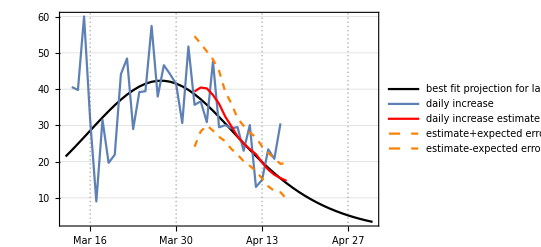
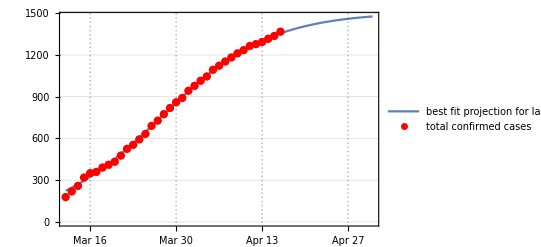
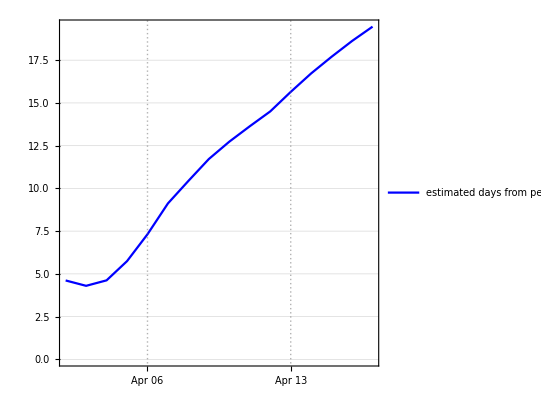
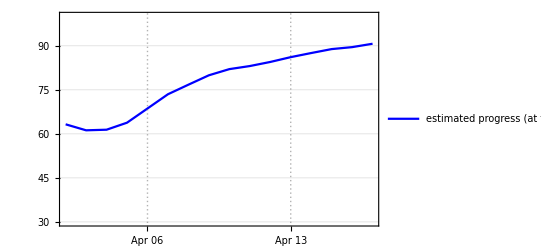

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[cp0,cp20,timecpert,cpert,cpstartdate,21,14,0]
```

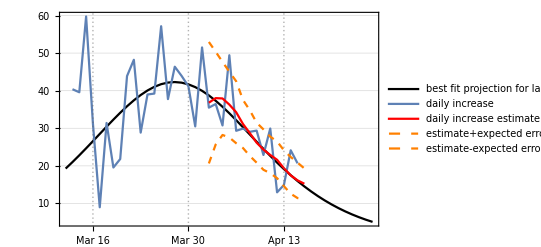

```mathematica
graf
```

```mathematica
Export["slograf.png",graf]
Export["slologgraf.png",loggraf]
Export["slodfgraf.png",dfpplot]
Export["sloprogplot.png",progplot]
```

slograf.png

slologgraf.png

slodfgraf.png

sloprogplot.png

{23056.4,55.8783,0.276821}

{217340.,6718.05,0.0809455}

{217340.,6718.05,0.0809455}

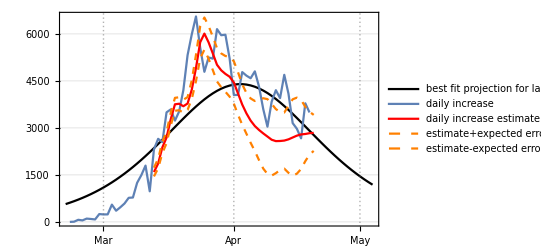
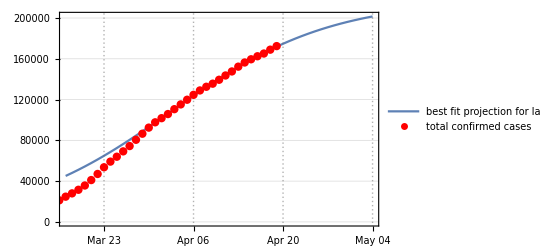
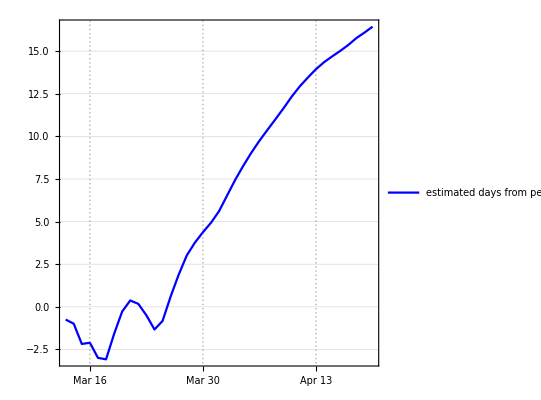
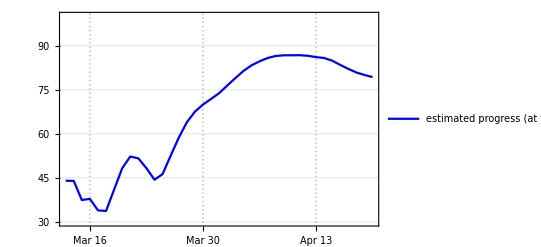

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[ip0,itp20,timeitco,itco,itstartdate,21,14,25]
```

```mathematica
Export["italygraf.png",graf]
Export["italyloggraf.png",loggraf]
Export["italydfgraf.png",dfpplot]
Export["italyprogplot.png",progplot]
```

italygraf.png

italyloggraf.png

italydfgraf.png

italyprogplot.png

{9943.54,14.6999,0.258747}

{15143.2,276.715,0.1455}

{15143.2,276.715,0.1455}

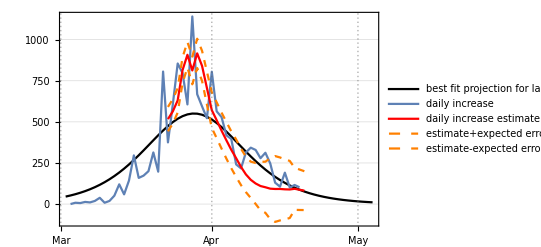
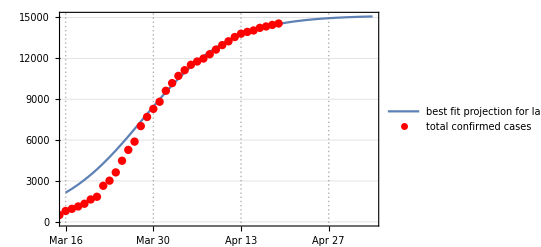
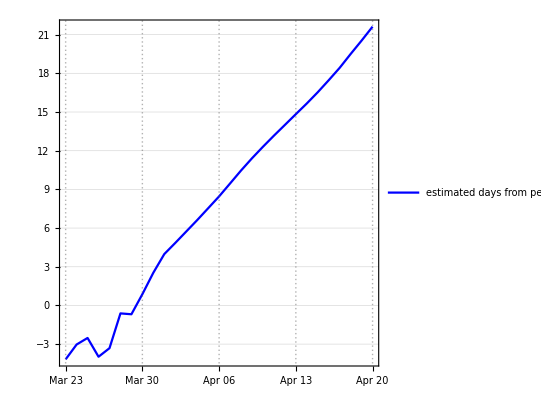
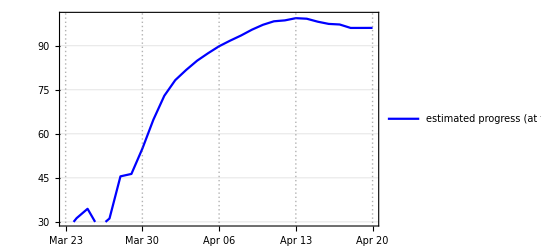

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[avp0,avp20,timeavco,avco,avstartdate,21,14,14]
```

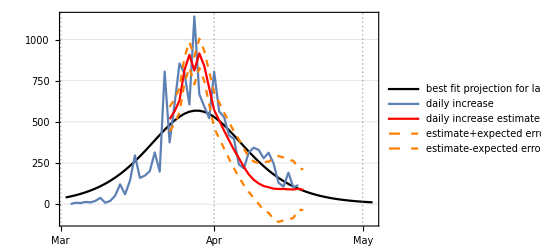

```mathematica
graf
```

```mathematica
Export["austriagraf.png",graf]
Export["austrialoggraf.png",loggraf]
Export["austriadfgraf.png",dfpplot]
Export["austriaprogplot.png",progplot]
```

austriagraf.png

austrialoggraf.png

austriadfgraf.png

austriaprogplot.png

{51026.4,128.882,0.327775}

{148267.,2309.27,0.147627}

{148267.,2309.27,0.147627}

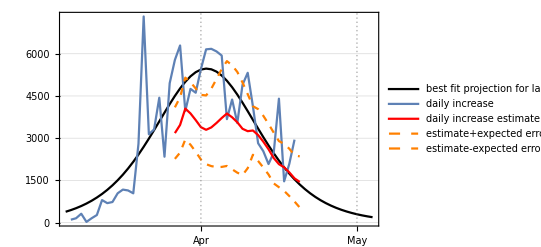
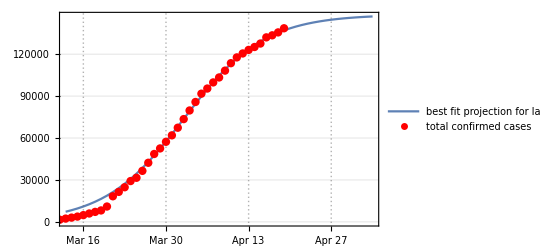
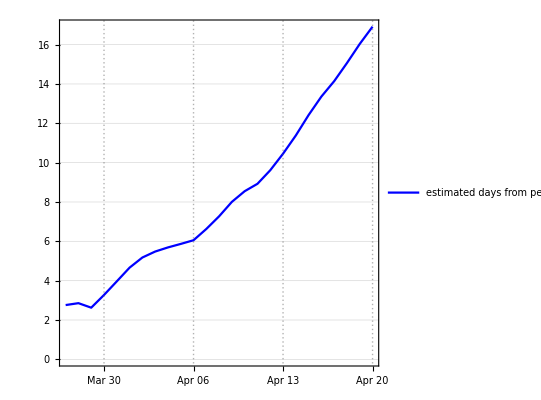
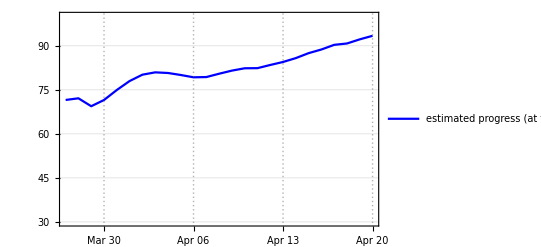

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[gp0,gp20,timelgerco,lgerco,gerstartdate,21,14,7]
```

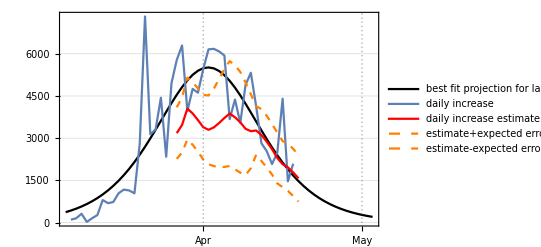

```mathematica
graf
```

```mathematica
Export["germangraf.png",graf]
Export["germanloggraf.png",loggraf]
Export["germandfgraf.png",dfpplot]
Export["germanprogplot.png",progplot]
```

germangraf.png

germanloggraf.png

germandfgraf.png

germanprogplot.png

```mathematica
gerstartdate
```

{2020,3,6}

```mathematica
ameristartdate={2020,3,20}
```

{2020,3,20}

{609519.,18667.,0.203405}

{830958.,29295.7,0.160558}

{830958.,29295.7,0.160558}

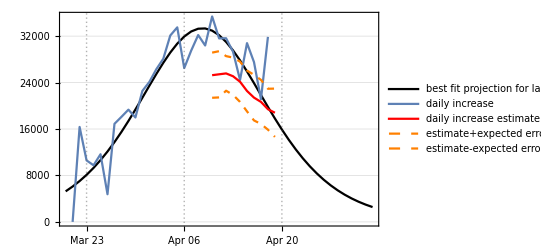
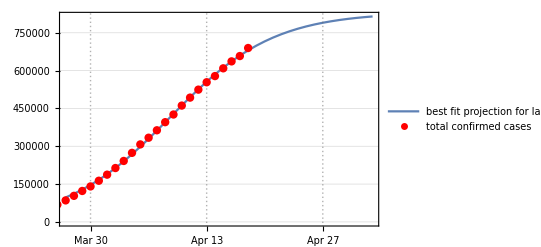
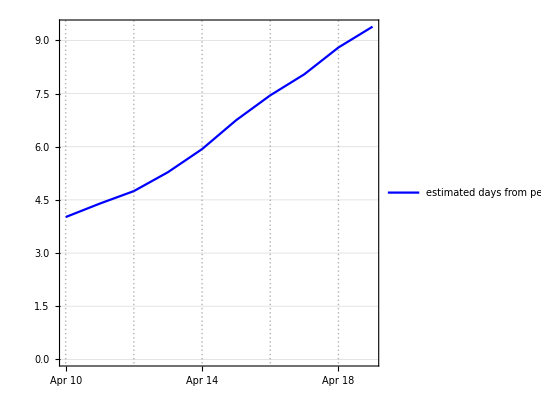
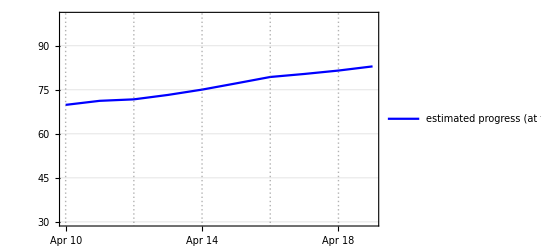

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[ap0,ap20,timemeri,ameri,ameristartdate,21,14,7]
```

```mathematica
oneplot=DateListPlot[dailyincrease,DatePlus[startdate,1],Joined->True,PlotLegends->{"daily increase"}];
erplot=DateListPlot[{stats[[1]],stats[[1]]+stats[[2]],stats[[1]]-stats[[2]]},DatePlus[startdate,lag],Joined->True,PlotStyle->{{Red},{Orange,Dashed},{Orange,Dashed}},PlotLegends->{"daily increase estimate (at the time)","estimate+expected error","estimate-expected error"}];

projtimeinterval=Flatten[Append[ttime,Table[t,{t,ttime[[-1]]+1,ttime[[-1]]+projtime+1}]]];
dlplot=DateListPlot[Map[dlfun[#,fip0]&,projtimeinterval],startdate,PlotLegends->{"best fit projection for last 3 weeks of data"},PlotStyle->{Black},PlotTheme->"Detailed"];
```

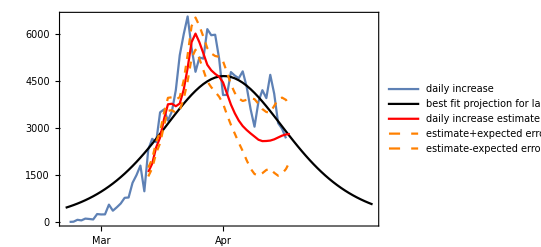

```mathematica
graf=Show[oneplot,dlplot,erplot,PlotRange->All]
```

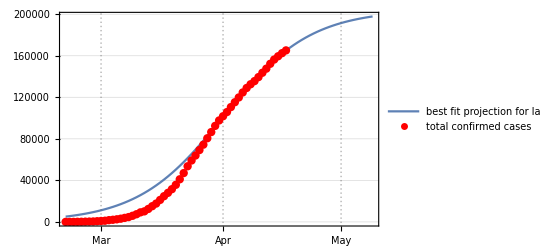

```mathematica
logfunplot=DateListPlot[Map[lfun[#,fip0]&,projtimeinterval],startdate,PlotLegends->{"best fit projection for last 3 weeks of data"},PlotTheme->"Detailed"];
cumdinplot=DateListPlot[tdata,startdate,Joined->False,PlotLegends->{"total confirmed cases"},PlotStyle->{Red,PointSize[0.015]}];
loggraf=Show[logfunplot,cumdinplot]
```

```mathematica
Export["slologgraf.png",loggraf]
```

slologgraf.png

```mathematica
Export["italyloggraf.png",loggraf]
```

italyloggraf.png

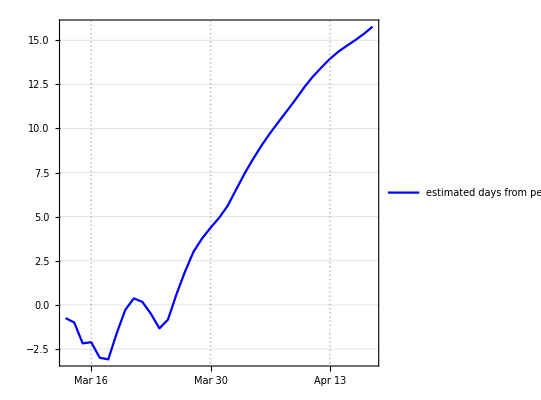

```mathematica
dfpplot=DateListPlot[{-stats[[4]]},DatePlus[startdate,lag],PlotLegends->{"estimated days from peak (at the time)"},PlotStyle->{Blue,PointSize[0.010]},PlotTheme->"Detailed",AspectRatio->1]
```

```mathematica
Export["slodfgraf.png",dfpplot]
```

slodfgraf.png

```mathematica
Export["italydfgraf.png",dfpplot]
```

italydfgraf.png

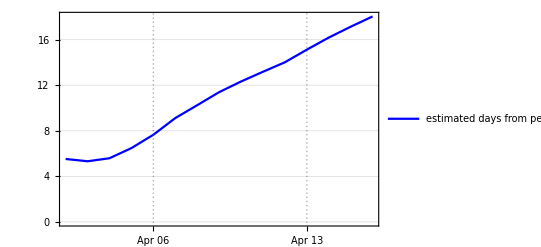

```mathematica
dfpplot
```

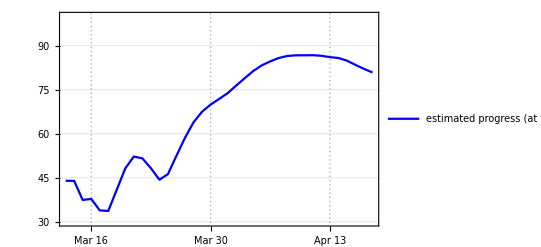

```mathematica
progress=stats[[5]];
progplot=dfpplot=DateListPlot[{progress},DatePlus[startdate,lag],PlotLegends->{"estimated progress (at the time)"},PlotStyle->{Blue,PointSize[0.010]},PlotTheme->"Detailed",PlotRange->{30,100}]
```

```mathematica
Export["sloprogplot.png",progplot]
```

sloprogplot.png

```mathematica
Export["italyprogplot.png",progplot]
```

italyprogplot.png

```mathematica
Directory[]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

```mathematica
SetDirectory
```

SetDirectory

```mathematica
Export["italygraf.png",graf]
```

italygraf.png

```mathematica
Export["slograf.png",graf]
```

slograf.png

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
stats
```

{{36.786,38.0026,37.9179,36.2851,34.2561,31.1302,28.7099,26.1587,24.3181,22.8905,21.6064,19.3701,17.464,16.1366},{16.1505,12.328,9.71237,8.74194,8.24369,6.39022,6.06869,5.31397,5.36807,4.85114,4.89034,4.76975,4.88,4.70799},{51.483,35.4734,36.4369,30.7382,49.4074,29.3125,29.9013,29.0387,29.3682,22.879,29.9187,12.9536,14.8862,24.1327},{-5.52448,-5.32335,-5.58894,-6.47877,-7.65064,-9.11509,-10.2458,-11.3908,-12.3279,-13.1816,-14.0154,-15.1214,-16.1837,-17.1357},{67.9569,65.7681,65.6157,67.4022,71.424,75.3786,78.0833,80.8631,82.694,83.559,84.8393,86.34,87.6591,88.9882}}

```mathematica
stp0=ip0;
ttime=timeitco;
tdata=itco;

stp0=avp0;
ttime=timeavco;
tdata=avco;

stp0=cp0;
ttime=timecpert;
tdata=cpert;

stp0=gp0;
ttime=timelgerco;
tdata=lgerco;

stp0=ap0;
ttime=timemeri;
tdata=ameri;

lag=21
projtime=21;

dailyincrease=tdata[[2;;-1]]-tdata[[;;-2]];
{tabs,twindows}=estimates[tdata,stp0,21,ttime];
stats=generatestats[tdata,stp0,21,ttime];

allstats=Transpose[stats];
allstats=PrependTo[allstats,{"oneday","error","actual","dtop","perc","final","time"}];
TableForm[allstats];
```

21

{609519.,18667.,0.203405}

{830958.,29295.7,0.160558}

{609519.,18667.,0.203405}

{830958.,29295.7,0.160558}

{830958.,29295.7,0.160558}

```mathematica
limits=stats[[6]];
limitdifs=Differences[limits];
%//Length
peaks=Map[expeak[#]&,tabs];
peakdifs=Differences[peaks];
%//Length
errors=stats[[2]][[2;;-1]];
%//Length
actual=stats[[3]];
onedayest=stats[[1]];
actualerrors=actual[[2;;]]-onedayest[[;;-2]]
```

9

9

9

{10116.8,6183.45,6058.36,4220.67,305.291,8242.03,6122.14,460.329,12457.3}

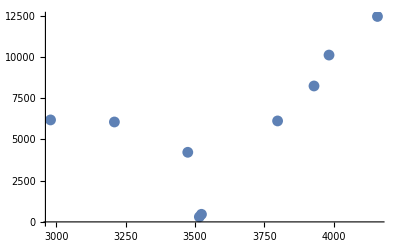

6018.48

```mathematica
ListPlot[Transpose[{errors,actualerrors}]]
Mean[actualerrors]
```

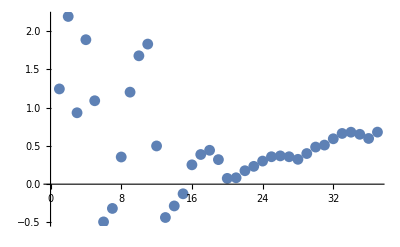

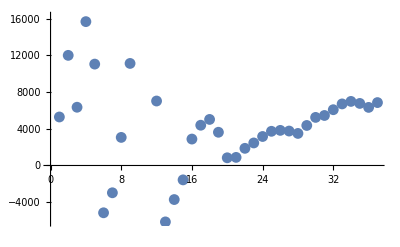

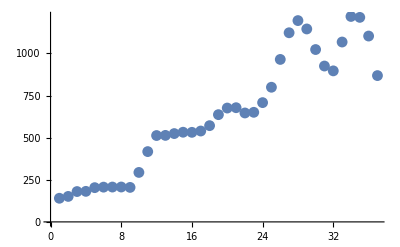

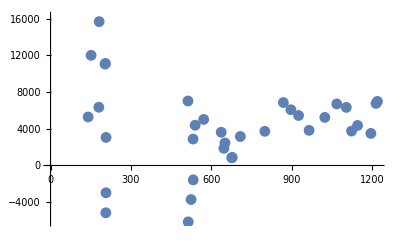

```mathematica
ListPlot[peakdifs]
ListPlot[limitdifs]
ListPlot[errors]
ListPlot[Transpose[{errors,limitdifs}]]
```

```mathematica
Length[errors]
Length[limitdifs]
```

37

37

```mathematica
LinearModelFit[Transpose[{errors,limitdifs}],x,x]
```

FittedModel[6083.86-1.53564 x]

```mathematica
Correlation
```

```mathematica
?wmf
```

Global`wmf

wmf[x_,{a_,b_,c_}]:=(a b)/(b+(a-b) Exp[-c x])

```mathematica
nlm=NonlinearModelFit[avco,(a b)/(b+(a-b) Exp[-c x]),{a,b,c},x]
```

FittedModel[495793./(34.9928+14133.4 ⅇ^(«1»))]

```mathematica
FindFit[avco,(a b)/(b+(a-b) Exp[-c x]),{a,b,c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→12505.7,b→0.0000557758,c→0.720537}

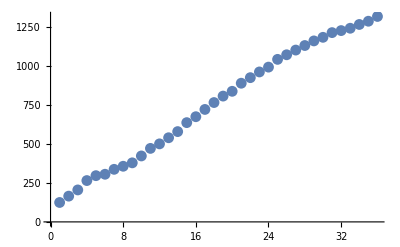

```mathematica
ListPlot[cpert]
```

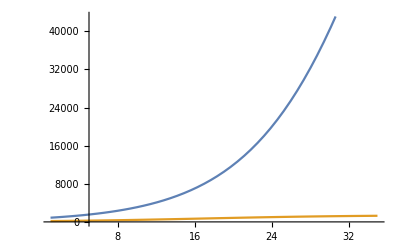

```mathematica
Plot[{Normal[nlm],wmf[x,mafit]},{x,1,35}]
```

```mathematica
sip20
```

{1396.14,62.9284,0.125822}

```mathematica
?wmf
```

Global`wmf

wmf[x_,{a_,b_,c_}]:=(a b)/(b+(a-b) Exp[-c x])

```mathematica
222726.66744459837/156.7978330588267
```

1420.47

```mathematica
mafit={1420.470315817673,156.7978330588267,0.12351884315316117}
```

{1420.47,156.798,0.123519}

```mathematica
RMSQ[cpert,mafit]
```

13.5142

```mathematica
RMSQ[cpert,cp0]
```

13.5151

```mathematica
?RMSQ
```

Global`RMSQ

RMSQ[data_,ip0_,time_]:=√Mean[(wmf[time,ip0]-data)^2]
 
RMSQ[data_,ip0_]:=RMSQ[data,ip0,Table[i,{i,1,Length[data]}]]

```mathematica
?showplots
```

Global`showplots

showplots[data_,p0_]:=Module[{time,dplot,wmfplot},time=Table[i,{i,1,Length[data]}];dplot=ListPlot[data];wmfplot=Plot[wmf[x,p0],{x,0,2 Length[data]}];Show[wmfplot,dplot]]

```mathematica
?RMSQ
```

Global`RMSQ

RMSQ[data_,ip0_,time_]:=√Mean[(wmf[time,ip0]-data)^2]
 
RMSQ[data_,ip0_]:=RMSQ[data,ip0,Table[i,{i,1,Length[data]}]]

```mathematica
NonlinearModelFit[itco,a +b x^2,{a,b},x,Method->"Gradient"]
```

NonlinearModelFit::lmnl: The model a + b\ x^2 is linear in the parameters {a, b}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

FittedModel[-5873.12+57.2 x^2]

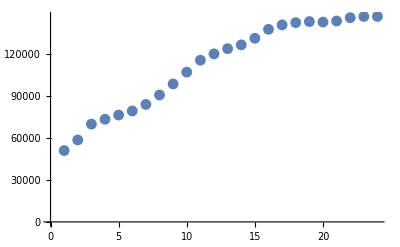

```mathematica
ListPlot[stats[[6]]]
```

```mathematica
{tabs,twindows}=estimates[itco,ip0,21,timeitco];
```

{23056.4,55.8783,0.276821}

{211006.,5691.2,0.0855537}

```mathematica
{tabs,twindows}=estimates[lgerco,gp0,21,timelgerco];
```

{51026.4,128.882,0.327775}

{147016.,2183.04,0.150013}

```mathematica
{tabs,twindows}=estimates[cpert,cp0,21,timecpert];
```

{1306.91,149.908,0.132107}

{1450.53,175.061,0.115875}

```mathematica
{tabs,twindows}=estimates[avco,avp0,21,timeavco];
```

{9943.54,14.6999,0.258747}

{15038.6,232.561,0.151255}

```mathematica
limits=
Transpose[tabs][[1]];
peaks=Map[expeak[#]&,tabs];
```

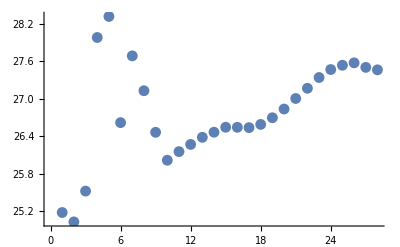

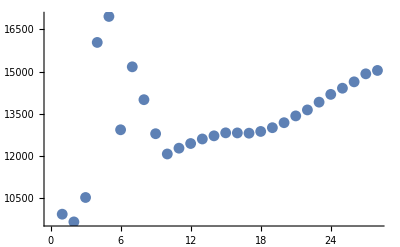

```mathematica
ListPlot[peaks]
ListPlot[limits]
```

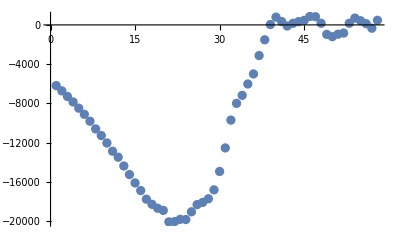

```mathematica
ListPlot[itco-Map[lfun[#,itp20]&,timeitco]]
```

```mathematica
?RMSQ
```

Global`RMSQ

RMSQ[data_,ip0_,time_]:=√Mean[(wmf[time,ip0]-data)^2]
 
RMSQ[data_,ip0_]:=RMSQ[data,ip0,Table[i,{i,1,Length[data]}]]

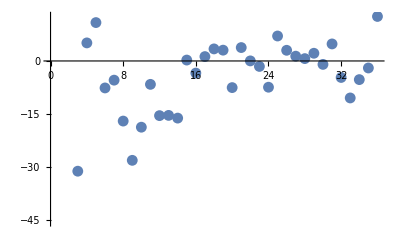

```mathematica
ListPlot[cpert-Map[lfun[#,cp20]&,timecpert]]
```

```mathematica
?lfun
```

Global`lfun

lfun[x_,p0_]:=wmf[x,p0]

```mathematica
tablestring=TableForm[{{0.2,0.333,Pi},{x^2,2,3}},TableAlignments->Center,,TableHeadings->{None,{"prva",Sqrt[x],1/x}}]
```

prva | √x | 1/x
0.2 | 0.333 | π
x^2 | 2 | 3

```mathematica
tablestring=MathMLForm[TableForm[{{0.2,0.333,Pi},{x^2,2,3}},TableAlignments->Center,TableHeadings->{None,{prva stvar,Sqrt[x],1/x}}]]
```

XMLElement::unqatt: The attribute name ("columnalign") in "columnalign" → "left" is not unique; there is already an attribute with this name in the same XMLElement. Two attributes with the same name cannot exist inside the same element.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

<math>
 <semantics>
  <mtable rowspacing='1ex'
      columnspacing='3em'
      rowalign='center'
      columnalign='center'
      columnlines='none'
      rowlines='solid none'>
   <mtr>
    <mtd>
     <mrow>
      <mi>prva</mi>
      <mo>&#8290;</mo>
      <mi>stvar</mi>
     </mrow>
    </mtd>
    <mtd>
     <msqrt>
      <mi>x</mi>
     </msqrt>
    </mtd>
    <mtd>
     <mfrac>
      <mn>1</mn>
      <mi>x</mi>
     </mfrac>
    </mtd>
   </mtr>
   <mtr>
    <mtd>
     <mn>0.2</mn>
    </mtd>
    <mtd>
     <mn>0.333</mn>
    </mtd>
    <mtd>
     <mi>&#960;</mi>
    </mtd>
   </mtr>
   <mtr>
    <mtd>
     <msup>
      <mi>x</mi>
      <mn>2</mn>
     </msup>
    </mtd>
    <mtd>
     <mn>2</mn>
    </mtd>
    <mtd>
     <mn>3</mn>
    </mtd>
   </mtr>
  </mtable>
  <annotation
   encoding='Mathematica'>TagBox[TagBox[GridBox[List[List[TagBox[RowBox[List[&quot;prva&q
   uot;, &quot; &quot;, &quot;stvar&quot;]], HoldForm], TagBox[SqrtBox[&quot;x&quot;],
   HoldForm], TagBox[FractionBox[&quot;1&quot;, &quot;x&quot;], HoldForm]],
   List[&quot;0.2`&quot;, &quot;0.333`&quot;, &quot;π&quot;],
   List[SuperscriptBox[&quot;x&quot;, &quot;2&quot;], &quot;2&quot;, &quot;3&quot;]],
   Rule[RowSpacings, 1], Rule[ColumnSpacings, 3], Rule[RowAlignments, Center],
   Rule[ColumnAlignments, Center], Rule[ColumnLines, False], Rule[RowLines, List[1,
   False]], Rule[ColumnAlignments, Left]], List[None, OutputFormsDump`HeadedColumns]],
   Function[BoxForm`e$, TableForm[BoxForm`e$, Rule[TableAlignments, Center],
   Rule[TableHeadings, List[None, List[Times[prva, stvar], Power[x, Rational[1, 2]],
   Power[x, -1]]]]]]]</annotation>
 </semantics>
</math>

```mathematica
texstring=TeXForm[tablestring]
```

\begin{array}{ccc}
 \text{prva} & \sqrt{x} & \frac{1}{x} \\
 0.2 & 0.333 & \pi  \\
 x^2 & 2 & 3 \\
\end{array}

```mathematica
texstring=StringReplace[texstring," \ "->"*"]
```

StringReplace::strse: String or list of strings expected at position 1 in FrameBox[.

StringReplace[\begin{array}{ccc}
 \text{prva} & \sqrt{x} & \frac{1}{x} \\
 0.2 & 0.333 & \pi  \\
 x^2 & 2 & 3 \\
\end{array},  →*]

```mathematica
tablestring=StringReplace[tablestring,"\*\ "->"\\  "]
```

\begin{array}{ccc}
\*  text{prva} &\*  sqrt{x} &\*  frac{1}{x}\*  \
 0.2 & 0.333 &\*  pi \*  \
 x^2 & 2 & 3\*  \
\end{array}

```mathematica
\\\
```

```mathematica
NotebookDirectory[]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/data"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/data

```mathematica
FilePtr=OpenWrite["testoutput.tex",CharacterEncoding->"UTF8"];
```

```mathematica
WriteString[FilePtr,tablestring];
```

XMLElement::unqatt: The attribute name ("columnalign") in "columnalign" → "left" is not unique; there is already an attribute with this name in the same XMLElement. Two attributes with the same name cannot exist inside the same element.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

```mathematica
Close[FilePtr]
```

testoutput.tex

```mathematica
exportstring=ExportString[tablestring,"XHTMLMathML"]
```

<?xml version="1.0" encoding="UTF-8"?>
<?xml-stylesheet type="text/xsl" href="HTMLFiles/pmathml.xsl"?>
<!DOCTYPE html PUBLIC "-//W3C//DTD XHTML 1.1 plus MathML 2.0//EN"
        "HTMLFiles/xhtml-math11-f.dtd">

<!-- Created with the Wolfram Language : www.wolfram.com -->

<html xmlns="http://www.w3.org/1999/xhtml">
<head>
 <title>
  Untitled
 </title>
 <link href="HTMLFiles/m00001781341.css" rel="stylesheet" type="text/css" />
</head>

<body>

<table class='Output'>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span>prva</span></td>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <msqrt>
  <mi>x</mi>
 </msqrt>
</math></span></td>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <mfrac>
  <mn>1</mn>
  <mi>x</mi>
 </mfrac>
</math></span></td>
 </tr>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span>0.2</span></td>
  <td style='text-align: center;'><span>0.333</span></td>
  <td style='text-align: center;'><span>&pi;</span></td>
 </tr>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <msup>
  <mi>x</mi>
  <mn>2</mn>
 </msup>
</math></span></td>
  <td style='text-align: center;'><span>2</span></td>
  <td style='text-align: center;'><span>3</span></td>
 </tr>
</table>




<div style="font-family:Helvetica; font-size:11px; width:100%; border:1px none #999999; border-top-style:solid; padding-top:2px; margin-top:20px;">
 <a href="http://www.wolfram.com/language/" style="color:#000; text-decoration:none;">
  <span style="color:#555555">Created with the Wolfram Language</span> 
 </a>
</div>
</body>

</html>

```mathematica
dstringstart=StringPosition[exportstring,"DOCTYPE"][[1,1]]
dstringfinish=StringPosition[exportstring,"-->"][[1,2]]
exportstring=StringDrop[exportstring,{dstringstart,dstringfinish}]
```

106

270

<?xml version="1.0" encoding="UTF-8"?>
<?xml-stylesheet type="text/xsl" href="HTMLFiles/pmathml.xsl"?>
<!

<html xmlns="http://www.w3.org/1999/xhtml">
<head>
 <title>
  Untitled
 </title>
 <link href="HTMLFiles/m00001781341.css" rel="stylesheet" type="text/css" />
</head>

<body>

<table class='Output'>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span>prva</span></td>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <msqrt>
  <mi>x</mi>
 </msqrt>
</math></span></td>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <mfrac>
  <mn>1</mn>
  <mi>x</mi>
 </mfrac>
</math></span></td>
 </tr>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span>0.2</span></td>
  <td style='text-align: center;'><span>0.333</span></td>
  <td style='text-align: center;'><span>&pi;</span></td>
 </tr>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <msup>
  <mi>x</mi>
  <mn>2</mn>
 </msup>
</math></span></td>
  <td style='text-align: center;'><span>2</span></td>
  <td style='text-align: center;'><span>3</span></td>
 </tr>
</table>




<div style="font-family:Helvetica; font-size:11px; width:100%; border:1px none #999999; border-top-style:solid; padding-top:2px; margin-top:20px;">
 <a href="http://www.wolfram.com/language/" style="color:#000; text-decoration:none;">
  <span style="color:#555555">Created with the Wolfram Language</span> 
 </a>
</div>
</body>

</html>

```mathematica
exportstring=ExportString[tablestring,"XHTMLMathML"]
```

<?xml version="1.0" encoding="UTF-8"?>
<?xml-stylesheet type="text/xsl" href="HTMLFiles/pmathml.xsl"?>
<!DOCTYPE html PUBLIC "-//W3C//DTD XHTML 1.1 plus MathML 2.0//EN"
        "HTMLFiles/xhtml-math11-f.dtd">

<!-- Created with the Wolfram Language : www.wolfram.com -->

<html xmlns="http://www.w3.org/1999/xhtml">
<head>
 <title>
  Untitled
 </title>
 <link href="HTMLFiles/m00001281341.css" rel="stylesheet" type="text/css" />
</head>

<body>

<table class='Output'>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span>prva</span></td>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <msqrt>
  <mi>x</mi>
 </msqrt>
</math></span></td>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <mfrac>
  <mn>1</mn>
  <mi>x</mi>
 </mfrac>
</math></span></td>
 </tr>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span>0.2</span></td>
  <td style='text-align: center;'><span>0.333</span></td>
  <td style='text-align: center;'><span>&pi;</span></td>
 </tr>
 <tr style='vertical-align: middle;'>
  <td style='text-align: center;'><span><math xmlns='http://www.w3.org/1998/Math/MathML'>
 <msup>
  <mi>x</mi>
  <mn>2</mn>
 </msup>
</math></span></td>
  <td style='text-align: center;'><span>2</span></td>
  <td style='text-align: center;'><span>3</span></td>
 </tr>
</table>




<div style="font-family:Helvetica; font-size:11px; width:100%; border:1px none #999999; border-top-style:solid; padding-top:2px; margin-top:20px;">
 <a href="http://www.wolfram.com/language/" style="color:#000; text-decoration:none;">
  <span style="color:#555555">Created with the Wolfram Language</span> 
 </a>
</div>
</body>

</html>

```mathematica
SetDirectory["/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports"]
```

/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports

```mathematica
FileNames["*","/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports"]
```

{/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports/.DS_Store,/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports/README.md,/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports/who_covid_19_sit_rep_pdfs,/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports/who_covid_19_sit_rep_time_series}

```mathematica
"/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports/who_covid_19_sit_rep_time_series"
```

/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports/who_covid_19_sit_rep_time_series

```mathematica
SystemOpen["/Users/peterkink/hopkins/COVID-19/who_covid_19_situation_reports/who_covid_19_sit_rep_time_series"]
```

```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
```

```mathematica
transeries=Transpose[series];
transeries=Drop[transeries,1];
```

```mathematica
Dimensions[series]
```

{265,92}

```mathematica
TableForm[transeries]
```

Country/Region | Afghanistan | Albania | Algeria | Andorra | Angola | Antigua and Barbuda | Argentina | Armenia | Australia | Australia | Australia | Australia | Australia | Australia | Australia | Australia | Austria | Azerbaijan | Bahamas | Bahrain | Bangladesh | Barbados | Belarus | Belgium | Benin | Bhutan | Bolivia | Bosnia and Herzegovina | Brazil | Brunei | Bulgaria | Burkina Faso | Cabo Verde | Cambodia | Cameroon | Canada | Canada | Canada | Canada | Canada | Canada | Canada | Canada | Canada | Canada | Canada | Central African Republic | Chad | Chile | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | China | Colombia | Congo (Brazzaville) | Congo (Kinshasa) | Costa Rica | Cote d'Ivoire | Croatia | Diamond Princess | Cuba | Cyprus | Czechia | Denmark | Denmark | Denmark | Djibouti | Dominican Republic | Ecuador | Egypt | El Salvador | Equatorial Guinea | Eritrea | Estonia | Eswatini | Ethiopia | Fiji | Finland | France | France | France | France | France | France | France | France | France | France | Gabon | Gambia | Georgia | Germany | Ghana | Greece | Guatemala | Guinea | Guyana | Haiti | Holy See | Honduras | Hungary | Iceland | India | Indonesia | Iran | Iraq | Ireland | Israel | Italy | Jamaica | Japan | Jordan | Kazakhstan | Kenya | Korea, South | Kuwait | Kyrgyzstan | Latvia | Lebanon | Liberia | Liechtenstein | Lithuania | Luxembourg | Madagascar | Malaysia | Maldives | Malta | Mauritania | Mauritius | Mexico | Moldova | Monaco | Mongolia | Montenegro | Morocco | Namibia | Nepal | Netherlands | Netherlands | Netherlands | Netherlands | New Zealand | Nicaragua | Niger | Nigeria | North Macedonia | Norway | Oman | Pakistan | Panama | Papua New Guinea | Paraguay | Peru | Philippines | Poland | Portugal | Qatar | Romania | Russia | Rwanda | Saint Lucia | Saint Vincent and the Grenadines | San Marino | Saudi Arabia | Senegal | Serbia | Seychelles | Singapore | Slovakia | Slovenia | Somalia | South Africa | Spain | Sri Lanka | Sudan | Suriname | Sweden | Switzerland | Taiwan* | Tanzania | Thailand | Togo | Trinidad and Tobago | Tunisia | Turkey | Uganda | Ukraine | United Arab Emirates | United Kingdom | United Kingdom | United Kingdom | United Kingdom | United Kingdom | United Kingdom | United Kingdom | Uruguay | US | Uzbekistan | Venezuela | Vietnam | Zambia | Zimbabwe | Canada | Dominica | Grenada | Mozambique | Syria | Timor-Leste | Belize | Canada | Laos | Libya | West Bank and Gaza | Guinea-Bissau | Mali | Saint Kitts and Nevis | Canada | Canada | Kosovo | Burma | United Kingdom | United Kingdom | United Kingdom | MS Zaandam | Botswana | Burundi | Sierra Leone | Netherlands | Malawi | United Kingdom | France | South Sudan | Western Sahara | Sao Tome and Principe | Yemen
Lat | 33. | 41.1533 | 28.0339 | 42.5063 | -11.2027 | 17.0608 | -38.4161 | 40.0691 | -35.4735 | -33.8688 | -12.4634 | -28.0167 | -34.9285 | -41.4545 | -37.8136 | -31.9505 | 47.5162 | 40.1431 | 25.0343 | 26.0275 | 23.685 | 13.1939 | 53.7098 | 50.8333 | 9.3077 | 27.5142 | -16.2902 | 43.9159 | -14.235 | 4.5353 | 42.7339 | 12.2383 | 16.5388 | 11.55 | 3.848 | 53.9333 | 49.2827 | 37.6489 | 53.7609 | 46.5653 | 53.1355 | 44.682 | 51.2538 | 46.5107 | 52.9399 | 52.9399 | 6.6111 | 15.4542 | -35.6751 | 31.8257 | 40.1824 | 30.0572 | 26.0789 | 37.8099 | 23.3417 | 23.8298 | 26.8154 | 19.1959 | 39.549 | 47.862 | 33.882 | 22.3 | 30.9756 | 27.6104 | 44.0935 | 32.9711 | 27.614 | 43.6661 | 41.2956 | 22.1667 | 37.2692 | 35.7452 | 35.1917 | 36.3427 | 31.202 | 37.5777 | 30.6171 | 39.3054 | 31.6927 | 41.1129 | 24.974 | 29.1832 | 4.5709 | -4.0383 | -4.0383 | 9.7489 | 7.54 | 45.1 | 0. | 22. | 35.1264 | 49.8175 | 61.8926 | 71.7069 | 56.2639 | 11.8251 | 18.7357 | -1.8312 | 26. | 13.7942 | 1.5 | 15.1794 | 58.5953 | -26.5225 | 9.145 | -17.7134 | 64. | 3.9339 | -17.6797 | 16.25 | -12.8275 | -20.9043 | -21.1351 | 17.9 | 18.0708 | 14.6415 | 46.2276 | -0.8037 | 13.4432 | 42.3154 | 51. | 7.9465 | 39.0742 | 15.7835 | 9.9456 | 5. | 18.9712 | 41.9029 | 15.2 | 47.1625 | 64.9631 | 21. | -0.7893 | 32. | 33. | 53.1424 | 31. | 43. | 18.1096 | 36. | 31.24 | 48.0196 | -0.0236 | 36. | 29.5 | 41.2044 | 56.8796 | 33.8547 | 6.4281 | 47.14 | 55.1694 | 49.8153 | -18.7669 | 2.5 | 3.2028 | 35.9375 | 21.0079 | -20.2 | 23.6345 | 47.4116 | 43.7333 | 46.8625 | 42.5 | 31.7917 | -22.9576 | 28.1667 | 12.5186 | 12.1696 | 18.0425 | 52.1326 | -40.9006 | 12.8654 | 17.6078 | 9.082 | 41.6086 | 60.472 | 21. | 30.3753 | 8.538 | -6.315 | -23.4425 | -9.19 | 13. | 51.9194 | 39.3999 | 25.3548 | 45.9432 | 60. | -1.9403 | 13.9094 | 12.9843 | 43.9424 | 24. | 14.4974 | 44.0165 | -4.6796 | 1.2833 | 48.669 | 46.1512 | 5.1521 | -30.5595 | 40. | 7. | 12.8628 | 3.9193 | 63. | 46.8182 | 23.7 | -6.369 | 15. | 8.6195 | 10.6918 | 34. | 38.9637 | 1. | 48.3794 | 24. | 32.3078 | 19.3133 | 49.3723 | 36.1408 | 54.2361 | 16.7425 | 55.3781 | -32.5228 | 37.0902 | 41.3775 | 6.4238 | 16. | -15.4167 | -20. | 0. | 15.415 | 12.1165 | -18.6657 | 34.8021 | -8.87422 | 13.1939 | 0. | 19.8563 | 26.3351 | 31.9522 | 11.8037 | 17.5707 | 17.3578 | 64.8255 | 64.2823 | 42.6026 | 21.9162 | 18.2206 | 18.4207 | 21.694 | 0. | -22.3285 | -3.3731 | 8.46056 | 12.1784 | -13.2543 | -51.7963 | 46.8852 | 6.877 | 24.2155 | 0.18636 | 15.5527
Long | 65. | 20.1683 | 1.6596 | 1.5218 | 17.8739 | -61.7964 | -63.6167 | 45.0382 | 149.012 | 151.209 | 130.846 | 153.4 | 138.601 | 145.971 | 144.963 | 115.861 | 14.5501 | 47.5769 | -77.3963 | 50.55 | 90.3563 | -59.5432 | 27.9534 | 4. | 2.3158 | 90.4336 | -63.5887 | 17.6791 | -51.9253 | 114.728 | 25.4858 | -1.5616 | -23.0418 | 104.917 | 11.5021 | -116.577 | -123.121 | -122.666 | -98.8139 | -66.4619 | -57.6604 | -63.7443 | -85.3232 | -63.4168 | -73.5491 | -106.451 | 20.9394 | 18.7322 | -71.543 | 117.226 | 116.414 | 107.874 | 117.987 | 101.058 | 113.424 | 108.788 | 106.875 | 109.745 | 116.131 | 127.762 | 113.614 | 114.2 | 112.271 | 111.709 | 113.945 | 119.455 | 115.722 | 126.192 | 122.609 | 113.55 | 106.166 | 95.9956 | 108.87 | 118.15 | 121.449 | 112.292 | 102.71 | 117.323 | 88.0924 | 85.2401 | 101.487 | 120.093 | -74.2973 | 21.7587 | 21.7587 | -83.7534 | -5.5471 | 15.2 | 0. | -80. | 33.4299 | 15.473 | -6.9118 | -42.6043 | 9.5018 | 42.5903 | -70.1627 | -78.1834 | 30. | -88.8965 | 10. | 39.7823 | 25.0136 | 31.4659 | 40.4897 | 178.065 | 26. | -53.1258 | 149.407 | -61.5833 | 45.1662 | 165.618 | 55.2471 | -62.8333 | -63.0501 | -61.0242 | 2.2137 | 11.6094 | -15.3101 | 43.3569 | 9. | -1.0232 | 21.8243 | -90.2308 | -9.6966 | -58.75 | -72.2852 | 12.4534 | -86.2419 | 19.5033 | -19.0208 | 78. | 113.921 | 53. | 44. | -7.6921 | 35. | 12. | -77.2975 | 138. | 36.51 | 66.9237 | 37.9062 | 128. | 47.75 | 74.7661 | 24.6032 | 35.8623 | -9.4295 | 9.55 | 23.8813 | 6.1296 | 46.8691 | 112.5 | 73.2207 | 14.3754 | 10.9408 | 57.5 | -102.553 | 28.3699 | 7.4167 | 103.847 | 19.3 | -7.0926 | 18.4904 | 84.25 | -70.0358 | -68.99 | -63.0548 | 5.2913 | 174.886 | -85.2072 | 8.0817 | 8.6753 | 21.7453 | 8.4689 | 57. | 69.3451 | -80.7821 | 143.956 | -58.4438 | -75.0152 | 122. | 19.1451 | -8.2245 | 51.1839 | 24.9668 | 90. | 29.8739 | -60.9789 | -61.2872 | 12.4578 | 45. | -14.4524 | 21.0059 | 55.492 | 103.833 | 19.699 | 14.9955 | 46.1996 | 22.9375 | -4. | 81. | 30.2176 | -56.0278 | 16. | 8.2275 | 121. | 34.8888 | 101. | 0.8248 | -61.2225 | 9. | 35.2433 | 32. | 31.1656 | 54. | -64.7505 | -81.2546 | -2.3644 | -5.3536 | -4.5481 | -62.1874 | -3.436 | -55.7658 | -95.7129 | 64.5853 | -66.5897 | 108. | 28.2833 | 30. | 0. | -61.371 | -61.679 | 35.5296 | 38.9968 | 125.728 | -59.5432 | 0. | 102.495 | 17.2283 | 35.2332 | -15.1804 | -3.99617 | -62.783 | -124.846 | -135. | 20.903 | 95.956 | -63.0686 | -64.64 | -71.7979 | 0. | 24.6849 | 29.9189 | -11.7799 | -68.2385 | 34.3015 | -59.5236 | -56.3159 | 31.307 | -12.8858 | 6.61308 | 48.5164
1/22/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 14 | 6 | 1 | 0 | 26 | 2 | 1 | 4 | 1 | 0 | 5 | 0 | 444 | 4 | 0 | 1 | 2 | 0 | 2 | 1 | 1 | 0 | 0 | 2 | 9 | 1 | 5 | 4 | 0 | 0 | 1 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/23/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 22 | 9 | 5 | 2 | 32 | 5 | 3 | 5 | 1 | 2 | 5 | 2 | 444 | 9 | 0 | 5 | 7 | 1 | 3 | 2 | 1 | 0 | 3 | 6 | 16 | 1 | 8 | 4 | 0 | 2 | 2 | 27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/24/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 36 | 27 | 10 | 2 | 53 | 23 | 3 | 8 | 2 | 4 | 9 | 2 | 549 | 24 | 1 | 9 | 18 | 3 | 4 | 2 | 2 | 0 | 5 | 15 | 20 | 1 | 15 | 8 | 0 | 2 | 5 | 43 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/25/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39 | 41 | 57 | 18 | 4 | 78 | 23 | 4 | 19 | 8 | 9 | 32 | 5 | 761 | 43 | 7 | 18 | 18 | 4 | 17 | 2 | 3 | 1 | 15 | 27 | 33 | 6 | 28 | 10 | 0 | 3 | 11 | 62 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/26/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 60 | 68 | 75 | 35 | 7 | 111 | 36 | 5 | 22 | 13 | 15 | 83 | 8 | 1058 | 69 | 7 | 33 | 36 | 4 | 21 | 5 | 4 | 1 | 22 | 46 | 40 | 9 | 44 | 14 | 0 | 4 | 16 | 104 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/27/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 70 | 80 | 110 | 59 | 14 | 151 | 46 | 7 | 33 | 18 | 21 | 128 | 8 | 1423 | 100 | 11 | 47 | 72 | 6 | 27 | 6 | 7 | 6 | 35 | 75 | 53 | 13 | 69 | 23 | 0 | 5 | 26 | 128 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 5 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/28/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 106 | 91 | 132 | 80 | 19 | 207 | 51 | 9 | 40 | 33 | 33 | 168 | 8 | 3554 | 143 | 15 | 70 | 109 | 8 | 34 | 7 | 11 | 6 | 46 | 95 | 66 | 27 | 90 | 24 | 0 | 10 | 44 | 173 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 8 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/29/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 152 | 111 | 147 | 84 | 24 | 277 | 58 | 9 | 43 | 48 | 38 | 206 | 10 | 3554 | 221 | 16 | 99 | 109 | 9 | 39 | 7 | 12 | 6 | 56 | 130 | 96 | 27 | 108 | 27 | 0 | 13 | 55 | 296 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 8 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/30/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 3 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 200 | 114 | 182 | 101 | 26 | 354 | 78 | 12 | 46 | 65 | 44 | 278 | 10 | 4903 | 277 | 19 | 129 | 162 | 14 | 41 | 7 | 17 | 8 | 63 | 158 | 112 | 35 | 142 | 31 | 1 | 14 | 70 | 428 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 9 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/31/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 2 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 237 | 139 | 211 | 120 | 29 | 436 | 87 | 29 | 52 | 82 | 59 | 352 | 12 | 5806 | 332 | 20 | 168 | 240 | 14 | 48 | 7 | 21 | 8 | 87 | 184 | 135 | 39 | 177 | 32 | 1 | 17 | 83 | 538 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 15 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 10 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 7 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 3 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 297 | 168 | 247 | 144 | 40 | 535 | 100 | 29 | 62 | 96 | 80 | 422 | 13 | 7153 | 389 | 23 | 202 | 286 | 17 | 64 | 7 | 26 | 9 | 101 | 206 | 169 | 47 | 207 | 41 | 1 | 18 | 93 | 599 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 20 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 10 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 8 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/2/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 340 | 191 | 300 | 159 | 51 | 632 | 111 | 38 | 64 | 104 | 95 | 493 | 15 | 11177 | 463 | 27 | 236 | 333 | 23 | 70 | 8 | 28 | 11 | 116 | 230 | 182 | 66 | 231 | 48 | 1 | 21 | 105 | 661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 20 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 10 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 8 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/3/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 408 | 212 | 337 | 179 | 55 | 725 | 127 | 46 | 72 | 113 | 121 | 566 | 15 | 13522 | 521 | 34 | 271 | 391 | 31 | 74 | 8 | 31 | 13 | 128 | 259 | 203 | 74 | 254 | 60 | 1 | 24 | 117 | 724 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 20 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 10 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 11 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/4/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 3 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 480 | 228 | 366 | 194 | 57 | 813 | 139 | 58 | 80 | 126 | 155 | 675 | 17 | 16678 | 593 | 35 | 308 | 476 | 42 | 81 | 10 | 34 | 15 | 142 | 275 | 219 | 81 | 282 | 67 | 1 | 29 | 122 | 829 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 22 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 11 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 11 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/5/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 3 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 530 | 253 | 389 | 205 | 62 | 895 | 150 | 64 | 99 | 135 | 190 | 764 | 21 | 19665 | 661 | 42 | 341 | 548 | 54 | 89 | 10 | 34 | 17 | 165 | 307 | 243 | 81 | 301 | 69 | 1 | 32 | 128 | 895 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 22 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 11 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 11 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/6/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 591 | 274 | 411 | 215 | 62 | 970 | 168 | 71 | 106 | 157 | 227 | 851 | 24 | 22112 | 711 | 46 | 373 | 600 | 59 | 94 | 10 | 40 | 18 | 173 | 347 | 257 | 96 | 321 | 79 | 1 | 36 | 133 | 954 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 22 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 16 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 11 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/7/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 665 | 297 | 426 | 224 | 67 | 1034 | 172 | 81 | 117 | 172 | 277 | 914 | 25 | 24953 | 772 | 50 | 408 | 661 | 65 | 99 | 10 | 43 | 18 | 184 | 386 | 277 | 104 | 344 | 81 | 1 | 39 | 138 | 1006 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 25 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 16 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/8/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 733 | 315 | 428 | 239 | 79 | 1095 | 183 | 89 | 124 | 195 | 295 | 981 | 26 | 27100 | 803 | 52 | 439 | 698 | 69 | 105 | 10 | 45 | 18 | 195 | 416 | 286 | 115 | 364 | 88 | 1 | 42 | 138 | 1048 | 0 | 0 | 0 | 0 | 0 | 0 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 25 | 0 | 0 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 33 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 17 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/9/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 779 | 326 | 468 | 250 | 83 | 1131 | 195 | 99 | 131 | 206 | 307 | 1033 | 29 | 29631 | 838 | 54 | 468 | 740 | 78 | 107 | 10 | 45 | 18 | 208 | 444 | 293 | 119 | 386 | 91 | 1 | 45 | 141 | 1075 | 0 | 0 | 0 | 0 | 0 | 0 | 64 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 26 | 0 | 0 | 0 | 25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 18 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/10/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 830 | 337 | 486 | 261 | 83 | 1159 | 210 | 109 | 138 | 218 | 331 | 1073 | 38 | 31728 | 879 | 58 | 492 | 771 | 80 | 108 | 10 | 49 | 18 | 213 | 466 | 299 | 119 | 405 | 95 | 1 | 49 | 149 | 1092 | 0 | 0 | 0 | 0 | 0 | 0 | 135 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 26 | 0 | 0 | 0 | 27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 45 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 18 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 11 | 0 | 0 | 14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/11/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 860 | 342 | 505 | 267 | 86 | 1177 | 215 | 127 | 144 | 239 | 360 | 1105 | 49 | 33366 | 912 | 58 | 515 | 804 | 81 | 111 | 10 | 53 | 18 | 219 | 487 | 303 | 124 | 417 | 106 | 1 | 55 | 153 | 1117 | 0 | 0 | 0 | 0 | 0 | 0 | 135 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 26 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 47 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 18 | 0 | 33 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 12 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/12/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 889 | 352 | 518 | 272 | 87 | 1219 | 222 | 133 | 157 | 251 | 378 | 1135 | 50 | 33366 | 946 | 60 | 543 | 844 | 83 | 116 | 10 | 58 | 18 | 225 | 497 | 311 | 126 | 436 | 112 | 1 | 59 | 154 | 1131 | 0 | 0 | 0 | 0 | 0 | 0 | 175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 28 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 50 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 18 | 0 | 33 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 12 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/13/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 910 | 366 | 529 | 279 | 90 | 1241 | 222 | 135 | 157 | 265 | 395 | 1169 | 53 | 48206 | 968 | 61 | 570 | 872 | 84 | 117 | 10 | 64 | 18 | 229 | 509 | 315 | 126 | 451 | 119 | 1 | 63 | 156 | 1145 | 0 | 0 | 0 | 0 | 0 | 0 | 175 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 28 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 18 | 0 | 33 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/14/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 934 | 372 | 537 | 281 | 90 | 1261 | 226 | 140 | 159 | 283 | 419 | 1184 | 56 | 54406 | 988 | 65 | 593 | 900 | 86 | 119 | 10 | 67 | 18 | 230 | 523 | 318 | 127 | 463 | 120 | 1 | 65 | 162 | 1155 | 0 | 0 | 0 | 0 | 0 | 0 | 218 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 29 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 18 | 0 | 33 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/15/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 950 | 375 | 544 | 285 | 90 | 1294 | 235 | 143 | 162 | 291 | 425 | 1212 | 56 | 56249 | 1001 | 68 | 604 | 913 | 88 | 119 | 10 | 70 | 18 | 232 | 532 | 326 | 128 | 470 | 122 | 1 | 70 | 168 | 1162 | 0 | 0 | 0 | 0 | 0 | 0 | 285 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 43 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 72 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 18 | 0 | 33 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/16/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 962 | 380 | 551 | 287 | 90 | 1316 | 237 | 144 | 162 | 300 | 445 | 1231 | 57 | 58182 | 1004 | 70 | 617 | 925 | 89 | 121 | 10 | 70 | 18 | 236 | 537 | 328 | 129 | 481 | 124 | 1 | 71 | 171 | 1167 | 0 | 0 | 0 | 0 | 0 | 0 | 355 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 59 | 0 | 0 | 0 | 29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 75 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 20 | 0 | 34 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/17/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 973 | 381 | 553 | 290 | 91 | 1322 | 238 | 146 | 163 | 301 | 457 | 1246 | 60 | 59989 | 1006 | 72 | 626 | 930 | 89 | 121 | 10 | 70 | 18 | 240 | 541 | 333 | 130 | 495 | 125 | 1 | 75 | 171 | 1171 | 0 | 0 | 0 | 0 | 0 | 0 | 454 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 66 | 0 | 0 | 0 | 30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 77 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 22 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/18/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 982 | 387 | 555 | 292 | 91 | 1328 | 242 | 146 | 163 | 306 | 464 | 1257 | 62 | 61682 | 1007 | 73 | 629 | 933 | 89 | 121 | 10 | 70 | 18 | 240 | 543 | 333 | 131 | 508 | 128 | 1 | 76 | 172 | 1172 | 0 | 0 | 0 | 0 | 0 | 0 | 542 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 74 | 0 | 0 | 0 | 31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 22 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/19/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 986 | 393 | 560 | 293 | 91 | 1331 | 244 | 146 | 168 | 306 | 470 | 1262 | 63 | 62031 | 1008 | 75 | 631 | 934 | 90 | 121 | 10 | 71 | 18 | 242 | 544 | 333 | 131 | 514 | 130 | 1 | 76 | 172 | 1174 | 0 | 0 | 0 | 0 | 0 | 0 | 621 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 84 | 0 | 0 | 0 | 31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 84 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 23 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/20/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 987 | 395 | 567 | 293 | 91 | 1332 | 245 | 146 | 168 | 307 | 476 | 1265 | 68 | 62442 | 1010 | 75 | 631 | 934 | 91 | 121 | 10 | 71 | 18 | 245 | 546 | 334 | 132 | 520 | 131 | 1 | 76 | 174 | 1175 | 0 | 0 | 0 | 0 | 0 | 0 | 634 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 5 | 0 | 0 | 0 | 3 | 0 | 94 | 0 | 0 | 0 | 104 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 84 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 24 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 13 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/21/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 988 | 396 | 572 | 293 | 91 | 1333 | 246 | 146 | 168 | 308 | 479 | 1267 | 68 | 62662 | 1011 | 75 | 631 | 934 | 91 | 121 | 10 | 71 | 18 | 245 | 749 | 334 | 132 | 525 | 132 | 1 | 76 | 174 | 1203 | 0 | 0 | 0 | 0 | 0 | 0 | 634 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 18 | 0 | 0 | 1 | 20 | 0 | 105 | 0 | 0 | 0 | 204 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 85 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 26 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 15 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/22/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 989 | 399 | 573 | 293 | 91 | 1339 | 249 | 146 | 168 | 309 | 479 | 1270 | 69 | 64084 | 1013 | 75 | 631 | 934 | 91 | 121 | 10 | 71 | 18 | 245 | 750 | 335 | 132 | 526 | 135 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 0 | 634 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 28 | 0 | 0 | 1 | 62 | 0 | 122 | 0 | 0 | 0 | 433 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 85 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 26 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 15 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/23/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 989 | 399 | 575 | 293 | 91 | 1342 | 249 | 146 | 168 | 311 | 480 | 1271 | 74 | 64084 | 1016 | 75 | 631 | 934 | 91 | 121 | 10 | 71 | 18 | 245 | 754 | 335 | 132 | 526 | 135 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 0 | 691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 43 | 0 | 0 | 1 | 155 | 0 | 147 | 0 | 0 | 0 | 602 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 89 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 28 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 15 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/24/20 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 989 | 399 | 576 | 293 | 91 | 1345 | 251 | 146 | 168 | 311 | 480 | 1271 | 79 | 64287 | 1016 | 75 | 631 | 934 | 93 | 121 | 10 | 71 | 18 | 245 | 755 | 335 | 133 | 527 | 135 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 0 | 691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 61 | 1 | 0 | 1 | 229 | 0 | 159 | 0 | 0 | 0 | 833 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 89 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 30 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 51 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/25/20 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 2 | 0 | 0 | 23 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 989 | 400 | 576 | 294 | 91 | 1347 | 252 | 146 | 168 | 311 | 480 | 1271 | 84 | 64786 | 1016 | 75 | 631 | 934 | 93 | 121 | 10 | 71 | 18 | 245 | 756 | 336 | 133 | 529 | 135 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 1 | 691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 | 0 | 0 | 0 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 95 | 1 | 0 | 1 | 322 | 0 | 170 | 0 | 0 | 0 | 977 | 11 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 91 | 0 | 0 | 0 | 0 | 6 | 1 | 0 | 0 | 1 | 1 | 31 | 0 | 37 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 51 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/26/20 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 2 | 0 | 0 | 33 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 989 | 400 | 576 | 294 | 91 | 1347 | 252 | 146 | 168 | 312 | 480 | 1271 | 91 | 65187 | 1016 | 75 | 631 | 934 | 93 | 121 | 10 | 71 | 18 | 245 | 756 | 337 | 133 | 531 | 135 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 3 | 705 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 1 | 27 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 139 | 5 | 0 | 2 | 453 | 0 | 189 | 0 | 0 | 0 | 1261 | 26 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 4 | 2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 93 | 0 | 0 | 0 | 0 | 13 | 1 | 0 | 0 | 2 | 1 | 32 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 57 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/27/20 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 3 | 0 | 0 | 33 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 989 | 410 | 576 | 296 | 91 | 1347 | 252 | 146 | 168 | 317 | 480 | 1272 | 92 | 65596 | 1017 | 75 | 631 | 934 | 93 | 121 | 10 | 72 | 18 | 245 | 756 | 337 | 133 | 534 | 136 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 3 | 705 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 38 | 0 | 0 | 1 | 46 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 245 | 7 | 0 | 3 | 655 | 0 | 214 | 0 | 0 | 0 | 1766 | 43 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 4 | 2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 93 | 0 | 0 | 0 | 0 | 15 | 1 | 0 | 0 | 7 | 8 | 32 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 58 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/28/20 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 5 | 2 | 0 | 4 | 0 | 3 | 0 | 0 | 36 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 1 | 0 | 0 | 0 | 0 | 990 | 410 | 576 | 296 | 91 | 1348 | 252 | 146 | 168 | 318 | 480 | 1272 | 94 | 65914 | 1017 | 75 | 631 | 935 | 93 | 121 | 10 | 72 | 18 | 245 | 756 | 337 | 133 | 538 | 136 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 5 | 705 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 57 | 0 | 0 | 1 | 48 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0 | 388 | 7 | 0 | 4 | 888 | 0 | 228 | 0 | 0 | 0 | 2337 | 45 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 23 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 6 | 4 | 2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 93 | 0 | 0 | 0 | 0 | 32 | 1 | 0 | 0 | 7 | 8 | 34 | 0 | 41 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 60 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2/29/20 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 9 | 3 | 0 | 7 | 2 | 9 | 0 | 0 | 41 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 1 | 0 | 0 | 0 | 0 | 990 | 411 | 576 | 296 | 91 | 1349 | 252 | 146 | 168 | 318 | 480 | 1272 | 95 | 66337 | 1018 | 75 | 631 | 935 | 93 | 121 | 10 | 73 | 18 | 245 | 756 | 337 | 133 | 538 | 136 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 6 | 705 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | 0 | 0 | 1 | 79 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0 | 593 | 13 | 1 | 7 | 1128 | 0 | 241 | 0 | 0 | 0 | 3150 | 45 | 0 | 0 | 4 | 0 | 0 | 1 | 1 | 0 | 25 | 0 | 0 | 0 | 0 | 4 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6 | 1 | 0 | 0 | 1 | 1 | 15 | 6 | 4 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 1 | 3 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 102 | 0 | 0 | 0 | 0 | 45 | 1 | 0 | 0 | 12 | 18 | 39 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 0 | 21 | 0 | 0 | 0 | 0 | 0 | 0 | 23 | 0 | 68 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/1/20 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 6 | 0 | 9 | 3 | 0 | 7 | 2 | 14 | 3 | 0 | 47 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 15 | 0 | 1 | 0 | 0 | 0 | 0 | 990 | 413 | 576 | 296 | 91 | 1349 | 252 | 146 | 168 | 318 | 480 | 1272 | 96 | 66907 | 1018 | 75 | 631 | 935 | 93 | 122 | 10 | 73 | 18 | 245 | 758 | 337 | 133 | 538 | 136 | 1 | 76 | 174 | 1205 | 0 | 0 | 0 | 0 | 0 | 7 | 705 | 0 | 0 | 3 | 0 | 0 | 4 | 0 | 1 | 6 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 130 | 0 | 0 | 3 | 130 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 0 | 978 | 19 | 1 | 10 | 1694 | 0 | 256 | 0 | 0 | 0 | 3736 | 45 | 0 | 0 | 10 | 0 | 0 | 1 | 1 | 0 | 29 | 0 | 0 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 10 | 1 | 0 | 0 | 1 | 1 | 19 | 6 | 4 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 3 | 3 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 106 | 0 | 0 | 0 | 0 | 84 | 1 | 0 | 0 | 14 | 27 | 40 | 0 | 42 | 0 | 0 | 0 | 0 | 0 | 0 | 21 | 0 | 0 | 0 | 0 | 0 | 0 | 36 | 0 | 74 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/2/20 | 1 | 0 | 3 | 1 | 0 | 0 | 0 | 1 | 0 | 6 | 0 | 9 | 3 | 1 | 9 | 2 | 18 | 3 | 0 | 49 | 0 | 0 | 1 | 8 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 1 | 0 | 0 | 0 | 0 | 990 | 414 | 576 | 296 | 91 | 1350 | 252 | 146 | 168 | 318 | 480 | 1272 | 100 | 67103 | 1018 | 75 | 631 | 935 | 93 | 122 | 10 | 74 | 18 | 245 | 758 | 337 | 133 | 538 | 136 | 1 | 76 | 174 | 1206 | 0 | 0 | 0 | 0 | 0 | 7 | 705 | 0 | 0 | 3 | 0 | 0 | 4 | 0 | 1 | 6 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 191 | 0 | 0 | 3 | 159 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 5 | 2 | 1501 | 26 | 1 | 10 | 2036 | 0 | 274 | 0 | 0 | 0 | 4335 | 56 | 0 | 1 | 13 | 0 | 0 | 1 | 1 | 0 | 29 | 0 | 0 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 18 | 1 | 0 | 0 | 1 | 1 | 25 | 6 | 4 | 0 | 0 | 0 | 0 | 3 | 0 | 2 | 3 | 3 | 3 | 0 | 0 | 0 | 8 | 1 | 1 | 0 | 0 | 108 | 0 | 0 | 0 | 0 | 120 | 1 | 0 | 0 | 15 | 42 | 41 | 0 | 43 | 0 | 0 | 0 | 0 | 0 | 0 | 21 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 98 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/3/20 | 1 | 0 | 5 | 1 | 0 | 0 | 1 | 1 | 0 | 13 | 0 | 11 | 3 | 1 | 9 | 2 | 21 | 3 | 0 | 49 | 0 | 0 | 1 | 13 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 1 | 0 | 0 | 0 | 1 | 990 | 414 | 576 | 296 | 91 | 1350 | 252 | 146 | 168 | 318 | 480 | 1272 | 100 | 67217 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 74 | 18 | 245 | 758 | 338 | 133 | 538 | 136 | 1 | 76 | 174 | 1213 | 0 | 0 | 0 | 0 | 0 | 9 | 706 | 0 | 0 | 5 | 0 | 0 | 6 | 0 | 1 | 7 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 204 | 0 | 0 | 3 | 196 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 5 | 2 | 2336 | 32 | 2 | 12 | 2502 | 0 | 293 | 1 | 0 | 0 | 5186 | 56 | 0 | 1 | 13 | 0 | 0 | 1 | 1 | 0 | 36 | 0 | 0 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 24 | 1 | 0 | 0 | 1 | 1 | 32 | 12 | 5 | 0 | 0 | 0 | 0 | 3 | 0 | 2 | 7 | 3 | 3 | 0 | 0 | 0 | 10 | 1 | 2 | 0 | 0 | 110 | 0 | 0 | 0 | 0 | 165 | 1 | 0 | 0 | 21 | 56 | 42 | 0 | 43 | 0 | 0 | 0 | 0 | 0 | 1 | 27 | 0 | 0 | 0 | 0 | 0 | 0 | 51 | 0 | 118 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/4/20 | 1 | 0 | 12 | 1 | 0 | 0 | 1 | 1 | 0 | 22 | 1 | 11 | 5 | 1 | 10 | 2 | 29 | 3 | 0 | 52 | 0 | 0 | 6 | 23 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 1 | 0 | 0 | 0 | 1 | 990 | 418 | 576 | 296 | 91 | 1350 | 252 | 146 | 168 | 318 | 480 | 1272 | 105 | 67332 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 758 | 338 | 133 | 538 | 136 | 1 | 76 | 174 | 1213 | 0 | 0 | 0 | 0 | 0 | 10 | 706 | 0 | 0 | 8 | 1 | 0 | 10 | 0 | 1 | 10 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 285 | 0 | 0 | 3 | 262 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 26 | 28 | 2 | 2922 | 35 | 6 | 15 | 3089 | 0 | 331 | 1 | 0 | 0 | 5621 | 56 | 0 | 1 | 13 | 0 | 1 | 1 | 1 | 0 | 50 | 0 | 0 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 38 | 3 | 0 | 0 | 1 | 1 | 56 | 15 | 5 | 0 | 0 | 0 | 0 | 3 | 1 | 5 | 8 | 4 | 3 | 0 | 0 | 0 | 16 | 1 | 4 | 0 | 0 | 110 | 0 | 0 | 0 | 0 | 222 | 1 | 0 | 0 | 35 | 90 | 42 | 0 | 43 | 0 | 0 | 1 | 0 | 0 | 1 | 27 | 0 | 0 | 0 | 1 | 0 | 0 | 85 | 0 | 149 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/5/20 | 1 | 0 | 12 | 1 | 0 | 0 | 1 | 1 | 0 | 22 | 1 | 13 | 5 | 1 | 10 | 3 | 41 | 6 | 0 | 55 | 0 | 0 | 6 | 50 | 0 | 0 | 0 | 2 | 4 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 13 | 0 | 0 | 0 | 0 | 0 | 22 | 0 | 2 | 0 | 0 | 0 | 4 | 990 | 418 | 576 | 296 | 102 | 1351 | 252 | 146 | 168 | 318 | 481 | 1272 | 105 | 67466 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 758 | 339 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 0 | 0 | 0 | 0 | 0 | 10 | 706 | 0 | 0 | 12 | 1 | 0 | 10 | 0 | 1 | 13 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 377 | 0 | 0 | 4 | 482 | 0 | 31 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 34 | 30 | 2 | 3513 | 35 | 6 | 20 | 3858 | 0 | 360 | 1 | 0 | 0 | 6088 | 58 | 0 | 1 | 16 | 0 | 1 | 1 | 1 | 0 | 50 | 0 | 0 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 82 | 3 | 0 | 0 | 1 | 1 | 87 | 16 | 5 | 0 | 0 | 0 | 0 | 3 | 1 | 8 | 8 | 6 | 4 | 0 | 0 | 0 | 21 | 5 | 4 | 0 | 0 | 117 | 0 | 2 | 0 | 1 | 259 | 1 | 0 | 0 | 94 | 114 | 44 | 0 | 47 | 0 | 0 | 1 | 0 | 0 | 1 | 29 | 0 | 0 | 0 | 1 | 0 | 0 | 115 | 0 | 217 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/6/20 | 1 | 0 | 17 | 1 | 0 | 0 | 2 | 1 | 0 | 26 | 0 | 13 | 7 | 1 | 10 | 3 | 55 | 6 | 0 | 60 | 0 | 0 | 6 | 109 | 0 | 1 | 0 | 2 | 13 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 21 | 0 | 0 | 0 | 0 | 0 | 25 | 0 | 2 | 0 | 0 | 0 | 4 | 990 | 422 | 576 | 296 | 119 | 1352 | 252 | 146 | 168 | 318 | 481 | 1272 | 107 | 67592 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 758 | 342 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 1 | 0 | 0 | 1 | 0 | 11 | 706 | 0 | 0 | 18 | 1 | 0 | 23 | 0 | 2 | 13 | 15 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 653 | 0 | 0 | 4 | 670 | 0 | 45 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 43 | 31 | 4 | 4747 | 40 | 18 | 37 | 4636 | 0 | 420 | 1 | 0 | 0 | 6593 | 58 | 0 | 1 | 22 | 0 | 1 | 1 | 2 | 0 | 83 | 0 | 0 | 0 | 0 | 6 | 0 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 128 | 4 | 0 | 0 | 1 | 3 | 108 | 16 | 6 | 0 | 0 | 0 | 1 | 5 | 5 | 13 | 8 | 9 | 13 | 0 | 0 | 0 | 21 | 5 | 4 | 1 | 0 | 130 | 1 | 7 | 0 | 1 | 400 | 1 | 0 | 0 | 101 | 214 | 45 | 0 | 48 | 1 | 0 | 1 | 0 | 0 | 1 | 29 | 0 | 0 | 0 | 1 | 0 | 0 | 163 | 0 | 262 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/7/20 | 1 | 0 | 17 | 1 | 0 | 0 | 8 | 1 | 0 | 28 | 0 | 13 | 7 | 1 | 11 | 3 | 79 | 9 | 0 | 85 | 0 | 0 | 6 | 169 | 0 | 1 | 0 | 3 | 13 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 21 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 3 | 0 | 0 | 0 | 4 | 990 | 426 | 576 | 296 | 120 | 1352 | 252 | 146 | 168 | 318 | 481 | 1272 | 108 | 67666 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 758 | 342 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 1 | 0 | 0 | 1 | 0 | 12 | 706 | 0 | 0 | 19 | 1 | 0 | 23 | 0 | 2 | 13 | 15 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 15 | 5 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 2 | 949 | 0 | 0 | 4 | 799 | 0 | 46 | 0 | 0 | 0 | 0 | 1 | 0 | 4 | 50 | 34 | 4 | 5823 | 54 | 18 | 43 | 5883 | 0 | 461 | 1 | 0 | 0 | 7041 | 61 | 0 | 1 | 22 | 0 | 1 | 1 | 2 | 0 | 93 | 0 | 3 | 0 | 0 | 6 | 0 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 188 | 5 | 0 | 0 | 1 | 3 | 147 | 16 | 6 | 0 | 0 | 0 | 1 | 6 | 5 | 20 | 8 | 9 | 13 | 0 | 0 | 0 | 23 | 5 | 4 | 1 | 0 | 138 | 1 | 7 | 0 | 1 | 500 | 1 | 0 | 0 | 161 | 268 | 45 | 0 | 50 | 1 | 0 | 1 | 0 | 0 | 1 | 45 | 0 | 0 | 0 | 1 | 0 | 0 | 206 | 0 | 402 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/8/20 | 4 | 0 | 19 | 1 | 0 | 0 | 12 | 1 | 0 | 38 | 0 | 15 | 7 | 2 | 11 | 3 | 104 | 9 | 0 | 85 | 3 | 0 | 6 | 200 | 0 | 1 | 0 | 3 | 20 | 0 | 4 | 0 | 0 | 2 | 2 | 4 | 27 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 4 | 0 | 0 | 0 | 8 | 990 | 428 | 576 | 296 | 124 | 1352 | 252 | 146 | 168 | 318 | 481 | 1272 | 114 | 67707 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 758 | 342 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 1 | 0 | 0 | 5 | 0 | 12 | 706 | 0 | 0 | 31 | 2 | 0 | 35 | 0 | 5 | 14 | 49 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 23 | 5 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 2 | 1126 | 0 | 0 | 13 | 1040 | 0 | 73 | 0 | 0 | 0 | 0 | 1 | 0 | 7 | 50 | 39 | 6 | 6566 | 60 | 19 | 61 | 7375 | 0 | 502 | 1 | 0 | 0 | 7314 | 64 | 0 | 2 | 32 | 0 | 1 | 1 | 3 | 0 | 99 | 4 | 3 | 0 | 0 | 7 | 1 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 265 | 5 | 0 | 0 | 1 | 3 | 176 | 16 | 6 | 0 | 0 | 1 | 6 | 10 | 11 | 30 | 15 | 15 | 17 | 0 | 0 | 0 | 36 | 11 | 4 | 1 | 0 | 150 | 3 | 16 | 0 | 3 | 673 | 1 | 0 | 0 | 203 | 337 | 45 | 0 | 50 | 1 | 0 | 2 | 0 | 0 | 1 | 45 | 0 | 0 | 0 | 1 | 0 | 0 | 273 | 0 | 518 | 0 | 0 | 30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/9/20 | 4 | 2 | 20 | 1 | 0 | 0 | 12 | 1 | 0 | 48 | 0 | 15 | 7 | 2 | 15 | 4 | 131 | 9 | 0 | 95 | 3 | 0 | 6 | 239 | 0 | 1 | 0 | 3 | 25 | 1 | 4 | 0 | 0 | 2 | 2 | 7 | 32 | 0 | 0 | 0 | 0 | 0 | 34 | 0 | 4 | 0 | 0 | 0 | 8 | 990 | 428 | 576 | 296 | 124 | 1352 | 252 | 146 | 168 | 318 | 481 | 1272 | 115 | 67743 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 758 | 342 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 1 | 0 | 0 | 9 | 0 | 12 | 706 | 0 | 2 | 31 | 2 | 0 | 90 | 0 | 5 | 15 | 55 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 30 | 5 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 1209 | 0 | 0 | 15 | 1176 | 0 | 73 | 0 | 0 | 0 | 0 | 1 | 0 | 9 | 58 | 43 | 19 | 7161 | 60 | 21 | 61 | 9172 | 0 | 511 | 1 | 0 | 0 | 7478 | 64 | 0 | 6 | 32 | 0 | 1 | 1 | 3 | 0 | 117 | 4 | 3 | 0 | 0 | 7 | 1 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 321 | 5 | 0 | 0 | 2 | 3 | 205 | 16 | 6 | 0 | 0 | 1 | 7 | 20 | 16 | 30 | 18 | 15 | 17 | 0 | 0 | 0 | 36 | 15 | 4 | 1 | 0 | 150 | 3 | 16 | 0 | 3 | 1073 | 1 | 0 | 0 | 248 | 374 | 45 | 0 | 50 | 1 | 0 | 2 | 0 | 0 | 1 | 45 | 0 | 0 | 0 | 1 | 0 | 0 | 321 | 0 | 583 | 0 | 0 | 30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/10/20 | 5 | 10 | 20 | 1 | 0 | 0 | 17 | 1 | 0 | 55 | 1 | 18 | 7 | 2 | 18 | 6 | 182 | 11 | 0 | 110 | 3 | 0 | 9 | 267 | 0 | 1 | 0 | 5 | 31 | 1 | 4 | 1 | 0 | 2 | 2 | 7 | 32 | 0 | 0 | 0 | 0 | 0 | 36 | 0 | 4 | 0 | 0 | 0 | 13 | 990 | 429 | 576 | 296 | 125 | 1353 | 252 | 146 | 168 | 318 | 481 | 1272 | 120 | 67760 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 758 | 344 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 3 | 0 | 0 | 9 | 0 | 14 | 706 | 0 | 3 | 41 | 2 | 0 | 262 | 0 | 5 | 15 | 59 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 40 | 5 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 1784 | 0 | 0 | 15 | 1457 | 0 | 89 | 0 | 0 | 0 | 0 | 1 | 0 | 9 | 69 | 56 | 27 | 8042 | 71 | 34 | 75 | 10149 | 0 | 581 | 1 | 0 | 0 | 7513 | 69 | 0 | 8 | 41 | 0 | 1 | 1 | 5 | 0 | 129 | 6 | 5 | 0 | 0 | 7 | 3 | 1 | 1 | 0 | 3 | 0 | 1 | 0 | 0 | 0 | 382 | 5 | 0 | 0 | 2 | 7 | 400 | 18 | 16 | 1 | 0 | 1 | 11 | 33 | 22 | 41 | 24 | 25 | 20 | 0 | 0 | 0 | 51 | 20 | 4 | 5 | 0 | 160 | 7 | 31 | 0 | 7 | 1695 | 1 | 0 | 0 | 355 | 491 | 47 | 0 | 53 | 1 | 0 | 5 | 0 | 0 | 1 | 74 | 0 | 0 | 1 | 1 | 0 | 0 | 382 | 0 | 959 | 0 | 0 | 31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/11/20 | 7 | 12 | 20 | 1 | 0 | 0 | 19 | 1 | 0 | 65 | 1 | 20 | 9 | 3 | 21 | 9 | 246 | 11 | 0 | 195 | 3 | 0 | 9 | 314 | 0 | 1 | 2 | 7 | 38 | 11 | 7 | 2 | 0 | 3 | 2 | 19 | 39 | 0 | 0 | 1 | 0 | 0 | 41 | 0 | 8 | 0 | 0 | 0 | 23 | 990 | 435 | 576 | 296 | 127 | 1356 | 252 | 146 | 168 | 318 | 482 | 1273 | 126 | 67773 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 760 | 344 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 9 | 0 | 1 | 13 | 1 | 19 | 706 | 0 | 6 | 91 | 2 | 0 | 442 | 0 | 5 | 17 | 60 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 59 | 5 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 3 | 2281 | 0 | 0 | 24 | 1908 | 0 | 99 | 0 | 0 | 0 | 0 | 1 | 2 | 13 | 85 | 62 | 34 | 9000 | 71 | 43 | 79 | 12462 | 1 | 639 | 1 | 0 | 0 | 7755 | 72 | 0 | 10 | 61 | 0 | 1 | 3 | 7 | 0 | 149 | 8 | 6 | 0 | 0 | 8 | 3 | 1 | 1 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 503 | 5 | 0 | 0 | 2 | 7 | 598 | 18 | 19 | 8 | 0 | 5 | 11 | 49 | 31 | 59 | 262 | 45 | 20 | 0 | 0 | 0 | 62 | 21 | 4 | 12 | 0 | 178 | 10 | 57 | 0 | 13 | 2277 | 2 | 0 | 0 | 500 | 652 | 48 | 0 | 59 | 1 | 0 | 7 | 1 | 0 | 1 | 74 | 0 | 0 | 2 | 1 | 0 | 0 | 456 | 0 | 1281 | 0 | 0 | 38 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/12/20 | 7 | 23 | 24 | 1 | 0 | 0 | 19 | 4 | 0 | 65 | 1 | 20 | 9 | 3 | 21 | 9 | 302 | 11 | 0 | 195 | 3 | 0 | 12 | 314 | 0 | 1 | 2 | 11 | 52 | 11 | 7 | 2 | 0 | 3 | 2 | 19 | 46 | 0 | 0 | 1 | 0 | 0 | 42 | 0 | 9 | 0 | 0 | 0 | 23 | 990 | 435 | 576 | 296 | 127 | 1356 | 252 | 146 | 168 | 318 | 482 | 1273 | 129 | 67781 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 760 | 344 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 9 | 0 | 1 | 22 | 1 | 19 | 706 | 3 | 6 | 94 | 2 | 0 | 615 | 0 | 5 | 17 | 67 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 59 | 5 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 3 | 2281 | 0 | 0 | 24 | 2078 | 0 | 99 | 0 | 0 | 1 | 0 | 1 | 2 | 13 | 103 | 73 | 34 | 10075 | 71 | 43 | 100 | 12462 | 2 | 639 | 1 | 0 | 0 | 7869 | 80 | 0 | 10 | 61 | 0 | 1 | 3 | 19 | 0 | 149 | 8 | 6 | 0 | 0 | 12 | 3 | 2 | 1 | 0 | 6 | 0 | 1 | 0 | 0 | 0 | 503 | 5 | 0 | 0 | 2 | 7 | 702 | 18 | 20 | 11 | 0 | 5 | 15 | 52 | 49 | 59 | 262 | 49 | 28 | 0 | 0 | 0 | 69 | 45 | 4 | 19 | 0 | 178 | 16 | 89 | 0 | 17 | 2277 | 2 | 0 | 0 | 599 | 652 | 49 | 0 | 70 | 1 | 0 | 7 | 1 | 0 | 1 | 85 | 0 | 0 | 2 | 1 | 0 | 0 | 456 | 0 | 1663 | 0 | 0 | 39 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/13/20 | 7 | 33 | 26 | 1 | 0 | 1 | 31 | 8 | 1 | 92 | 1 | 35 | 16 | 5 | 36 | 14 | 504 | 15 | 0 | 195 | 3 | 0 | 27 | 559 | 0 | 1 | 3 | 13 | 151 | 37 | 23 | 2 | 0 | 5 | 2 | 29 | 64 | 2 | 4 | 1 | 0 | 0 | 74 | 0 | 17 | 2 | 0 | 0 | 43 | 990 | 436 | 576 | 296 | 127 | 1356 | 252 | 146 | 168 | 318 | 482 | 1273 | 134 | 67786 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 760 | 346 | 133 | 539 | 136 | 1 | 76 | 174 | 1215 | 13 | 0 | 2 | 23 | 1 | 32 | 706 | 4 | 14 | 141 | 3 | 0 | 801 | 0 | 5 | 17 | 80 | 0 | 0 | 0 | 79 | 0 | 1 | 0 | 155 | 5 | 3 | 1 | 0 | 0 | 5 | 1 | 2 | 3 | 3661 | 0 | 0 | 25 | 3675 | 0 | 190 | 0 | 1 | 1 | 0 | 1 | 2 | 19 | 134 | 82 | 69 | 11364 | 101 | 90 | 126 | 17660 | 8 | 701 | 1 | 4 | 1 | 7979 | 80 | 0 | 17 | 77 | 0 | 1 | 6 | 34 | 0 | 197 | 9 | 12 | 0 | 0 | 12 | 6 | 2 | 1 | 0 | 7 | 0 | 1 | 2 | 0 | 0 | 804 | 5 | 0 | 0 | 2 | 14 | 996 | 19 | 28 | 27 | 0 | 6 | 28 | 64 | 68 | 112 | 320 | 89 | 45 | 0 | 0 | 0 | 80 | 86 | 10 | 35 | 0 | 200 | 32 | 141 | 0 | 24 | 5232 | 6 | 1 | 0 | 814 | 1139 | 50 | 0 | 75 | 1 | 0 | 16 | 5 | 0 | 3 | 85 | 0 | 1 | 2 | 1 | 0 | 0 | 798 | 0 | 2179 | 0 | 0 | 47 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/14/20 | 11 | 38 | 37 | 1 | 0 | 1 | 34 | 18 | 1 | 112 | 1 | 46 | 19 | 5 | 49 | 17 | 655 | 15 | 0 | 210 | 3 | 0 | 27 | 689 | 0 | 1 | 10 | 18 | 151 | 40 | 41 | 2 | 0 | 7 | 2 | 29 | 64 | 2 | 4 | 1 | 0 | 0 | 79 | 0 | 17 | 2 | 0 | 0 | 61 | 990 | 437 | 576 | 296 | 129 | 1356 | 252 | 146 | 168 | 318 | 482 | 1273 | 140 | 67790 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 760 | 353 | 133 | 539 | 136 | 1 | 76 | 174 | 1227 | 22 | 0 | 2 | 26 | 1 | 38 | 706 | 4 | 26 | 189 | 9 | 0 | 827 | 0 | 11 | 28 | 109 | 0 | 0 | 0 | 115 | 1 | 1 | 0 | 225 | 5 | 3 | 1 | 0 | 0 | 6 | 1 | 2 | 9 | 4469 | 1 | 0 | 30 | 4585 | 3 | 228 | 1 | 1 | 1 | 0 | 1 | 2 | 30 | 156 | 102 | 96 | 12729 | 110 | 129 | 155 | 21157 | 8 | 773 | 1 | 6 | 1 | 8086 | 104 | 0 | 26 | 93 | 0 | 4 | 8 | 51 | 0 | 238 | 10 | 18 | 1 | 0 | 26 | 12 | 2 | 1 | 0 | 17 | 2 | 1 | 2 | 1 | 0 | 959 | 6 | 0 | 0 | 2 | 14 | 1090 | 19 | 31 | 36 | 0 | 6 | 38 | 111 | 103 | 169 | 337 | 123 | 59 | 1 | 1 | 1 | 80 | 103 | 10 | 46 | 2 | 212 | 44 | 181 | 0 | 38 | 6391 | 10 | 1 | 1 | 961 | 1359 | 53 | 0 | 82 | 1 | 2 | 18 | 5 | 0 | 3 | 85 | 0 | 1 | 2 | 1 | 0 | 0 | 1140 | 4 | 2727 | 0 | 2 | 53 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/15/20 | 16 | 42 | 48 | 1 | 0 | 1 | 45 | 26 | 1 | 134 | 1 | 61 | 20 | 6 | 57 | 17 | 860 | 23 | 0 | 214 | 5 | 0 | 27 | 886 | 0 | 1 | 10 | 24 | 162 | 50 | 51 | 3 | 0 | 7 | 2 | 39 | 73 | 2 | 4 | 2 | 1 | 0 | 104 | 1 | 24 | 2 | 1 | 0 | 74 | 990 | 442 | 576 | 296 | 133 | 1360 | 252 | 146 | 168 | 318 | 482 | 1273 | 145 | 67794 | 1018 | 75 | 631 | 935 | 93 | 125 | 10 | 75 | 18 | 245 | 760 | 353 | 133 | 539 | 136 | 1 | 76 | 174 | 1231 | 34 | 1 | 2 | 27 | 1 | 49 | 706 | 4 | 26 | 253 | 11 | 0 | 864 | 0 | 11 | 28 | 110 | 0 | 1 | 0 | 171 | 1 | 1 | 0 | 244 | 7 | 3 | 3 | 1 | 0 | 7 | 1 | 2 | 9 | 4499 | 1 | 0 | 33 | 5795 | 6 | 331 | 1 | 1 | 4 | 0 | 1 | 3 | 32 | 171 | 113 | 117 | 13938 | 116 | 129 | 213 | 24747 | 10 | 839 | 8 | 9 | 3 | 8162 | 112 | 0 | 30 | 110 | 0 | 4 | 12 | 59 | 0 | 428 | 13 | 21 | 1 | 0 | 41 | 23 | 2 | 1 | 0 | 28 | 2 | 1 | 2 | 1 | 0 | 1135 | 8 | 0 | 0 | 2 | 14 | 1221 | 22 | 53 | 43 | 0 | 6 | 43 | 140 | 119 | 245 | 401 | 131 | 63 | 1 | 2 | 1 | 101 | 103 | 24 | 48 | 2 | 226 | 54 | 219 | 0 | 51 | 7798 | 18 | 1 | 1 | 1022 | 2200 | 59 | 0 | 114 | 1 | 2 | 18 | 6 | 0 | 3 | 98 | 0 | 1 | 3 | 1 | 0 | 0 | 1140 | 4 | 3499 | 1 | 10 | 56 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 38 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/16/20 | 21 | 51 | 54 | 2 | 0 | 1 | 56 | 52 | 2 | 171 | 1 | 68 | 29 | 7 | 71 | 28 | 1018 | 28 | 1 | 214 | 8 | 0 | 36 | 1058 | 1 | 1 | 11 | 25 | 200 | 54 | 52 | 15 | 0 | 7 | 4 | 56 | 103 | 2 | 7 | 6 | 1 | 5 | 177 | 1 | 50 | 7 | 1 | 0 | 155 | 990 | 452 | 576 | 296 | 133 | 1361 | 252 | 146 | 168 | 318 | 482 | 1273 | 155 | 67798 | 1018 | 75 | 631 | 935 | 93 | 125 | 11 | 75 | 18 | 245 | 760 | 355 | 133 | 539 | 136 | 1 | 76 | 176 | 1231 | 54 | 1 | 2 | 35 | 1 | 57 | 706 | 4 | 33 | 298 | 18 | 1 | 914 | 0 | 11 | 37 | 150 | 0 | 1 | 0 | 205 | 1 | 5 | 0 | 277 | 11 | 3 | 6 | 1 | 0 | 9 | 3 | 2 | 15 | 6633 | 1 | 0 | 33 | 7272 | 6 | 331 | 2 | 1 | 4 | 0 | 1 | 6 | 39 | 180 | 119 | 134 | 14991 | 124 | 169 | 218 | 27980 | 10 | 839 | 17 | 10 | 3 | 8236 | 123 | 0 | 34 | 110 | 1 | 4 | 17 | 77 | 0 | 566 | 13 | 30 | 1 | 0 | 53 | 23 | 7 | 1 | 0 | 29 | 2 | 1 | 2 | 1 | 0 | 1413 | 8 | 0 | 0 | 2 | 18 | 1333 | 22 | 136 | 55 | 0 | 8 | 86 | 142 | 177 | 331 | 439 | 158 | 90 | 5 | 2 | 1 | 109 | 118 | 24 | 55 | 3 | 243 | 63 | 253 | 1 | 62 | 9942 | 28 | 1 | 1 | 1103 | 2200 | 67 | 1 | 147 | 1 | 4 | 20 | 18 | 0 | 7 | 98 | 0 | 1 | 6 | 1 | 0 | 0 | 1543 | 8 | 4632 | 6 | 17 | 61 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 38 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/17/20 | 22 | 55 | 60 | 39 | 0 | 1 | 68 | 78 | 2 | 210 | 1 | 78 | 29 | 7 | 94 | 31 | 1332 | 28 | 1 | 228 | 10 | 2 | 36 | 1243 | 1 | 1 | 11 | 26 | 321 | 56 | 67 | 15 | 0 | 33 | 10 | 74 | 103 | 8 | 8 | 8 | 3 | 7 | 185 | 1 | 74 | 7 | 1 | 0 | 201 | 990 | 456 | 576 | 296 | 133 | 1364 | 253 | 147 | 168 | 318 | 482 | 1273 | 162 | 67799 | 1018 | 75 | 631 | 935 | 93 | 125 | 12 | 75 | 18 | 246 | 761 | 358 | 133 | 540 | 136 | 1 | 76 | 176 | 1232 | 65 | 1 | 3 | 41 | 5 | 65 | 706 | 5 | 46 | 396 | 47 | 1 | 977 | 0 | 21 | 58 | 196 | 0 | 1 | 0 | 225 | 1 | 5 | 0 | 321 | 11 | 3 | 18 | 1 | 0 | 9 | 3 | 2 | 16 | 7652 | 1 | 1 | 34 | 9257 | 7 | 387 | 6 | 1 | 7 | 0 | 1 | 8 | 50 | 220 | 142 | 172 | 16169 | 154 | 223 | 250 | 31506 | 12 | 878 | 34 | 33 | 3 | 8320 | 130 | 0 | 49 | 120 | 1 | 7 | 25 | 140 | 0 | 673 | 13 | 38 | 1 | 0 | 82 | 30 | 7 | 5 | 2 | 38 | 2 | 1 | 3 | 3 | 0 | 1705 | 12 | 0 | 0 | 3 | 26 | 1463 | 24 | 236 | 69 | 0 | 9 | 117 | 187 | 238 | 448 | 439 | 184 | 114 | 7 | 2 | 1 | 109 | 171 | 26 | 65 | 4 | 266 | 72 | 275 | 1 | 62 | 11748 | 44 | 1 | 1 | 1190 | 2700 | 77 | 1 | 177 | 1 | 5 | 24 | 47 | 0 | 14 | 98 | 0 | 1 | 6 | 3 | 0 | 0 | 1950 | 29 | 6421 | 10 | 33 | 66 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/18/20 | 22 | 59 | 74 | 39 | 0 | 1 | 79 | 84 | 3 | 267 | 1 | 94 | 37 | 10 | 121 | 35 | 1646 | 28 | 1 | 256 | 14 | 2 | 51 | 1486 | 2 | 1 | 12 | 38 | 372 | 68 | 92 | 20 | 0 | 35 | 10 | 97 | 186 | 9 | 15 | 11 | 3 | 12 | 221 | 1 | 94 | 8 | 1 | 0 | 238 | 990 | 469 | 576 | 296 | 133 | 1370 | 253 | 146 | 168 | 318 | 482 | 1273 | 181 | 67800 | 1018 | 75 | 631 | 935 | 93 | 125 | 15 | 75 | 18 | 246 | 761 | 361 | 133 | 540 | 136 | 1 | 76 | 176 | 1232 | 93 | 1 | 4 | 50 | 6 | 81 | 712 | 7 | 49 | 464 | 58 | 1 | 1057 | 1 | 21 | 111 | 196 | 0 | 4 | 0 | 258 | 1 | 6 | 0 | 336 | 11 | 3 | 27 | 3 | 0 | 12 | 3 | 3 | 19 | 9043 | 1 | 1 | 38 | 12327 | 7 | 418 | 6 | 1 | 7 | 0 | 1 | 9 | 58 | 250 | 156 | 227 | 17361 | 164 | 292 | 304 | 35713 | 13 | 889 | 52 | 35 | 3 | 8413 | 142 | 3 | 71 | 133 | 2 | 28 | 27 | 203 | 0 | 790 | 13 | 38 | 1 | 3 | 93 | 30 | 7 | 6 | 2 | 49 | 2 | 1 | 4 | 3 | 0 | 2051 | 20 | 0 | 0 | 8 | 35 | 1550 | 39 | 299 | 86 | 0 | 11 | 145 | 202 | 251 | 448 | 452 | 260 | 147 | 8 | 2 | 1 | 119 | 171 | 31 | 83 | 4 | 313 | 105 | 275 | 1 | 116 | 13910 | 51 | 2 | 1 | 1279 | 3028 | 100 | 3 | 212 | 1 | 7 | 29 | 98 | 0 | 14 | 113 | 0 | 1 | 6 | 8 | 0 | 1 | 2626 | 50 | 7783 | 15 | 36 | 75 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 41 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/19/20 | 22 | 64 | 87 | 53 | 0 | 1 | 97 | 115 | 4 | 307 | 1 | 144 | 42 | 10 | 121 | 52 | 2013 | 44 | 3 | 278 | 17 | 5 | 51 | 1795 | 2 | 1 | 12 | 63 | 621 | 75 | 94 | 33 | 0 | 37 | 13 | 119 | 231 | 9 | 17 | 11 | 3 | 14 | 257 | 2 | 121 | 16 | 1 | 1 | 238 | 990 | 480 | 576 | 296 | 134 | 1378 | 253 | 146 | 168 | 318 | 483 | 1273 | 208 | 67800 | 1018 | 75 | 631 | 935 | 93 | 125 | 17 | 75 | 18 | 246 | 761 | 363 | 133 | 540 | 137 | 1 | 76 | 176 | 1233 | 102 | 3 | 14 | 69 | 9 | 105 | 712 | 11 | 67 | 694 | 72 | 2 | 1151 | 1 | 34 | 199 | 256 | 1 | 6 | 0 | 267 | 1 | 6 | 1 | 400 | 11 | 6 | 33 | 3 | 2 | 14 | 3 | 4 | 23 | 10871 | 1 | 1 | 40 | 15320 | 11 | 418 | 9 | 1 | 7 | 0 | 1 | 12 | 73 | 330 | 194 | 311 | 18407 | 192 | 557 | 427 | 41035 | 15 | 924 | 69 | 44 | 7 | 8565 | 148 | 3 | 86 | 157 | 2 | 28 | 36 | 335 | 0 | 900 | 13 | 53 | 2 | 3 | 118 | 49 | 7 | 6 | 3 | 63 | 3 | 1 | 4 | 3 | 0 | 2460 | 28 | 1 | 0 | 8 | 48 | 1746 | 48 | 454 | 109 | 0 | 11 | 234 | 217 | 355 | 785 | 460 | 277 | 199 | 8 | 2 | 1 | 119 | 274 | 31 | 103 | 6 | 345 | 123 | 286 | 1 | 150 | 17963 | 60 | 2 | 1 | 1439 | 4075 | 108 | 6 | 272 | 1 | 9 | 39 | 192 | 0 | 16 | 140 | 2 | 3 | 11 | 10 | 0 | 1 | 2689 | 79 | 13747 | 23 | 42 | 85 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 44 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/20/20 | 24 | 70 | 90 | 75 | 1 | 1 | 128 | 136 | 6 | 353 | 3 | 184 | 50 | 10 | 121 | 64 | 2388 | 44 | 3 | 285 | 20 | 5 | 69 | 2257 | 2 | 2 | 15 | 89 | 793 | 78 | 127 | 40 | 1 | 51 | 20 | 146 | 271 | 10 | 17 | 11 | 4 | 15 | 308 | 2 | 139 | 20 | 3 | 1 | 434 | 990 | 491 | 576 | 299 | 134 | 1395 | 254 | 146 | 168 | 318 | 484 | 1273 | 256 | 67800 | 1018 | 75 | 631 | 935 | 93 | 126 | 17 | 75 | 18 | 247 | 762 | 371 | 133 | 541 | 137 | 1 | 76 | 176 | 1234 | 128 | 3 | 18 | 89 | 9 | 128 | 712 | 16 | 67 | 833 | 80 | 2 | 1255 | 1 | 72 | 367 | 285 | 1 | 6 | 0 | 283 | 1 | 9 | 1 | 450 | 15 | 11 | 45 | 6 | 2 | 28 | 3 | 4 | 32 | 12612 | 3 | 1 | 43 | 19848 | 16 | 495 | 12 | 1 | 7 | 2 | 1 | 24 | 85 | 409 | 244 | 369 | 19644 | 208 | 683 | 529 | 47021 | 16 | 963 | 85 | 49 | 7 | 8652 | 159 | 6 | 111 | 163 | 2 | 28 | 49 | 484 | 3 | 1030 | 13 | 64 | 2 | 12 | 164 | 66 | 11 | 6 | 14 | 77 | 3 | 1 | 5 | 3 | 1 | 2994 | 39 | 1 | 1 | 12 | 67 | 1914 | 48 | 501 | 137 | 1 | 13 | 234 | 230 | 425 | 1020 | 470 | 308 | 253 | 17 | 2 | 1 | 144 | 344 | 38 | 135 | 7 | 385 | 137 | 341 | 1 | 202 | 20410 | 73 | 2 | 4 | 1639 | 5294 | 135 | 6 | 322 | 9 | 9 | 54 | 359 | 0 | 29 | 140 | 2 | 3 | 14 | 10 | 1 | 1 | 3983 | 94 | 19273 | 33 | 42 | 91 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 47 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/21/20 | 24 | 76 | 139 | 88 | 2 | 1 | 158 | 160 | 9 | 436 | 3 | 221 | 67 | 16 | 229 | 90 | 2814 | 53 | 4 | 305 | 25 | 6 | 76 | 2815 | 2 | 2 | 19 | 93 | 1021 | 83 | 163 | 64 | 3 | 53 | 27 | 195 | 424 | 10 | 18 | 17 | 6 | 21 | 377 | 2 | 181 | 26 | 3 | 1 | 537 | 990 | 504 | 576 | 303 | 134 | 1400 | 254 | 146 | 168 | 318 | 484 | 1273 | 273 | 67800 | 1018 | 75 | 631 | 935 | 93 | 126 | 18 | 75 | 18 | 248 | 764 | 380 | 133 | 542 | 137 | 1 | 76 | 176 | 1236 | 196 | 3 | 23 | 117 | 14 | 206 | 712 | 21 | 84 | 995 | 92 | 2 | 1326 | 1 | 112 | 506 | 294 | 3 | 6 | 1 | 306 | 1 | 9 | 1 | 523 | 18 | 15 | 53 | 7 | 4 | 45 | 3 | 4 | 32 | 14282 | 4 | 1 | 49 | 22213 | 19 | 530 | 17 | 2 | 7 | 2 | 1 | 24 | 103 | 473 | 330 | 450 | 20610 | 214 | 785 | 712 | 53578 | 16 | 1007 | 85 | 53 | 7 | 8799 | 176 | 14 | 124 | 187 | 3 | 37 | 83 | 670 | 3 | 1183 | 13 | 73 | 2 | 14 | 203 | 80 | 11 | 10 | 14 | 96 | 3 | 1 | 5 | 3 | 1 | 3631 | 52 | 2 | 1 | 22 | 85 | 2118 | 52 | 730 | 200 | 1 | 18 | 318 | 307 | 536 | 1280 | 481 | 367 | 306 | 17 | 2 | 1 | 144 | 392 | 47 | 171 | 7 | 432 | 178 | 383 | 1 | 240 | 25374 | 77 | 2 | 4 | 1763 | 6575 | 153 | 6 | 411 | 16 | 49 | 60 | 670 | 1 | 47 | 153 | 2 | 3 | 32 | 10 | 1 | 1 | 5018 | 110 | 25600 | 43 | 70 | 94 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/22/20 | 40 | 89 | 201 | 113 | 2 | 1 | 266 | 194 | 19 | 669 | 5 | 259 | 100 | 22 | 355 | 120 | 3582 | 65 | 4 | 334 | 27 | 14 | 76 | 3401 | 2 | 2 | 24 | 126 | 1546 | 88 | 187 | 75 | 3 | 84 | 40 | 259 | 424 | 13 | 20 | 17 | 9 | 28 | 425 | 3 | 219 | 52 | 3 | 1 | 632 | 990 | 522 | 577 | 313 | 136 | 1413 | 254 | 146 | 168 | 319 | 484 | 1274 | 317 | 67800 | 1018 | 75 | 633 | 936 | 93 | 127 | 24 | 75 | 18 | 248 | 767 | 404 | 133 | 543 | 137 | 1 | 76 | 176 | 1238 | 231 | 3 | 30 | 134 | 14 | 254 | 712 | 35 | 95 | 1120 | 115 | 4 | 1395 | 1 | 202 | 789 | 327 | 3 | 6 | 1 | 326 | 4 | 11 | 2 | 626 | 18 | 18 | 58 | 11 | 4 | 64 | 3 | 5 | 44 | 16018 | 5 | 1 | 54 | 24873 | 23 | 624 | 19 | 2 | 19 | 2 | 1 | 26 | 131 | 568 | 396 | 514 | 21638 | 233 | 906 | 883 | 59138 | 19 | 1101 | 112 | 60 | 15 | 8961 | 188 | 14 | 139 | 248 | 3 | 37 | 143 | 798 | 3 | 1306 | 13 | 90 | 2 | 28 | 251 | 94 | 23 | 10 | 21 | 115 | 3 | 1 | 9 | 3 | 1 | 4204 | 102 | 2 | 2 | 30 | 115 | 2385 | 55 | 776 | 313 | 1 | 22 | 363 | 380 | 634 | 1600 | 494 | 433 | 367 | 19 | 2 | 1 | 175 | 511 | 67 | 222 | 7 | 455 | 185 | 414 | 1 | 274 | 28768 | 82 | 2 | 5 | 1934 | 7474 | 169 | 12 | 599 | 16 | 50 | 75 | 1236 | 1 | 73 | 153 | 6 | 3 | 32 | 15 | 5 | 1 | 5683 | 158 | 33276 | 43 | 70 | 113 | 3 | 3 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 52 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/23/20 | 40 | 104 | 230 | 133 | 3 | 3 | 301 | 235 | 32 | 669 | 5 | 319 | 134 | 28 | 355 | 140 | 4474 | 72 | 4 | 377 | 33 | 17 | 81 | 3743 | 5 | 2 | 27 | 136 | 1924 | 91 | 201 | 99 | 3 | 87 | 56 | 301 | 472 | 13 | 20 | 17 | 24 | 41 | 503 | 3 | 628 | 66 | 3 | 1 | 746 | 990 | 537 | 578 | 313 | 136 | 1415 | 254 | 146 | 168 | 319 | 484 | 1274 | 356 | 67800 | 1018 | 75 | 633 | 936 | 93 | 127 | 24 | 75 | 18 | 248 | 768 | 404 | 134 | 543 | 141 | 1 | 76 | 176 | 1238 | 277 | 4 | 36 | 158 | 25 | 315 | 712 | 40 | 116 | 1236 | 118 | 4 | 1450 | 3 | 245 | 981 | 366 | 3 | 9 | 1 | 352 | 4 | 11 | 3 | 700 | 20 | 18 | 62 | 24 | 8 | 71 | 3 | 8 | 53 | 19856 | 5 | 2 | 61 | 29056 | 27 | 695 | 20 | 4 | 20 | 6 | 1 | 30 | 167 | 588 | 499 | 579 | 23049 | 266 | 1125 | 1071 | 63927 | 19 | 1128 | 127 | 62 | 16 | 8961 | 189 | 16 | 180 | 267 | 3 | 51 | 179 | 875 | 12 | 1518 | 13 | 107 | 2 | 36 | 316 | 109 | 23 | 10 | 27 | 143 | 4 | 2 | 9 | 4 | 2 | 4749 | 102 | 2 | 3 | 40 | 136 | 2621 | 66 | 875 | 345 | 1 | 22 | 395 | 462 | 749 | 2060 | 501 | 576 | 438 | 36 | 3 | 1 | 187 | 562 | 79 | 249 | 7 | 509 | 186 | 442 | 1 | 402 | 35136 | 97 | 2 | 5 | 2046 | 8795 | 195 | 12 | 721 | 18 | 51 | 89 | 1529 | 9 | 73 | 198 | 6 | 5 | 36 | 15 | 13 | 1 | 6650 | 162 | 43843 | 46 | 77 | 123 | 3 | 3 | 0 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 59 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/24/20 | 74 | 123 | 264 | 164 | 3 | 3 | 387 | 249 | 39 | 818 | 6 | 397 | 170 | 28 | 411 | 175 | 5283 | 87 | 5 | 392 | 39 | 18 | 81 | 4269 | 6 | 2 | 29 | 166 | 2247 | 104 | 218 | 114 | 3 | 91 | 66 | 359 | 617 | 13 | 21 | 18 | 35 | 51 | 588 | 3 | 1013 | 72 | 3 | 3 | 922 | 990 | 558 | 578 | 318 | 136 | 1428 | 254 | 146 | 168 | 319 | 484 | 1274 | 386 | 67801 | 1018 | 75 | 636 | 936 | 93 | 127 | 25 | 75 | 18 | 249 | 768 | 414 | 134 | 545 | 145 | 1 | 76 | 176 | 1240 | 378 | 4 | 45 | 177 | 73 | 382 | 712 | 48 | 124 | 1394 | 122 | 5 | 1591 | 3 | 312 | 1082 | 402 | 5 | 9 | 1 | 369 | 4 | 12 | 4 | 792 | 23 | 25 | 62 | 36 | 10 | 94 | 3 | 8 | 57 | 22304 | 6 | 3 | 70 | 32986 | 53 | 743 | 21 | 4 | 5 | 7 | 4 | 30 | 187 | 648 | 536 | 686 | 24811 | 316 | 1329 | 1238 | 69176 | 21 | 1193 | 154 | 72 | 25 | 9037 | 191 | 42 | 197 | 318 | 3 | 51 | 209 | 1099 | 17 | 1624 | 13 | 110 | 2 | 42 | 367 | 125 | 23 | 10 | 47 | 170 | 7 | 2 | 12 | 6 | 2 | 5560 | 155 | 2 | 3 | 44 | 148 | 2863 | 84 | 972 | 345 | 1 | 27 | 416 | 552 | 901 | 2362 | 526 | 794 | 495 | 40 | 3 | 1 | 187 | 767 | 86 | 303 | 7 | 558 | 204 | 480 | 1 | 554 | 39885 | 102 | 3 | 7 | 2286 | 9877 | 215 | 12 | 827 | 20 | 57 | 114 | 1872 | 9 | 97 | 248 | 6 | 6 | 36 | 15 | 23 | 1 | 8077 | 162 | 53736 | 50 | 84 | 134 | 3 | 3 | 0 | 2 | 1 | 3 | 1 | 1 | 1 | 0 | 2 | 1 | 59 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/25/20 | 84 | 146 | 302 | 188 | 3 | 3 | 387 | 265 | 39 | 1029 | 6 | 443 | 170 | 36 | 466 | 175 | 5588 | 93 | 5 | 419 | 39 | 18 | 86 | 4937 | 6 | 2 | 32 | 176 | 2554 | 109 | 242 | 146 | 4 | 96 | 75 | 358 | 617 | 13 | 35 | 18 | 35 | 68 | 688 | 5 | 1342 | 72 | 3 | 3 | 1142 | 990 | 561 | 578 | 322 | 136 | 1433 | 254 | 146 | 168 | 319 | 484 | 1274 | 410 | 67801 | 1018 | 77 | 638 | 936 | 94 | 127 | 30 | 75 | 18 | 250 | 769 | 433 | 134 | 547 | 145 | 1 | 76 | 176 | 1241 | 470 | 4 | 48 | 201 | 80 | 442 | 712 | 57 | 132 | 1654 | 132 | 6 | 1724 | 11 | 392 | 1173 | 456 | 9 | 9 | 4 | 404 | 4 | 12 | 5 | 880 | 28 | 25 | 73 | 36 | 14 | 111 | 3 | 11 | 66 | 25233 | 6 | 3 | 75 | 37323 | 93 | 821 | 24 | 4 | 5 | 8 | 4 | 36 | 226 | 737 | 657 | 790 | 27017 | 346 | 1564 | 2369 | 74386 | 26 | 1307 | 172 | 81 | 28 | 9137 | 195 | 44 | 221 | 333 | 3 | 51 | 274 | 1333 | 19 | 1796 | 13 | 129 | 2 | 48 | 405 | 149 | 31 | 10 | 52 | 225 | 7 | 3 | 17 | 6 | 3 | 6412 | 205 | 2 | 7 | 51 | 177 | 3084 | 99 | 1063 | 443 | 1 | 37 | 480 | 636 | 1051 | 2995 | 537 | 906 | 658 | 41 | 3 | 1 | 208 | 900 | 99 | 384 | 7 | 631 | 216 | 528 | 1 | 709 | 49515 | 102 | 3 | 8 | 2526 | 10897 | 235 | 12 | 934 | 23 | 60 | 173 | 2433 | 14 | 145 | 333 | 7 | 8 | 46 | 26 | 23 | 1 | 9529 | 189 | 65778 | 60 | 91 | 141 | 12 | 3 | 0 | 7 | 1 | 5 | 5 | 1 | 2 | 0 | 3 | 1 | 59 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/26/20 | 94 | 174 | 367 | 224 | 4 | 7 | 502 | 290 | 53 | 1219 | 12 | 493 | 235 | 47 | 520 | 231 | 6909 | 122 | 9 | 458 | 44 | 18 | 86 | 6235 | 6 | 2 | 43 | 191 | 2985 | 114 | 264 | 152 | 4 | 96 | 75 | 486 | 725 | 13 | 36 | 33 | 82 | 73 | 858 | 5 | 1632 | 95 | 3 | 3 | 1306 | 990 | 566 | 578 | 328 | 136 | 1448 | 254 | 146 | 168 | 319 | 484 | 1275 | 453 | 67801 | 1018 | 89 | 640 | 936 | 95 | 128 | 31 | 75 | 18 | 253 | 771 | 451 | 135 | 547 | 151 | 1 | 76 | 178 | 1243 | 491 | 4 | 51 | 231 | 96 | 495 | 712 | 67 | 146 | 1925 | 140 | 6 | 1877 | 11 | 488 | 1403 | 495 | 13 | 12 | 6 | 538 | 6 | 12 | 5 | 958 | 28 | 30 | 73 | 36 | 14 | 135 | 3 | 11 | 66 | 29155 | 7 | 3 | 79 | 43938 | 132 | 892 | 25 | 4 | 5 | 8 | 4 | 52 | 261 | 802 | 727 | 893 | 29406 | 382 | 1819 | 2693 | 80589 | 26 | 1387 | 212 | 111 | 31 | 9241 | 208 | 44 | 244 | 368 | 3 | 56 | 299 | 1453 | 23 | 2031 | 13 | 134 | 3 | 81 | 475 | 177 | 33 | 11 | 69 | 275 | 8 | 3 | 28 | 6 | 3 | 7431 | 283 | 2 | 10 | 65 | 201 | 3369 | 109 | 1201 | 558 | 1 | 41 | 580 | 707 | 1221 | 3544 | 549 | 1029 | 840 | 50 | 3 | 1 | 208 | 1012 | 105 | 384 | 7 | 683 | 226 | 562 | 2 | 927 | 57786 | 106 | 3 | 8 | 2840 | 11811 | 252 | 13 | 1045 | 23 | 65 | 197 | 3629 | 14 | 196 | 333 | 15 | 8 | 66 | 35 | 25 | 5 | 11658 | 217 | 83836 | 75 | 107 | 153 | 16 | 3 | 0 | 11 | 7 | 7 | 5 | 1 | 2 | 0 | 6 | 1 | 84 | 2 | 4 | 2 | 1 | 3 | 71 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/27/20 | 110 | 186 | 409 | 267 | 4 | 7 | 589 | 329 | 62 | 1405 | 12 | 555 | 257 | 47 | 574 | 231 | 7657 | 165 | 10 | 466 | 48 | 24 | 94 | 7284 | 6 | 3 | 61 | 237 | 3417 | 115 | 293 | 180 | 5 | 99 | 91 | 542 | 725 | 13 | 39 | 45 | 102 | 90 | 994 | 9 | 2024 | 95 | 3 | 3 | 1610 | 990 | 569 | 578 | 331 | 136 | 1456 | 254 | 146 | 168 | 319 | 484 | 1275 | 519 | 67801 | 1018 | 92 | 641 | 936 | 95 | 128 | 33 | 75 | 18 | 253 | 772 | 468 | 135 | 548 | 155 | 1 | 76 | 180 | 1247 | 539 | 4 | 51 | 263 | 101 | 586 | 712 | 80 | 162 | 2279 | 144 | 10 | 2046 | 12 | 581 | 1595 | 536 | 13 | 12 | 6 | 575 | 9 | 16 | 5 | 1041 | 28 | 30 | 73 | 50 | 15 | 145 | 5 | 11 | 81 | 32964 | 7 | 3 | 83 | 50871 | 137 | 966 | 28 | 8 | 5 | 8 | 4 | 68 | 300 | 890 | 887 | 1046 | 32332 | 458 | 2121 | 3035 | 86498 | 26 | 1468 | 235 | 150 | 31 | 9332 | 225 | 58 | 280 | 391 | 3 | 56 | 358 | 1605 | 26 | 2161 | 16 | 139 | 3 | 94 | 585 | 199 | 42 | 11 | 82 | 345 | 8 | 4 | 33 | 8 | 3 | 8603 | 368 | 2 | 10 | 70 | 219 | 3755 | 131 | 1373 | 674 | 1 | 52 | 635 | 803 | 1389 | 4268 | 562 | 1292 | 1036 | 54 | 3 | 1 | 223 | 1104 | 119 | 457 | 7 | 732 | 269 | 632 | 3 | 1170 | 65719 | 106 | 3 | 8 | 3069 | 12928 | 267 | 13 | 1136 | 25 | 66 | 227 | 5698 | 23 | 310 | 405 | 17 | 8 | 88 | 55 | 29 | 5 | 14543 | 238 | 101657 | 88 | 107 | 163 | 22 | 5 | 0 | 11 | 7 | 7 | 5 | 1 | 2 | 0 | 6 | 1 | 91 | 2 | 11 | 2 | 1 | 3 | 86 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/28/20 | 110 | 197 | 454 | 308 | 5 | 7 | 690 | 407 | 71 | 1617 | 15 | 625 | 287 | 62 | 685 | 278 | 8271 | 182 | 10 | 476 | 48 | 26 | 94 | 9134 | 6 | 3 | 74 | 258 | 3904 | 120 | 331 | 207 | 5 | 99 | 91 | 542 | 884 | 13 | 64 | 51 | 120 | 110 | 1144 | 11 | 2498 | 134 | 3 | 3 | 1909 | 990 | 573 | 578 | 337 | 136 | 1467 | 254 | 146 | 168 | 319 | 484 | 1275 | 561 | 67801 | 1018 | 94 | 641 | 936 | 97 | 132 | 37 | 75 | 18 | 253 | 772 | 485 | 135 | 548 | 161 | 1 | 76 | 180 | 1251 | 608 | 4 | 65 | 295 | 101 | 657 | 712 | 119 | 179 | 2631 | 155 | 10 | 2201 | 14 | 719 | 1823 | 576 | 19 | 12 | 6 | 645 | 9 | 16 | 5 | 1167 | 28 | 30 | 102 | 63 | 15 | 183 | 5 | 11 | 93 | 37575 | 7 | 3 | 90 | 57695 | 141 | 1061 | 34 | 8 | 8 | 8 | 6 | 95 | 343 | 963 | 987 | 1155 | 35408 | 506 | 2415 | 3619 | 92472 | 30 | 1693 | 246 | 228 | 38 | 9478 | 235 | 58 | 305 | 412 | 3 | 56 | 394 | 1831 | 26 | 2320 | 16 | 149 | 5 | 102 | 717 | 231 | 42 | 12 | 84 | 402 | 8 | 5 | 46 | 8 | 3 | 9762 | 451 | 4 | 10 | 89 | 241 | 4015 | 152 | 1495 | 786 | 1 | 56 | 671 | 1075 | 1638 | 5170 | 590 | 1452 | 1264 | 60 | 3 | 1 | 224 | 1203 | 130 | 659 | 8 | 802 | 292 | 684 | 3 | 1187 | 73235 | 113 | 5 | 8 | 3447 | 14076 | 283 | 14 | 1245 | 25 | 74 | 278 | 7402 | 30 | 356 | 468 | 17 | 8 | 97 | 56 | 32 | 5 | 17089 | 274 | 121465 | 104 | 119 | 174 | 28 | 7 | 0 | 11 | 7 | 8 | 5 | 1 | 2 | 0 | 8 | 3 | 98 | 2 | 18 | 2 | 1 | 4 | 91 | 8 | 2 | 2 | 4 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/29/20 | 120 | 212 | 511 | 334 | 7 | 7 | 745 | 424 | 77 | 1791 | 15 | 656 | 299 | 66 | 769 | 311 | 8788 | 209 | 11 | 499 | 48 | 33 | 94 | 10836 | 6 | 4 | 81 | 323 | 4256 | 126 | 346 | 222 | 6 | 103 | 139 | 621 | 884 | 13 | 72 | 66 | 135 | 122 | 1355 | 11 | 2840 | 156 | 3 | 3 | 2139 | 990 | 577 | 579 | 338 | 138 | 1475 | 254 | 146 | 168 | 319 | 484 | 1276 | 641 | 67801 | 1018 | 95 | 644 | 937 | 98 | 134 | 37 | 75 | 18 | 253 | 772 | 492 | 136 | 550 | 166 | 1 | 76 | 180 | 1254 | 702 | 19 | 65 | 314 | 165 | 713 | 712 | 139 | 214 | 2817 | 159 | 10 | 2395 | 18 | 859 | 1924 | 609 | 24 | 12 | 12 | 679 | 9 | 21 | 5 | 1240 | 28 | 30 | 106 | 63 | 15 | 183 | 5 | 11 | 93 | 40174 | 7 | 4 | 91 | 62095 | 152 | 1156 | 34 | 16 | 8 | 15 | 6 | 110 | 408 | 1020 | 1024 | 1285 | 38309 | 547 | 2615 | 4247 | 97689 | 32 | 1866 | 259 | 284 | 42 | 9583 | 255 | 84 | 347 | 438 | 3 | 56 | 460 | 1950 | 39 | 2470 | 17 | 151 | 5 | 107 | 848 | 263 | 46 | 12 | 85 | 479 | 11 | 5 | 50 | 8 | 6 | 10866 | 514 | 4 | 18 | 111 | 259 | 4284 | 167 | 1597 | 901 | 1 | 59 | 852 | 1418 | 1862 | 5962 | 634 | 1815 | 1534 | 70 | 9 | 1 | 224 | 1299 | 142 | 741 | 8 | 844 | 314 | 730 | 3 | 1280 | 80110 | 117 | 6 | 8 | 3700 | 14829 | 298 | 14 | 1388 | 25 | 78 | 312 | 9217 | 33 | 475 | 570 | 22 | 8 | 108 | 65 | 42 | 5 | 19522 | 304 | 140909 | 144 | 119 | 188 | 29 | 7 | 0 | 11 | 9 | 8 | 9 | 1 | 2 | 0 | 8 | 8 | 109 | 2 | 18 | 2 | 1 | 4 | 94 | 10 | 2 | 2 | 4 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/30/20 | 170 | 223 | 584 | 370 | 7 | 7 | 820 | 482 | 78 | 2032 | 15 | 689 | 305 | 66 | 821 | 355 | 9618 | 273 | 14 | 515 | 49 | 33 | 152 | 11899 | 6 | 4 | 97 | 368 | 4579 | 127 | 359 | 246 | 6 | 107 | 139 | 661 | 970 | 13 | 96 | 68 | 148 | 127 | 1706 | 18 | 3430 | 156 | 3 | 5 | 2449 | 990 | 577 | 579 | 340 | 138 | 1484 | 254 | 146 | 168 | 321 | 484 | 1276 | 682 | 67801 | 1018 | 97 | 645 | 937 | 98 | 136 | 38 | 75 | 18 | 253 | 773 | 498 | 136 | 550 | 174 | 1 | 76 | 180 | 1255 | 798 | 19 | 81 | 330 | 168 | 790 | 712 | 170 | 230 | 3001 | 168 | 10 | 2577 | 18 | 901 | 1962 | 656 | 30 | 12 | 12 | 715 | 9 | 23 | 5 | 1352 | 43 | 36 | 106 | 82 | 15 | 224 | 6 | 15 | 93 | 44550 | 7 | 4 | 103 | 66885 | 152 | 1212 | 36 | 22 | 8 | 15 | 6 | 139 | 447 | 1086 | 1251 | 1414 | 41495 | 630 | 2910 | 4695 | 101739 | 36 | 1866 | 268 | 302 | 50 | 9661 | 266 | 94 | 376 | 446 | 3 | 62 | 491 | 1988 | 43 | 2626 | 17 | 156 | 5 | 128 | 993 | 298 | 49 | 12 | 91 | 556 | 11 | 5 | 50 | 11 | 6 | 11750 | 589 | 4 | 27 | 131 | 285 | 4445 | 179 | 1717 | 989 | 1 | 64 | 950 | 1546 | 2055 | 6408 | 693 | 2109 | 1836 | 70 | 9 | 1 | 230 | 1453 | 162 | 785 | 8 | 879 | 336 | 756 | 3 | 1326 | 87956 | 122 | 6 | 8 | 4028 | 15922 | 306 | 19 | 1524 | 30 | 82 | 312 | 10827 | 33 | 548 | 611 | 27 | 12 | 141 | 69 | 49 | 5 | 22141 | 310 | 161831 | 149 | 135 | 203 | 35 | 7 | 0 | 11 | 9 | 8 | 10 | 1 | 3 | 0 | 8 | 8 | 116 | 8 | 25 | 7 | 1 | 4 | 94 | 14 | 2 | 2 | 5 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/31/20 | 174 | 243 | 716 | 376 | 7 | 7 | 1054 | 532 | 80 | 2032 | 17 | 743 | 337 | 69 | 917 | 364 | 10180 | 298 | 14 | 567 | 51 | 34 | 152 | 12775 | 9 | 4 | 107 | 420 | 5717 | 129 | 399 | 261 | 6 | 109 | 193 | 690 | 1013 | 13 | 103 | 70 | 152 | 147 | 1966 | 21 | 4162 | 184 | 3 | 7 | 2738 | 990 | 580 | 579 | 343 | 138 | 1494 | 254 | 146 | 168 | 321 | 484 | 1276 | 714 | 67801 | 1018 | 107 | 646 | 937 | 98 | 139 | 41 | 75 | 18 | 253 | 774 | 509 | 136 | 550 | 174 | 1 | 76 | 182 | 1257 | 906 | 19 | 98 | 347 | 179 | 867 | 712 | 186 | 262 | 3308 | 169 | 10 | 2860 | 30 | 1109 | 2240 | 710 | 32 | 12 | 15 | 745 | 9 | 26 | 5 | 1418 | 43 | 36 | 114 | 94 | 16 | 247 | 6 | 15 | 128 | 52128 | 16 | 4 | 110 | 71808 | 161 | 1314 | 38 | 22 | 12 | 15 | 6 | 141 | 492 | 1135 | 1397 | 1528 | 44605 | 694 | 3235 | 5358 | 105792 | 36 | 1953 | 274 | 343 | 59 | 9786 | 289 | 107 | 398 | 470 | 3 | 68 | 537 | 2178 | 57 | 2766 | 18 | 169 | 6 | 143 | 1094 | 353 | 52 | 12 | 109 | 617 | 11 | 5 | 55 | 11 | 6 | 12595 | 647 | 5 | 27 | 135 | 329 | 4641 | 192 | 1938 | 1181 | 1 | 65 | 1065 | 2084 | 2311 | 7443 | 781 | 2245 | 2337 | 75 | 13 | 1 | 236 | 1563 | 175 | 900 | 10 | 926 | 363 | 802 | 5 | 1353 | 95923 | 143 | 7 | 9 | 4435 | 16605 | 322 | 19 | 1651 | 34 | 87 | 394 | 13531 | 44 | 645 | 664 | 32 | 14 | 141 | 69 | 60 | 5 | 25150 | 338 | 188172 | 172 | 135 | 212 | 35 | 8 | 0 | 12 | 9 | 8 | 10 | 1 | 3 | 0 | 9 | 10 | 119 | 8 | 28 | 8 | 1 | 5 | 112 | 15 | 2 | 3 | 5 | 2 | 4 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4/1/20 | 237 | 259 | 847 | 390 | 8 | 7 | 1054 | 571 | 84 | 2182 | 19 | 781 | 367 | 69 | 968 | 392 | 10711 | 359 | 21 | 569 | 54 | 34 | 163 | 13964 | 13 | 4 | 115 | 459 | 6836 | 131 | 422 | 282 | 6 | 109 | 233 | 754 | 1013 | 13 | 127 | 81 | 175 | 173 | 2392 | 21 | 4611 | 193 | 3 | 7 | 3031 | 990 | 580 | 579 | 345 | 138 | 1501 | 254 | 146 | 168 | 323 | 484 | 1276 | 765 | 67802 | 1018 | 111 | 646 | 937 | 98 | 140 | 41 | 75 | 18 | 255 | 774 | 516 | 137 | 552 | 176 | 1 | 76 | 182 | 1257 | 1065 | 19 | 109 | 375 | 190 | 963 | 712 | 212 | 320 | 3508 | 173 | 10 | 3107 | 33 | 1284 | 2748 | 779 | 32 | 15 | 15 | 779 | 9 | 29 | 5 | 1446 | 51 | 37 | 125 | 94 | 16 | 281 | 6 | 15 | 135 | 56989 | 18 | 4 | 117 | 77872 | 195 | 1415 | 39 | 30 | 19 | 16 | 6 | 172 | 525 | 1220 | 1998 | 1677 | 47593 | 728 | 3447 | 6092 | 110574 | 44 | 2178 | 278 | 380 | 81 | 9887 | 317 | 111 | 446 | 479 | 6 | 68 | 581 | 2319 | 57 | 2908 | 19 | 188 | 6 | 161 | 1215 | 423 | 55 | 14 | 123 | 654 | 14 | 5 | 55 | 11 | 16 | 13614 | 708 | 5 | 74 | 174 | 354 | 4863 | 210 | 2118 | 1181 | 1 | 69 | 1323 | 2311 | 2554 | 8251 | 835 | 2460 | 2777 | 82 | 13 | 1 | 236 | 1720 | 190 | 1060 | 10 | 1000 | 400 | 841 | 5 | 1380 | 104118 | 146 | 7 | 10 | 4947 | 17768 | 329 | 20 | 1771 | 36 | 90 | 423 | 15679 | 44 | 794 | 814 | 32 | 22 | 172 | 81 | 68 | 5 | 29474 | 338 | 213372 | 181 | 143 | 218 | 36 | 8 | 0 | 12 | 9 | 10 | 10 | 1 | 3 | 0 | 10 | 10 | 134 | 9 | 31 | 8 | 2 | 5 | 125 | 15 | 2 | 3 | 6 | 9 | 4 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4/2/20 | 273 | 277 | 986 | 428 | 8 | 9 | 1133 | 663 | 87 | 2298 | 21 | 835 | 367 | 72 | 1036 | 400 | 11129 | 400 | 24 | 643 | 56 | 46 | 304 | 15348 | 13 | 5 | 123 | 533 | 8044 | 133 | 457 | 288 | 6 | 110 | 306 | 969 | 1121 | 13 | 167 | 91 | 183 | 193 | 2793 | 22 | 5518 | 206 | 3 | 8 | 3404 | 990 | 582 | 579 | 345 | 138 | 1507 | 254 | 146 | 168 | 325 | 488 | 1276 | 802 | 67802 | 1019 | 117 | 647 | 937 | 98 | 141 | 41 | 75 | 18 | 255 | 775 | 522 | 137 | 554 | 176 | 1 | 76 | 183 | 1258 | 1161 | 22 | 134 | 396 | 194 | 1011 | 712 | 233 | 356 | 3858 | 177 | 10 | 3386 | 40 | 1380 | 3163 | 865 | 41 | 15 | 22 | 858 | 9 | 29 | 7 | 1518 | 51 | 37 | 128 | 116 | 18 | 308 | 6 | 22 | 138 | 59105 | 21 | 4 | 134 | 84794 | 204 | 1544 | 47 | 52 | 19 | 16 | 7 | 219 | 585 | 1319 | 2543 | 1790 | 50468 | 772 | 3849 | 6857 | 115242 | 47 | 2495 | 299 | 435 | 110 | 9976 | 342 | 116 | 458 | 494 | 6 | 75 | 649 | 2487 | 59 | 3116 | 19 | 196 | 6 | 169 | 1378 | 505 | 60 | 14 | 144 | 708 | 14 | 6 | 60 | 11 | 18 | 14697 | 797 | 5 | 98 | 184 | 384 | 5147 | 231 | 2421 | 1317 | 1 | 77 | 1414 | 2633 | 2946 | 9034 | 949 | 2738 | 3548 | 84 | 13 | 2 | 245 | 1885 | 195 | 1171 | 10 | 1049 | 426 | 897 | 5 | 1462 | 112065 | 151 | 8 | 10 | 5568 | 18827 | 339 | 20 | 1875 | 39 | 94 | 455 | 18135 | 45 | 897 | 1024 | 35 | 28 | 193 | 88 | 95 | 5 | 33718 | 350 | 243762 | 205 | 146 | 233 | 39 | 9 | 0 | 12 | 10 | 10 | 16 | 1 | 3 | 0 | 10 | 11 | 161 | 9 | 36 | 9 | 2 | 6 | 125 | 20 | 3 | 3 | 5 | 9 | 4 | 3 | 2 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0
4/3/20 | 281 | 304 | 1171 | 439 | 8 | 15 | 1265 | 736 | 91 | 2389 | 22 | 873 | 396 | 74 | 1085 | 400 | 11524 | 443 | 24 | 672 | 61 | 51 | 351 | 16770 | 16 | 5 | 132 | 579 | 9056 | 134 | 485 | 302 | 6 | 114 | 509 | 969 | 1174 | 13 | 182 | 91 | 195 | 207 | 3255 | 22 | 6101 | 220 | 8 | 8 | 3737 | 990 | 584 | 579 | 349 | 138 | 1514 | 254 | 146 | 168 | 326 | 489 | 1276 | 845 | 67802 | 1019 | 117 | 651 | 937 | 98 | 141 | 43 | 75 | 18 | 255 | 778 | 526 | 137 | 555 | 180 | 1 | 76 | 184 | 1260 | 1267 | 22 | 134 | 416 | 218 | 1079 | 712 | 269 | 396 | 4091 | 179 | 10 | 3757 | 49 | 1488 | 3368 | 985 | 46 | 16 | 22 | 961 | 9 | 35 | 7 | 1615 | 57 | 39 | 130 | 128 | 18 | 321 | 6 | 22 | 143 | 64338 | 21 | 4 | 155 | 91159 | 205 | 1613 | 50 | 73 | 23 | 18 | 7 | 222 | 623 | 1364 | 2567 | 1986 | 53183 | 820 | 4273 | 7428 | 119827 | 47 | 2617 | 310 | 464 | 122 | 10062 | 417 | 130 | 493 | 508 | 7 | 75 | 696 | 2612 | 70 | 3333 | 19 | 202 | 6 | 186 | 1510 | 591 | 64 | 14 | 174 | 791 | 14 | 6 | 62 | 11 | 23 | 15723 | 868 | 5 | 120 | 210 | 430 | 5370 | 252 | 2686 | 1475 | 1 | 92 | 1595 | 3018 | 3383 | 9886 | 1075 | 3183 | 4149 | 89 | 13 | 3 | 245 | 2039 | 207 | 1476 | 10 | 1114 | 450 | 934 | 7 | 1505 | 119199 | 159 | 10 | 10 | 6131 | 19606 | 348 | 20 | 1978 | 40 | 98 | 495 | 20921 | 48 | 1072 | 1264 | 35 | 28 | 232 | 95 | 114 | 6 | 38168 | 369 | 275586 | 227 | 153 | 237 | 39 | 9 | 0 | 12 | 12 | 10 | 16 | 1 | 4 | 0 | 10 | 11 | 194 | 15 | 39 | 9 | 2 | 6 | 126 | 20 | 3 | 3 | 5 | 9 | 4 | 3 | 2 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0
4/4/20 | 299 | 333 | 1251 | 466 | 10 | 15 | 1451 | 770 | 93 | 2493 | 26 | 900 | 407 | 80 | 1115 | 436 | 11781 | 521 | 28 | 688 | 70 | 52 | 440 | 18431 | 16 | 5 | 139 | 624 | 10360 | 135 | 503 | 318 | 7 | 114 | 555 | 1075 | 1203 | 13 | 182 | 91 | 195 | 236 | 3630 | 22 | 6101 | 220 | 8 | 9 | 4161 | 990 | 585 | 579 | 350 | 138 | 1516 | 254 | 146 | 168 | 326 | 491 | 1276 | 862 | 67803 | 1019 | 117 | 651 | 937 | 98 | 141 | 43 | 75 | 18 | 256 | 778 | 529 | 137 | 557 | 180 | 1 | 76 | 184 | 1262 | 1406 | 22 | 154 | 435 | 245 | 1126 | 712 | 288 | 426 | 4472 | 181 | 11 | 4077 | 50 | 1488 | 3465 | 1070 | 56 | 16 | 29 | 1039 | 9 | 38 | 12 | 1882 | 61 | 40 | 134 | 134 | 17 | 334 | 6 | 24 | 145 | 68605 | 21 | 4 | 162 | 96092 | 205 | 1673 | 61 | 111 | 23 | 20 | 7 | 264 | 678 | 1417 | 3082 | 2092 | 55743 | 878 | 4604 | 7851 | 124632 | 53 | 3139 | 323 | 531 | 126 | 10156 | 479 | 144 | 509 | 520 | 10 | 77 | 771 | 2729 | 70 | 3483 | 19 | 213 | 6 | 196 | 1688 | 752 | 66 | 14 | 201 | 919 | 14 | 9 | 64 | 11 | 23 | 16627 | 950 | 5 | 144 | 214 | 483 | 5550 | 277 | 2818 | 1673 | 1 | 96 | 1746 | 3094 | 3627 | 10524 | 1325 | 3613 | 4731 | 102 | 14 | 7 | 259 | 2179 | 219 | 1624 | 10 | 1189 | 471 | 977 | 7 | 1585 | 126168 | 166 | 10 | 10 | 6443 | 20505 | 355 | 20 | 2067 | 41 | 103 | 553 | 23934 | 48 | 1225 | 1505 | 35 | 35 | 262 | 98 | 126 | 6 | 41903 | 400 | 308853 | 266 | 155 | 240 | 39 | 9 | 0 | 14 | 12 | 10 | 16 | 1 | 4 | 0 | 10 | 18 | 217 | 18 | 41 | 9 | 4 | 6 | 135 | 21 | 3 | 3 | 5 | 9 | 4 | 3 | 4 | 2 | 4 | 1 | 0 | 0 | 0 | 0 | 0
4/5/20 | 349 | 361 | 1320 | 501 | 14 | 15 | 1451 | 822 | 96 | 2580 | 27 | 907 | 407 | 82 | 1135 | 453 | 12051 | 584 | 28 | 700 | 88 | 56 | 562 | 19691 | 22 | 5 | 157 | 654 | 11130 | 135 | 531 | 345 | 7 | 114 | 650 | 1181 | 1203 | 13 | 203 | 98 | 217 | 262 | 4354 | 22 | 7944 | 249 | 8 | 9 | 4471 | 990 | 586 | 579 | 350 | 138 | 1524 | 254 | 146 | 168 | 327 | 504 | 1276 | 890 | 67803 | 1019 | 117 | 651 | 937 | 98 | 142 | 44 | 75 | 18 | 256 | 779 | 531 | 138 | 558 | 180 | 1 | 76 | 184 | 1263 | 1485 | 45 | 154 | 454 | 261 | 1182 | 712 | 320 | 446 | 4587 | 181 | 11 | 4369 | 59 | 1745 | 3646 | 1173 | 62 | 16 | 29 | 1097 | 9 | 43 | 12 | 1927 | 61 | 41 | 135 | 147 | 18 | 344 | 6 | 32 | 149 | 70478 | 21 | 4 | 174 | 100123 | 214 | 1735 | 61 | 121 | 24 | 21 | 7 | 268 | 733 | 1486 | 3588 | 2273 | 58226 | 961 | 4994 | 8430 | 128948 | 58 | 3139 | 345 | 584 | 142 | 10237 | 556 | 147 | 533 | 527 | 13 | 77 | 811 | 2804 | 72 | 3662 | 19 | 227 | 6 | 227 | 1890 | 864 | 73 | 14 | 214 | 1021 | 16 | 9 | 64 | 11 | 25 | 17851 | 1039 | 6 | 184 | 232 | 555 | 5687 | 298 | 3157 | 1801 | 1 | 104 | 2281 | 3246 | 4102 | 11278 | 1604 | 3864 | 5389 | 104 | 14 | 7 | 266 | 2402 | 222 | 1908 | 10 | 1309 | 485 | 997 | 7 | 1655 | 131646 | 176 | 12 | 10 | 6830 | 21100 | 363 | 22 | 2169 | 44 | 104 | 574 | 27069 | 52 | 1308 | 1799 | 37 | 35 | 309 | 103 | 127 | 6 | 47806 | 400 | 337072 | 342 | 159 | 241 | 39 | 9 | 0 | 14 | 12 | 10 | 19 | 1 | 5 | 0 | 11 | 18 | 237 | 18 | 45 | 10 | 4 | 6 | 145 | 21 | 3 | 3 | 5 | 9 | 6 | 3 | 6 | 2 | 4 | 2 | 1 | 1 | 4 | 0 | 0
4/6/20 | 367 | 377 | 1423 | 525 | 16 | 15 | 1554 | 833 | 96 | 2637 | 28 | 921 | 411 | 86 | 1158 | 460 | 12297 | 641 | 29 | 756 | 123 | 60 | 700 | 20814 | 26 | 5 | 183 | 674 | 12161 | 135 | 549 | 364 | 7 | 114 | 658 | 1250 | 1266 | 13 | 203 | 103 | 226 | 293 | 4347 | 22 | 8580 | 249 | 8 | 9 | 4815 | 990 | 587 | 579 | 350 | 139 | 1532 | 254 | 146 | 168 | 327 | 524 | 1276 | 914 | 67803 | 1019 | 118 | 651 | 937 | 98 | 142 | 44 | 75 | 18 | 256 | 780 | 536 | 138 | 559 | 180 | 1 | 76 | 184 | 1264 | 1579 | 45 | 161 | 467 | 323 | 1222 | 712 | 350 | 465 | 4822 | 183 | 11 | 4681 | 90 | 1828 | 3747 | 1322 | 69 | 16 | 31 | 1108 | 10 | 44 | 14 | 2176 | 72 | 42 | 135 | 147 | 18 | 349 | 6 | 32 | 151 | 74390 | 24 | 4 | 188 | 103374 | 214 | 1755 | 70 | 128 | 31 | 24 | 7 | 298 | 744 | 1562 | 4778 | 2491 | 60500 | 1031 | 5364 | 8904 | 132547 | 58 | 3654 | 349 | 662 | 158 | 10284 | 665 | 216 | 542 | 541 | 14 | 77 | 843 | 2843 | 82 | 3793 | 19 | 241 | 6 | 244 | 2143 | 965 | 77 | 15 | 233 | 1120 | 16 | 9 | 71 | 13 | 37 | 18803 | 1106 | 6 | 253 | 238 | 570 | 5865 | 331 | 3766 | 1988 | 2 | 113 | 2561 | 3660 | 4413 | 11730 | 1832 | 4057 | 6343 | 105 | 14 | 7 | 266 | 2605 | 226 | 2200 | 11 | 1375 | 534 | 1021 | 7 | 1686 | 136675 | 178 | 12 | 10 | 7206 | 21657 | 373 | 24 | 2220 | 58 | 105 | 596 | 30217 | 52 | 1319 | 2076 | 39 | 39 | 323 | 109 | 139 | 6 | 51608 | 406 | 366667 | 457 | 165 | 245 | 39 | 10 | 0 | 15 | 12 | 10 | 19 | 1 | 7 | 0 | 12 | 19 | 254 | 18 | 47 | 10 | 5 | 6 | 145 | 22 | 3 | 3 | 8 | 9 | 6 | 3 | 6 | 2 | 5 | 2 | 1 | 1 | 4 | 4 | 0
4/7/20 | 423 | 383 | 1468 | 545 | 17 | 19 | 1628 | 853 | 96 | 2686 | 28 | 934 | 411 | 89 | 1191 | 460 | 12639 | 717 | 33 | 811 | 164 | 63 | 861 | 22194 | 26 | 5 | 194 | 764 | 14034 | 135 | 577 | 384 | 7 | 115 | 658 | 1373 | 1266 | 13 | 217 | 105 | 228 | 310 | 4726 | 22 | 9340 | 260 | 8 | 10 | 5116 | 990 | 587 | 579 | 351 | 139 | 1533 | 254 | 146 | 168 | 327 | 544 | 1276 | 935 | 67803 | 1019 | 121 | 651 | 937 | 98 | 144 | 44 | 75 | 18 | 256 | 781 | 538 | 138 | 560 | 180 | 1 | 76 | 184 | 1265 | 1780 | 45 | 180 | 483 | 349 | 1282 | 712 | 396 | 494 | 5017 | 184 | 11 | 5071 | 90 | 1956 | 3747 | 1450 | 78 | 16 | 31 | 1149 | 10 | 52 | 15 | 2308 | 72 | 47 | 139 | 171 | 18 | 358 | 6 | 32 | 152 | 78167 | 30 | 4 | 196 | 107663 | 287 | 1832 | 77 | 144 | 33 | 25 | 7 | 305 | 817 | 1586 | 5311 | 2738 | 62589 | 1122 | 5709 | 9248 | 135586 | 63 | 3906 | 353 | 697 | 172 | 10331 | 743 | 228 | 548 | 548 | 14 | 78 | 880 | 2970 | 88 | 3963 | 19 | 293 | 6 | 268 | 2439 | 1056 | 79 | 15 | 241 | 1184 | 16 | 9 | 74 | 13 | 40 | 19580 | 1160 | 6 | 278 | 254 | 599 | 6086 | 371 | 4035 | 2100 | 2 | 115 | 2954 | 3764 | 4848 | 12442 | 2057 | 4417 | 7497 | 105 | 14 | 8 | 279 | 2795 | 237 | 2447 | 11 | 1481 | 581 | 1059 | 8 | 1749 | 141942 | 185 | 14 | 10 | 7693 | 22253 | 376 | 24 | 2258 | 65 | 107 | 623 | 34109 | 52 | 1462 | 2359 | 39 | 45 | 335 | 113 | 150 | 9 | 55242 | 424 | 397505 | 520 | 165 | 249 | 39 | 11 | 0 | 15 | 12 | 10 | 19 | 1 | 7 | 0 | 14 | 20 | 261 | 33 | 56 | 11 | 5 | 7 | 170 | 22 | 3 | 3 | 8 | 9 | 6 | 3 | 6 | 2 | 8 | 2 | 1 | 2 | 4 | 4 | 0
4/8/20 | 444 | 400 | 1572 | 564 | 19 | 19 | 1715 | 881 | 99 | 2734 | 28 | 943 | 415 | 98 | 1212 | 481 | 12942 | 822 | 40 | 823 | 218 | 63 | 1066 | 23403 | 26 | 5 | 210 | 804 | 16170 | 135 | 593 | 414 | 7 | 117 | 730 | 1373 | 1291 | 13 | 217 | 105 | 228 | 310 | 5276 | 25 | 10031 | 260 | 8 | 10 | 5546 | 990 | 588 | 579 | 351 | 139 | 1536 | 254 | 146 | 168 | 327 | 569 | 1276 | 960 | 67803 | 1019 | 124 | 651 | 937 | 98 | 144 | 45 | 75 | 18 | 256 | 783 | 543 | 163 | 560 | 180 | 1 | 76 | 184 | 1266 | 2054 | 45 | 180 | 502 | 384 | 1343 | 712 | 457 | 526 | 5312 | 184 | 11 | 5402 | 135 | 2111 | 4450 | 1560 | 93 | 18 | 33 | 1185 | 12 | 55 | 15 | 2487 | 77 | 51 | 141 | 171 | 18 | 358 | 6 | 32 | 154 | 82048 | 34 | 4 | 211 | 113296 | 313 | 1884 | 87 | 164 | 37 | 27 | 8 | 312 | 895 | 1616 | 5916 | 2956 | 64586 | 1202 | 6074 | 9404 | 139422 | 63 | 4257 | 358 | 727 | 179 | 10384 | 855 | 270 | 577 | 576 | 31 | 78 | 912 | 3034 | 93 | 4119 | 19 | 299 | 6 | 273 | 2785 | 1174 | 81 | 16 | 248 | 1275 | 16 | 9 | 77 | 14 | 40 | 20549 | 1210 | 6 | 342 | 276 | 617 | 6086 | 419 | 4263 | 2249 | 2 | 119 | 4342 | 3870 | 5205 | 13141 | 2210 | 4761 | 8672 | 110 | 14 | 8 | 279 | 2932 | 244 | 2666 | 11 | 1623 | 682 | 1091 | 12 | 1845 | 148220 | 189 | 14 | 10 | 8419 | 23280 | 379 | 25 | 2369 | 70 | 107 | 628 | 38226 | 53 | 1668 | 2659 | 39 | 45 | 351 | 120 | 158 | 9 | 60733 | 424 | 429052 | 545 | 167 | 251 | 39 | 11 | 0 | 15 | 12 | 17 | 19 | 1 | 8 | 0 | 15 | 21 | 263 | 33 | 59 | 11 | 5 | 7 | 184 | 22 | 3 | 3 | 8 | 9 | 6 | 3 | 7 | 2 | 8 | 5 | 1 | 2 | 4 | 4 | 0
4/9/20 | 484 | 409 | 1666 | 583 | 19 | 19 | 1795 | 921 | 100 | 2773 | 28 | 953 | 420 | 111 | 1228 | 495 | 13244 | 926 | 41 | 887 | 330 | 66 | 1486 | 24983 | 26 | 5 | 264 | 858 | 18092 | 135 | 618 | 443 | 7 | 119 | 730 | 1423 | 1336 | 13 | 221 | 108 | 232 | 342 | 5759 | 25 | 10912 | 271 | 8 | 11 | 5972 | 991 | 588 | 579 | 351 | 139 | 1539 | 254 | 146 | 168 | 327 | 609 | 1276 | 973 | 67803 | 1019 | 126 | 651 | 937 | 98 | 144 | 45 | 75 | 18 | 256 | 783 | 552 | 166 | 560 | 182 | 1 | 76 | 184 | 1267 | 2223 | 60 | 180 | 539 | 444 | 1407 | 712 | 515 | 564 | 5569 | 184 | 11 | 5635 | 135 | 2349 | 4965 | 1699 | 103 | 18 | 33 | 1207 | 12 | 56 | 15 | 2605 | 83 | 51 | 141 | 184 | 18 | 362 | 6 | 32 | 154 | 86334 | 44 | 4 | 218 | 118181 | 378 | 1955 | 95 | 194 | 37 | 30 | 8 | 343 | 980 | 1648 | 6725 | 3293 | 66220 | 1232 | 6574 | 9968 | 143626 | 63 | 4667 | 372 | 781 | 184 | 10423 | 910 | 280 | 589 | 582 | 31 | 78 | 955 | 3115 | 93 | 4228 | 19 | 337 | 7 | 314 | 3181 | 1289 | 84 | 16 | 252 | 1374 | 16 | 9 | 82 | 14 | 43 | 21762 | 1239 | 7 | 410 | 288 | 663 | 6211 | 457 | 4489 | 2528 | 2 | 124 | 5256 | 4076 | 5575 | 13956 | 2376 | 5202 | 10131 | 110 | 14 | 12 | 333 | 3287 | 250 | 2867 | 11 | 1910 | 701 | 1124 | 12 | 1934 | 153222 | 190 | 15 | 10 | 9141 | 24051 | 380 | 25 | 2423 | 73 | 109 | 643 | 42282 | 53 | 1892 | 2990 | 48 | 45 | 361 | 123 | 190 | 9 | 65077 | 456 | 462780 | 582 | 171 | 255 | 39 | 11 | 0 | 15 | 12 | 17 | 19 | 1 | 9 | 0 | 16 | 24 | 263 | 36 | 74 | 11 | 5 | 7 | 184 | 23 | 3 | 3 | 8 | 9 | 13 | 3 | 7 | 2 | 8 | 5 | 1 | 3 | 4 | 4 | 0
4/10/20 | 521 | 416 | 1761 | 601 | 19 | 19 | 1975 | 937 | 103 | 2822 | 28 | 965 | 428 | 122 | 1241 | 506 | 13555 | 991 | 42 | 925 | 424 | 67 | 1981 | 26667 | 35 | 5 | 268 | 901 | 19638 | 136 | 635 | 443 | 7 | 119 | 820 | 1451 | 1370 | 13 | 230 | 112 | 239 | 407 | 6237 | 25 | 11677 | 285 | 8 | 11 | 6501 | 991 | 588 | 579 | 351 | 139 | 1544 | 254 | 146 | 168 | 327 | 638 | 1276 | 989 | 67803 | 1019 | 128 | 651 | 937 | 98 | 144 | 45 | 75 | 18 | 256 | 783 | 555 | 168 | 560 | 183 | 1 | 76 | 184 | 1267 | 2473 | 60 | 215 | 558 | 444 | 1495 | 712 | 564 | 595 | 5732 | 184 | 11 | 5819 | 150 | 2620 | 7161 | 1794 | 117 | 18 | 34 | 1258 | 12 | 65 | 16 | 2769 | 83 | 51 | 143 | 191 | 18 | 382 | 6 | 32 | 155 | 90676 | 44 | 4 | 234 | 122171 | 378 | 2011 | 126 | 212 | 37 | 31 | 8 | 382 | 1190 | 1675 | 7598 | 3512 | 68192 | 1279 | 8089 | 10408 | 147577 | 63 | 5530 | 372 | 812 | 189 | 10450 | 993 | 298 | 612 | 609 | 37 | 79 | 999 | 3223 | 93 | 4346 | 19 | 350 | 7 | 318 | 3441 | 1438 | 90 | 16 | 255 | 1448 | 16 | 9 | 86 | 14 | 50 | 23097 | 1283 | 7 | 438 | 305 | 711 | 6314 | 484 | 4695 | 2752 | 2 | 129 | 5897 | 4195 | 5955 | 15472 | 2512 | 5467 | 11917 | 118 | 15 | 12 | 344 | 3651 | 265 | 3105 | 11 | 2108 | 715 | 1160 | 21 | 2003 | 158273 | 190 | 17 | 10 | 9685 | 24551 | 382 | 32 | 2473 | 76 | 109 | 671 | 47029 | 53 | 2203 | 3360 | 48 | 45 | 398 | 127 | 201 | 9 | 73758 | 473 | 496535 | 624 | 171 | 257 | 40 | 13 | 0 | 16 | 14 | 20 | 19 | 2 | 10 | 0 | 16 | 24 | 267 | 36 | 87 | 12 | 5 | 8 | 250 | 27 | 3 | 3 | 8 | 9 | 13 | 3 | 8 | 2 | 9 | 5 | 1 | 4 | 4 | 4 | 1
4/11/20 | 555 | 433 | 1825 | 601 | 19 | 21 | 1975 | 967 | 103 | 2857 | 28 | 974 | 429 | 133 | 1265 | 514 | 13806 | 1058 | 46 | 1040 | 482 | 68 | 2226 | 28018 | 35 | 5 | 275 | 946 | 20727 | 136 | 661 | 484 | 8 | 120 | 820 | 1567 | 1445 | 13 | 243 | 112 | 241 | 428 | 6648 | 25 | 12292 | 289 | 8 | 11 | 6927 | 991 | 589 | 579 | 351 | 139 | 1548 | 254 | 146 | 168 | 327 | 661 | 1276 | 1000 | 67803 | 1019 | 155 | 652 | 937 | 98 | 145 | 45 | 75 | 18 | 256 | 784 | 555 | 172 | 560 | 183 | 1 | 76 | 184 | 1267 | 2709 | 60 | 223 | 577 | 533 | 1534 | 712 | 620 | 616 | 5831 | 184 | 11 | 5996 | 187 | 2759 | 7257 | 1939 | 118 | 18 | 34 | 1304 | 12 | 69 | 16 | 2905 | 83 | 51 | 143 | 196 | 18 | 388 | 6 | 32 | 155 | 93790 | 46 | 9 | 242 | 124908 | 408 | 2081 | 137 | 250 | 45 | 33 | 8 | 392 | 1310 | 1689 | 8446 | 3842 | 70029 | 1318 | 8928 | 10743 | 152271 | 65 | 6005 | 381 | 865 | 191 | 10480 | 1154 | 339 | 630 | 619 | 48 | 79 | 1026 | 3270 | 102 | 4530 | 19 | 370 | 7 | 319 | 3844 | 1560 | 92 | 16 | 263 | 1545 | 16 | 9 | 92 | 14 | 50 | 24413 | 1312 | 8 | 491 | 318 | 760 | 6409 | 546 | 5011 | 2974 | 2 | 133 | 6848 | 4428 | 6356 | 15987 | 2728 | 5990 | 13584 | 120 | 15 | 12 | 356 | 4033 | 278 | 3380 | 11 | 2299 | 728 | 1188 | 21 | 2028 | 163027 | 198 | 19 | 10 | 10151 | 25107 | 385 | 32 | 2518 | 76 | 112 | 685 | 52167 | 53 | 2511 | 3736 | 48 | 45 | 407 | 129 | 226 | 9 | 78991 | 494 | 526396 | 767 | 175 | 258 | 40 | 14 | 0 | 16 | 14 | 20 | 25 | 2 | 13 | 0 | 18 | 24 | 268 | 38 | 87 | 12 | 5 | 8 | 283 | 38 | 3 | 3 | 8 | 9 | 13 | 5 | 8 | 2 | 12 | 5 | 1 | 4 | 4 | 4 | 1
4/12/20 | 607 | 446 | 1914 | 638 | 19 | 21 | 2142 | 1013 | 103 | 2857 | 28 | 983 | 429 | 133 | 1268 | 514 | 13945 | 1098 | 46 | 1136 | 621 | 71 | 2578 | 29647 | 35 | 5 | 300 | 1009 | 22192 | 136 | 675 | 497 | 8 | 122 | 820 | 1567 | 1445 | 13 | 242 | 114 | 242 | 445 | 7049 | 25 | 12846 | 298 | 8 | 18 | 7213 | 991 | 589 | 579 | 352 | 139 | 1552 | 254 | 146 | 168 | 327 | 684 | 1276 | 1004 | 67803 | 1019 | 189 | 653 | 937 | 99 | 145 | 45 | 75 | 18 | 256 | 784 | 607 | 172 | 560 | 183 | 1 | 76 | 184 | 1267 | 2776 | 60 | 234 | 595 | 574 | 1600 | 712 | 669 | 633 | 5991 | 184 | 11 | 6174 | 214 | 2967 | 7466 | 2065 | 125 | 21 | 34 | 1309 | 14 | 71 | 16 | 2974 | 86 | 53 | 143 | 196 | 18 | 389 | 6 | 32 | 155 | 120633 | 49 | 9 | 257 | 127854 | 566 | 2114 | 155 | 250 | 45 | 33 | 8 | 393 | 1410 | 1701 | 9205 | 4241 | 71686 | 1352 | 9655 | 11145 | 156363 | 69 | 6748 | 389 | 951 | 197 | 10512 | 1234 | 377 | 651 | 630 | 50 | 79 | 1053 | 3281 | 106 | 4683 | 20 | 378 | 7 | 324 | 4219 | 1662 | 93 | 16 | 272 | 1661 | 16 | 12 | 92 | 14 | 50 | 25587 | 1330 | 9 | 529 | 323 | 828 | 6525 | 599 | 5230 | 3234 | 2 | 134 | 7519 | 4648 | 6674 | 16585 | 2979 | 6300 | 15770 | 126 | 15 | 12 | 356 | 4462 | 280 | 3630 | 11 | 2532 | 742 | 1205 | 25 | 2173 | 166831 | 210 | 19 | 10 | 10483 | 25415 | 388 | 32 | 2551 | 76 | 113 | 707 | 56956 | 54 | 2777 | 4123 | 57 | 53 | 431 | 129 | 228 | 9 | 84279 | 480 | 555313 | 865 | 181 | 262 | 43 | 14 | -1 | 16 | 14 | 21 | 25 | 2 | 14 | 0 | 19 | 25 | 290 | 38 | 105 | 12 | 5 | 8 | 283 | 41 | 3 | 3 | 9 | 9 | 13 | 5 | 10 | 3 | 13 | 5 | 1 | 4 | 6 | 4 | 1
4/13/20 | 665 | 467 | 1983 | 646 | 19 | 23 | 2208 | 1039 | 102 | 2863 | 28 | 987 | 429 | 144 | 1281 | 517 | 14041 | 1148 | 47 | 1361 | 803 | 72 | 2919 | 30589 | 35 | 5 | 330 | 1037 | 23430 | 136 | 685 | 497 | 10 | 122 | 820 | 1732 | 1490 | 13 | 246 | 116 | 244 | 474 | 7470 | 25 | 13557 | 300 | 11 | 23 | 7525 | 991 | 589 | 579 | 352 | 139 | 1555 | 254 | 146 | 168 | 327 | 740 | 1276 | 1009 | 67803 | 1019 | 190 | 653 | 937 | 100 | 145 | 45 | 75 | 18 | 256 | 784 | 618 | 173 | 560 | 184 | 1 | 76 | 184 | 1267 | 2852 | 60 | 235 | 612 | 626 | 1650 | 712 | 726 | 662 | 6059 | 184 | 11 | 6318 | 298 | 3167 | 7529 | 2190 | 137 | 21 | 34 | 1332 | 15 | 74 | 16 | 3064 | 86 | 55 | 143 | 207 | 18 | 391 | 6 | 32 | 157 | 124298 | 57 | 9 | 272 | 130072 | 566 | 2145 | 156 | 319 | 45 | 40 | 8 | 397 | 1458 | 1711 | 10453 | 4557 | 73303 | 1378 | 10647 | 11586 | 159516 | 73 | 7370 | 391 | 1091 | 208 | 10537 | 1300 | 419 | 655 | 632 | 59 | 79 | 1062 | 3292 | 106 | 4817 | 20 | 384 | 7 | 324 | 4661 | 1712 | 93 | 17 | 274 | 1763 | 16 | 14 | 92 | 14 | 50 | 26551 | 1349 | 9 | 529 | 343 | 854 | 6603 | 727 | 5496 | 3400 | 2 | 147 | 9784 | 4932 | 6934 | 16934 | 3231 | 6633 | 18328 | 127 | 15 | 12 | 356 | 4934 | 291 | 4054 | 11 | 2918 | 769 | 1212 | 60 | 2272 | 170099 | 217 | 29 | 10 | 10948 | 25688 | 393 | 49 | 2579 | 77 | 113 | 726 | 61049 | 54 | 3102 | 4521 | 57 | 53 | 436 | 129 | 242 | 11 | 88621 | 480 | 580619 | 998 | 189 | 265 | 45 | 17 | -1 | 16 | 14 | 21 | 25 | 4 | 18 | 0 | 19 | 26 | 308 | 38 | 123 | 12 | 5 | 8 | 283 | 62 | 3 | 3 | 10 | 9 | 13 | 5 | 10 | 3 | 16 | 5 | 1 | 4 | 6 | 4 | 1
4/14/20 | 714 | 475 | 2070 | 659 | 19 | 23 | 2277 | 1067 | 103 | 2870 | 28 | 998 | 433 | 165 | 1291 | 527 | 14226 | 1197 | 49 | 1528 | 1012 | 72 | 3281 | 31119 | 35 | 5 | 354 | 1083 | 25262 | 136 | 713 | 528 | 11 | 122 | 848 | 1870 | 1490 | 13 | 246 | 116 | 244 | 517 | 7953 | 25 | 14248 | 300 | 11 | 23 | 7917 | 991 | 589 | 579 | 353 | 139 | 1564 | 254 | 146 | 168 | 327 | 819 | 1276 | 1012 | 67803 | 1019 | 190 | 653 | 937 | 100 | 145 | 45 | 75 | 18 | 256 | 784 | 618 | 173 | 560 | 185 | 1 | 76 | 184 | 1267 | 2979 | 60 | 241 | 618 | 638 | 1704 | 712 | 766 | 695 | 6111 | 184 | 11 | 6511 | 363 | 3286 | 7603 | 2350 | 149 | 41 | 34 | 1373 | 15 | 82 | 16 | 3161 | 86 | 55 | 145 | 217 | 18 | 391 | 6 | 32 | 157 | 130253 | 57 | 9 | 300 | 131359 | 636 | 2170 | 167 | 363 | 47 | 40 | 8 | 407 | 1512 | 1720 | 11487 | 4839 | 74877 | 1400 | 11479 | 12046 | 162488 | 73 | 7645 | 397 | 1232 | 216 | 10564 | 1355 | 430 | 657 | 641 | 59 | 79 | 1070 | 3307 | 108 | 4987 | 20 | 393 | 7 | 324 | 5014 | 1934 | 93 | 30 | 283 | 1888 | 16 | 16 | 92 | 14 | 52 | 27419 | 1366 | 9 | 570 | 373 | 908 | 6623 | 813 | 5837 | 3472 | 2 | 159 | 10303 | 5223 | 7202 | 17448 | 3428 | 6879 | 21102 | 134 | 15 | 12 | 371 | 5369 | 299 | 4465 | 11 | 3252 | 835 | 1220 | 60 | 2415 | 172541 | 233 | 32 | 10 | 11445 | 25936 | 393 | 53 | 2613 | 77 | 113 | 747 | 65111 | 55 | 3372 | 4933 | 57 | 54 | 440 | 129 | 254 | 11 | 93873 | 483 | 607670 | 1165 | 189 | 266 | 45 | 17 | -1 | 16 | 14 | 28 | 29 | 6 | 18 | 0 | 19 | 35 | 308 | 38 | 144 | 14 | 5 | 8 | 387 | 63 | 3 | 3 | 10 | 9 | 13 | 5 | 11 | 3 | 16 | 11 | 1 | 4 | 6 | 4 | 1
4/15/20 | 784 | 494 | 2160 | 673 | 19 | 23 | 2443 | 1111 | 103 | 2886 | 28 | 999 | 433 | 165 | 1299 | 527 | 14336 | 1253 | 49 | 1671 | 1231 | 73 | 3728 | 33573 | 35 | 5 | 397 | 1110 | 28320 | 136 | 747 | 542 | 56 | 122 | 848 | 1870 | 1517 | 13 | 246 | 117 | 247 | 549 | 8447 | 26 | 14860 | 304 | 12 | 23 | 8273 | 991 | 590 | 579 | 353 | 139 | 1566 | 254 | 146 | 168 | 327 | 841 | 1276 | 1017 | 67803 | 1019 | 190 | 653 | 937 | 102 | 145 | 45 | 75 | 18 | 256 | 784 | 622 | 186 | 560 | 185 | 1 | 76 | 184 | 1268 | 3105 | 117 | 254 | 626 | 638 | 1741 | 712 | 814 | 715 | 6216 | 184 | 11 | 6681 | 435 | 3614 | 7858 | 2505 | 159 | 51 | 35 | 1400 | 15 | 85 | 16 | 3237 | 86 | 55 | 145 | 217 | 18 | 391 | 6 | 35 | 158 | 133470 | 80 | 9 | 306 | 134753 | 636 | 2192 | 180 | 404 | 55 | 41 | 8 | 419 | 1579 | 1727 | 12322 | 5136 | 76389 | 1415 | 12547 | 12501 | 165155 | 125 | 8100 | 401 | 1295 | 225 | 10591 | 1405 | 449 | 666 | 658 | 59 | 79 | 1091 | 3373 | 110 | 5072 | 22 | 399 | 7 | 324 | 5399 | 2049 | 93 | 30 | 288 | 2024 | 16 | 16 | 93 | 14 | 53 | 28153 | 1386 | 9 | 584 | 407 | 974 | 6740 | 910 | 6383 | 3574 | 2 | 161 | 11475 | 5453 | 7582 | 18091 | 3711 | 7216 | 24490 | 136 | 15 | 12 | 372 | 5862 | 314 | 4873 | 11 | 3699 | 863 | 1248 | 80 | 2506 | 177644 | 238 | 32 | 10 | 11927 | 26336 | 395 | 88 | 2643 | 81 | 114 | 780 | 69392 | 55 | 3764 | 5365 | 81 | 54 | 447 | 131 | 256 | 11 | 98476 | 492 | 636350 | 1302 | 197 | 267 | 48 | 23 | -1 | 16 | 14 | 29 | 33 | 8 | 18 | 0 | 19 | 48 | 374 | 43 | 148 | 14 | 5 | 8 | 387 | 74 | 3 | 3 | 10 | 9 | 13 | 5 | 13 | 3 | 16 | 11 | 1 | 4 | 6 | 4 | 1
4/16/20 | 840 | 518 | 2268 | 673 | 19 | 23 | 2571 | 1159 | 103 | 2897 | 28 | 1001 | 433 | 169 | 1299 | 532 | 14476 | 1283 | 53 | 1700 | 1572 | 75 | 4204 | 34809 | 35 | 5 | 441 | 1167 | 30425 | 136 | 800 | 546 | 56 | 122 | 996 | 1996 | 1561 | 13 | 250 | 117 | 252 | 579 | 9840 | 26 | 15857 | 305 | 12 | 27 | 8807 | 991 | 593 | 579 | 353 | 139 | 1571 | 254 | 146 | 168 | 328 | 861 | 1276 | 1017 | 67803 | 1019 | 193 | 653 | 937 | 102 | 145 | 45 | 75 | 18 | 256 | 784 | 628 | 194 | 560 | 186 | 1 | 76 | 184 | 1268 | 3233 | 117 | 267 | 642 | 654 | 1791 | 712 | 862 | 735 | 6433 | 184 | 11 | 6879 | 591 | 3755 | 8225 | 2673 | 164 | 51 | 35 | 1434 | 16 | 92 | 17 | 3369 | 86 | 55 | 145 | 233 | 18 | 394 | 6 | 35 | 158 | 145960 | 80 | 9 | 348 | 137698 | 641 | 2207 | 196 | 438 | 55 | 41 | 8 | 426 | 1652 | 1739 | 13430 | 5516 | 77995 | 1434 | 13271 | 12758 | 168941 | 143 | 8626 | 402 | 1402 | 234 | 10613 | 1524 | 466 | 675 | 663 | 59 | 79 | 1128 | 3444 | 111 | 5182 | 25 | 412 | 7 | 324 | 5847 | 2154 | 93 | 31 | 303 | 2283 | 16 | 16 | 95 | 14 | 57 | 29214 | 1401 | 9 | 584 | 442 | 1081 | 6896 | 1019 | 6919 | 3751 | 7 | 174 | 12491 | 5660 | 7918 | 18841 | 4103 | 7707 | 27938 | 138 | 15 | 12 | 426 | 6380 | 335 | 5318 | 11 | 4427 | 977 | 1268 | 80 | 2605 | 184948 | 238 | 32 | 10 | 12540 | 26732 | 395 | 94 | 2672 | 81 | 114 | 822 | 74193 | 55 | 4161 | 5825 | 81 | 60 | 457 | 131 | 284 | 11 | 103093 | 502 | 667801 | 1349 | 204 | 268 | 48 | 23 | -1 | 16 | 14 | 31 | 33 | 18 | 18 | 0 | 19 | 49 | 374 | 43 | 171 | 14 | 5 | 8 | 449 | 85 | 3 | 3 | 11 | 9 | 15 | 5 | 15 | 3 | 16 | 11 | 1 | 4 | 6 | 4 | 1
4/17/20 | 906 | 539 | 2418 | 696 | 19 | 23 | 2669 | 1201 | 103 | 2926 | 28 | 1007 | 435 | 180 | 1302 | 541 | 14595 | 1340 | 54 | 1740 | 1838 | 75 | 4779 | 36138 | 35 | 5 | 465 | 1214 | 33682 | 136 | 846 | 557 | 56 | 122 | 996 | 2397 | 1575 | 13 | 250 | 117 | 256 | 606 | 10456 | 26 | 16798 | 307 | 12 | 27 | 9252 | 991 | 593 | 579 | 354 | 139 | 1577 | 254 | 146 | 168 | 328 | 872 | 1276 | 1021 | 68128 | 1019 | 193 | 653 | 937 | 102 | 146 | 45 | 75 | 18 | 256 | 787 | 628 | 197 | 560 | 189 | 1 | 76 | 184 | 1268 | 3439 | 143 | 287 | 649 | 688 | 1814 | 712 | 923 | 750 | 6549 | 184 | 11 | 7073 | 732 | 4126 | 8450 | 2844 | 177 | 79 | 35 | 1459 | 16 | 96 | 17 | 3489 | 96 | 55 | 145 | 245 | 18 | 402 | 6 | 35 | 158 | 147969 | 108 | 9 | 370 | 141397 | 641 | 2224 | 214 | 477 | 63 | 43 | 8 | 442 | 1763 | 1754 | 14352 | 5923 | 79494 | 1482 | 13980 | 12982 | 172434 | 143 | 9787 | 407 | 1546 | 246 | 10635 | 1658 | 489 | 682 | 668 | 76 | 79 | 1149 | 3480 | 117 | 5251 | 28 | 422 | 7 | 324 | 6297 | 2264 | 94 | 31 | 303 | 2564 | 16 | 30 | 96 | 14 | 57 | 30449 | 1409 | 9 | 627 | 493 | 1117 | 6937 | 1069 | 7025 | 4016 | 7 | 199 | 13489 | 5878 | 8379 | 19022 | 4663 | 8067 | 32008 | 143 | 15 | 12 | 435 | 7142 | 342 | 5690 | 11 | 5050 | 1049 | 1304 | 116 | 2783 | 190839 | 244 | 33 | 10 | 13216 | 27078 | 395 | 147 | 2700 | 83 | 114 | 864 | 78546 | 56 | 4662 | 6302 | 83 | 61 | 470 | 132 | 291 | 11 | 108692 | 502 | 699706 | 1405 | 204 | 268 | 52 | 24 | -1 | 16 | 14 | 34 | 38 | 18 | 18 | 0 | 19 | 49 | 402 | 43 | 171 | 14 | 5 | 8 | 480 | 88 | 3 | 4 | 11 | 9 | 15 | 5 | 26 | 3 | 17 | 11 | 1 | 4 | 6 | 4 | 1
4/18/20 | 933 | 548 | 2534 | 704 | 24 | 23 | 2758 | 1248 | 103 | 2926 | 28 | 1015 | 435 | 180 | 1319 | 541 | 14671 | 1373 | 55 | 1773 | 2144 | 75 | 4779 | 37183 | 35 | 5 | 493 | 1268 | 36658 | 137 | 878 | 565 | 58 | 122 | 1017 | 2562 | 1618 | 13 | 253 | 117 | 257 | 649 | 11013 | 26 | 17521 | 313 | 12 | 33 | 9730 | 991 | 593 | 579 | 355 | 139 | 1579 | 254 | 146 | 168 | 328 | 892 | 1276 | 1024 | 68128 | 1019 | 193 | 653 | 937 | 102 | 146 | 45 | 75 | 18 | 256 | 787 | 628 | 197 | 561 | 189 | 1 | 76 | 184 | 1268 | 3439 | 143 | 307 | 655 | 801 | 1832 | 712 | 986 | 761 | 6606 | 184 | 11 | 7242 | 732 | 4335 | 9022 | 3032 | 190 | 79 | 39 | 1512 | 22 | 105 | 17 | 3681 | 96 | 55 | 148 | 254 | 18 | 407 | 6 | 37 | 158 | 147969 | 108 | 9 | 388 | 143342 | 834 | 2235 | 235 | 518 | 63 | 44 | 8 | 457 | 1834 | 1760 | 15722 | 6248 | 80868 | 1513 | 14758 | 13265 | 175925 | 163 | 10296 | 413 | 1615 | 262 | 10653 | 1751 | 506 | 712 | 672 | 76 | 79 | 1239 | 3537 | 120 | 5305 | 35 | 426 | 7 | 325 | 6875 | 2378 | 94 | 31 | 307 | 2685 | 16 | 31 | 96 | 14 | 64 | 31589 | 1422 | 9 | 639 | 542 | 1170 | 7036 | 1180 | 7638 | 4210 | 7 | 202 | 14420 | 6087 | 8742 | 19685 | 5008 | 8418 | 36793 | 144 | 15 | 12 | 455 | 8274 | 350 | 5994 | 11 | 5992 | 1089 | 1317 | 135 | 3034 | 191726 | 254 | 66 | 10 | 13822 | 27404 | 398 | 147 | 2733 | 84 | 114 | 864 | 82329 | 55 | 5106 | 6302 | 83 | 61 | 484 | 132 | 297 | 11 | 114217 | 508 | 732197 | 1490 | 227 | 268 | 57 | 25 | -1 | 16 | 14 | 35 | 38 | 18 | 18 | 0 | 19 | 49 | 418 | 46 | 216 | 14 | 5 | 9 | 510 | 98 | 3 | 4 | 11 | 9 | 15 | 5 | 30 | 3 | 17 | 11 | 1 | 4 | 6 | 4 | 1

```mathematica
Dimensions[transeries]
```

{91,265}

```mathematica
countriescsv=transeries[[1]];
countind=Position[countriescsv,"Slovenia"][[1]]
```

{200}

```mathematica
countrydata=Drop[series[[countind]][[1]],4]
%//Length
dates=Drop[series[[1]],4]
%//Length
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,7,7,16,16,31,57,89,141,181,219,253,275,275,286,341,383,414,442,480,528,562,632,684,730,756,802,841,897,934,977,997,1021,1059,1091,1124,1160,1188,1205,1212,1220,1248,1268,1304,1317}

88

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20}

88

```mathematica
dates[[1]]
```

1/22/20

```mathematica
StringReplace[dates[[1]],"/"->","]
```

1,22,20

```mathematica
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

```mathematica
Transpose[{Map[hopdatetodate,dates],countrydata}]
```

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},0},{{2020,1,27},0},{{2020,1,28},0},{{2020,1,29},0},{{2020,1,30},0},{{2020,1,31},0},{{2020,2,1},0},{{2020,2,2},0},{{2020,2,3},0},{{2020,2,4},0},{{2020,2,5},0},{{2020,2,6},0},{{2020,2,7},0},{{2020,2,8},0},{{2020,2,9},0},{{2020,2,10},0},{{2020,2,11},0},{{2020,2,12},0},{{2020,2,13},0},{{2020,2,14},0},{{2020,2,15},0},{{2020,2,16},0},{{2020,2,17},0},{{2020,2,18},0},{{2020,2,19},0},{{2020,2,20},0},{{2020,2,21},0},{{2020,2,22},0},{{2020,2,23},0},{{2020,2,24},0},{{2020,2,25},0},{{2020,2,26},0},{{2020,2,27},0},{{2020,2,28},0},{{2020,2,29},0},{{2020,3,1},0},{{2020,3,2},0},{{2020,3,3},0},{{2020,3,4},0},{{2020,3,5},2},{{2020,3,6},7},{{2020,3,7},7},{{2020,3,8},16},{{2020,3,9},16},{{2020,3,10},31},{{2020,3,11},57},{{2020,3,12},89},{{2020,3,13},141},{{2020,3,14},181},{{2020,3,15},219},{{2020,3,16},253},{{2020,3,17},275},{{2020,3,18},275},{{2020,3,19},286},{{2020,3,20},341},{{2020,3,21},383},{{2020,3,22},414},{{2020,3,23},442},{{2020,3,24},480},{{2020,3,25},528},{{2020,3,26},562},{{2020,3,27},632},{{2020,3,28},684},{{2020,3,29},730},{{2020,3,30},756},{{2020,3,31},802},{{2020,4,1},841},{{2020,4,2},897},{{2020,4,3},934},{{2020,4,4},977},{{2020,4,5},997},{{2020,4,6},1021},{{2020,4,7},1059},{{2020,4,8},1091},{{2020,4,9},1124},{{2020,4,10},1160},{{2020,4,11},1188},{{2020,4,12},1205},{{2020,4,13},1212},{{2020,4,14},1220},{{2020,4,15},1248},{{2020,4,16},1268},{{2020,4,17},1304},{{2020,4,18},1317}}

```mathematica
DateList[]
```

{2020,4,19,9,42,29.485849}

```mathematica
stats
```

stats

```mathematica
?estimates
```

Global`estimates

estimates[tmpdata_,tp0_,lag_,time_]:=Module[{tmp20,tgl,backres,forwp0,forres,abctab,winds},{backres,abctab,winds}=stepGNiteration[tmpdata,tp0,lag,time,{0,-1},{1,Length[time]}];Print[backres];{forres,abctab,winds}=stepGNiteration[tmpdata,backres,lag-1,time,{1,1},{1,lag}];Print[forres];{abctab,winds}]

```mathematica
tmpdata=avco;
tp0=avp0;
ttime=timeavco;

tmpdata=itco;
tp0=ip0;
ttime=timeitco;

tmpdata=cpert;
tp0=cp0;
ttime=timecpert;

tmpdata=lgerco;
tp0=gp0;
ttime=timelgerco;

tmpdata=ameri;
tp0=ap0;
ttime=timemeri;

tmpdata=avco;
tp0=avp0;
ttime=timeavco;

lag=21;
winl=10;
{tabctab,twinds}=estimates[tmpdata,tp0,lag,ttime];
Length[tmpdata]
```

{9943.54,14.6999,0.258747}

{15496.,559.096,0.123388}

52

```mathematica
twinds
```

{{1,21},{2,22},{3,23},{4,24},{5,25},{6,26},{7,27},{8,28},{9,29},{10,30},{11,31},{12,32},{13,33},{14,34},{15,35},{16,36},{17,37},{18,38},{19,39},{20,40},{21,41},{22,42},{23,43},{24,44},{25,45},{26,46},{27,47},{28,48},{29,49},{30,50},{31,51},{32,52}}

```mathematica
twinds//Length
tabctab//Length
```

32

32

```mathematica
Clear[bootstrapestimates]
bootstrapestimates[tmpdata_,tp0_,ttime_,lag_,winl_,startdate_,tabctab_,twinds_]:=Module[{labcind,cabcind,rabcind,pastdata,pasttime,futtime,pftime,curabc,pastabc,pastests,pasterrors,sabcind,meanpasterrors,sabcdatelist,pabcdatelist,cbootabc,tbootptime,tbootime,tbootpdata,sabc0,tbootfdata,biniterr,tbootdata,bootabctab,boottimewinds,bootdatelists},
sabcind=lag+winl;
bootabctab={};
boottimewinds={};
bootdatelists={};
(*{tabctab,twinds}=estimates[tmpdata,tp0,lag,ttime];*)
meanpasterrors={};
(*Print["time: ",ttime];*)
While[sabcind<=Length[ttime],
{labcind,cabcind,rabcind}={sabcind-winl+1,sabcind,sabcind+winl};
pastdata=tmpdata[[labcind;;cabcind]];
pasttime=ttime[[labcind;;cabcind]];
futtime=Table[i,{i,cabcind+1,rabcind}];
pftime=Flatten[{pasttime,futtime}];
curabc=tabctab[[cabcind-lag+1]];
pastabc=tabctab[[cabcind-lag-winl+1]];
pastests=Map[wmf[#,pastabc]&,pasttime];
pasterrors=pastdata-pastests;
(*Print[{"mean :",sabcind,DatePlus[startdate,pasttime[[1]]],Mean[pasterrors]}];*)
pabcdatelist=DatePlus[startdate,labcind];
meanpasterrors=AppendTo[meanpasterrors,{pabcdatelist,Mean[pasterrors]}];
tbootptime=ttime[[sabcind-lag+1;;sabcind]];
tbootime=Join[tbootptime,futtime];
(*tbootdata=Map[wmf[#,pastabc]&,tbootime];*)
tbootpdata=tmpdata[[sabcind-lag+1;;sabcind]];
sabc0=curabc;
biniterr=tbootpdata[[-1]]-wmf[tbootptime[[-1]],sabc0];
tbootfdata=biniterr+pasterrors+Map[wmf[#,sabc0]&,futtime];
tbootdata=Join[tbootpdata,tbootfdata];
(*Print[{tbootime,tbootdata},{sabcind,sabc0,biniterr,{Length[tbootime],Length[tbootdata]}}];*)
cbootabc=updater[tbootpdata,tbootfdata,tbootptime,futtime,sabc0];
sabcdatelist=DatePlus[startdate,cabcind];
bootabctab=AppendTo[bootabctab,cbootabc];
boottimewinds=AppendTo[boottimewinds,tbootptime[[-1]]];
bootdatelists=AppendTo[bootdatelists,sabcdatelist];
(*Print[{sabcdatelist,cbootabc}];*)
sabcind=sabcind+1;
];
Print[{pasterrors,Mean[pasterrors]}];
(*{meanpasterrors,tbootpdata,tbootfdata,futtime,tbootfdata,sabc0}*)
{meanpasterrors,bootabctab,boottimewinds,bootdatelists}
]
```

```mathematica
bootwinl=10;
```

```mathematica
meanpasterrors
```

{{{2020,4,3},2.09496},{{2020,4,4},-20.118},{{2020,4,5},-31.8602},{{2020,4,6},-28.618},{{2020,4,7},-23.8862},{{2020,4,8},-8.77103},{{2020,4,9},-1.05801},{{2020,4,10},7.84794},{{2020,4,11},9.79768},{{2020,4,12},8.71681},{{2020,4,13},4.6043}}

{1491.5,196.442,0.115117}

{1534.9,224.724,0.106094}

{{-5.05365,-10.4143,-5.66567,-1.95885,13.0138,9.33949,15.6552,13.377,10.5414,7.20851},4.6043}

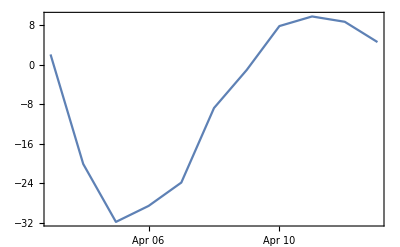

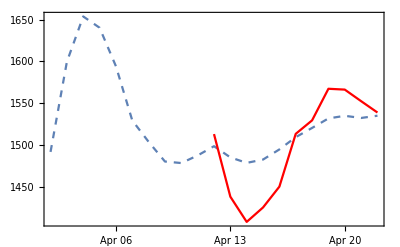

```mathematica
{tabctab,twinds}=estimates[cpert,cp0,21,timecpert];
{meanpasterrors,bootabctab,boottimewinds,bootdatelists}=bootstrapestimates[cpert,cp0,timecpert,21,bootwinl,cpstartdate,tabctab,twinds];
DateListPlot[meanpasterrors]
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red];
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[cpstartdate,timecpert[[21]]],PlotStyle->Dashed];
Show[bestfitplot,bootplot,PlotRange->All]
```

```mathematica
Clear[updater]
updater[tbootpdata_,tbootfdata_,tbootptime_,tbootftime_,abc_]:=Module[{i,a0,r2,r3,r4,tdata,ttime},
a0=abc;
tdata=tbootpdata;
ttime=tbootptime;
For[i=1,i≤Length[tbootfdata],i++,
tdata=AppendTo[tdata,tbootfdata[[i]]];
ttime=AppendTo[ttime,tbootftime[[i]]];
{a0,r2,r3,r4}=GNiteration[tdata,a0,ttime];
(*Print[a0];*)
];
a0
]
```

```mathematica
updater[tbootpdata,tbootfdata,tbootptime,futtime,sabc0]
```

{17439.4,2018.79,0.0764002}

{23056.4,55.8783,0.276821}

{232978.,9842.12,0.0706699}

{{2851.98,3331.95,3700.66,5372.94,6926.92,8645.31,10069.7,10848.5,12233.5,14376.7},7835.82}

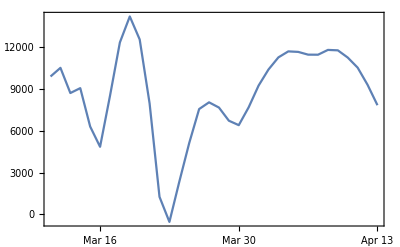

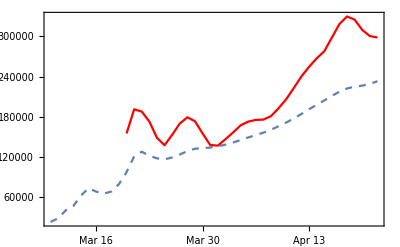

```mathematica
{tabctab,twinds}=estimates[itco,ip0,21,timeitco];
{meanpasterrors,bootabctab,boottimewinds,bootdatelists}=bootstrapestimates[itco,ip0,timeitco,21,bootwinl,itstartdate,tabctab,twinds];
DateListPlot[meanpasterrors]
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red];
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[itstartdate,timeitco[[21]]],PlotStyle->Dashed];
Show[bestfitplot,bootplot,PlotRange->All]
```

{9943.54,14.6999,0.258747}

{15524.,596.953,0.121417}

{{428.738,459.511,588.934,674.625,711.584,833.147,864.931,890.798,945.811,1065.2},746.328}

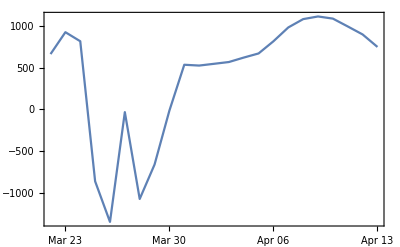

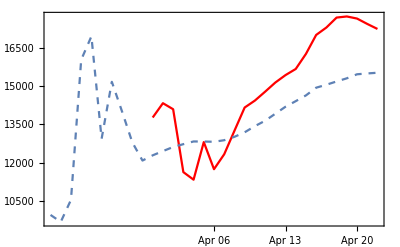

```mathematica
{tabctab,twinds}=estimates[avco,avp0,21,timeavco];
{meanpasterrors,bootabctab,boottimewinds,bootdatelists}=bootstrapestimates[avco,avp0,timeavco,21,bootwinl,avstartdate,tabctab,twinds];
DateListPlot[meanpasterrors]
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red];
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[avstartdate,timeavco[[21]]],PlotStyle->Dashed];
Show[bootplot,bestfitplot,PlotRange->All]
```

{51026.4,128.882,0.327775}

{165196.,7226.34,0.106316}

{{-121.929,716.552,2314.21,4362.57,5458.79,6049.12,6806.23,8857.4,9740.61,10798.5},5498.21}

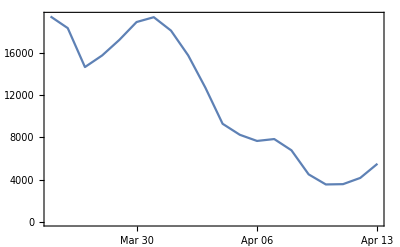

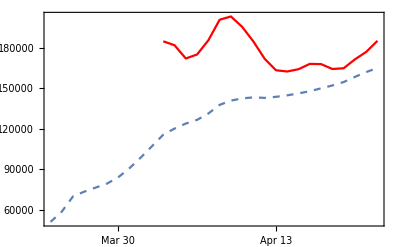

```mathematica
{tabctab,twinds}=estimates[lgerco,gp0,21,timelgerco];
{meanpasterrors,bootabctab,boottimewinds,bootdatelists}=bootstrapestimates[lgerco,gp0,timelgerco,21,bootwinl,gerstartdate,tabctab,twinds];
DateListPlot[meanpasterrors]
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red];
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[gerstartdate,timelgerco[[21]]],PlotStyle->Dashed];
Show[bestfitplot,bootplot,PlotRange->All]
```

{4945.17,35.6084,0.24003}

{7207.08,130.304,0.160307}

{{-86.4408,-167.795,-218.025,-172.376,-144.203,-116.897,-88.8346,-22.3351,47.3632,171.119},-79.8424}

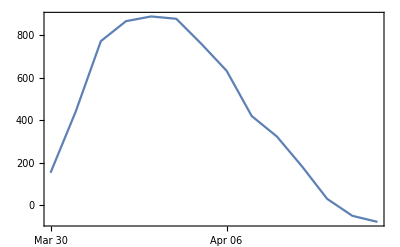

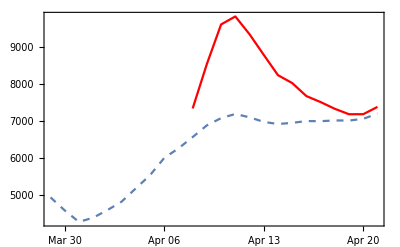

```mathematica
{tabctab,twinds}=estimates[ceska,cesp0,21,timeceska];
{meanpasterrors,bootabctab,boottimewinds,bootdatelists}=bootstrapestimates[ceska,cesp0,timeceska,21,bootwinl,ceskastartdate,tabctab,twinds];
DateListPlot[meanpasterrors]
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red];
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[ceskastartdate,timeceska[[21]]],PlotStyle->Dashed];
Show[bestfitplot,bootplot,PlotRange->All]
```

{609519.,18667.,0.203405}

{1.06467×10^6,52685.,0.12054}

{{5277.33,9220.89,18349.7,33973.5,48257.,63157.3,79240.9,105850.,119778.,142682.},62578.7}

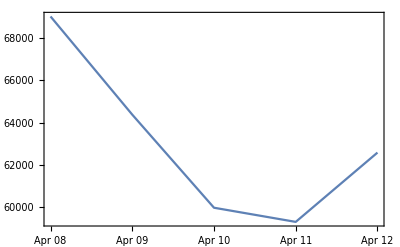

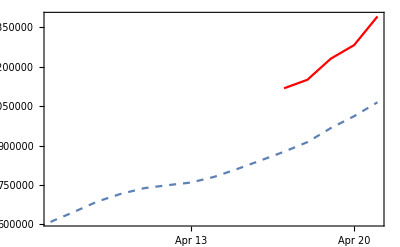

```mathematica
{tabctab,twinds}=estimates[ameri,ap0,21,timemeri];
{meanpasterrors,bootabctab,boottimewinds,bootdatelists}=bootstrapestimates[ameri,ap0,timemeri,21,bootwinl,ameristartdate,tabctab,twinds];
DateListPlot[meanpasterrors]
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red];
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[ameristartdate,timemeri[[21]]],PlotStyle->Dashed];
Show[bestfitplot,bootplot,PlotRange->All]
```

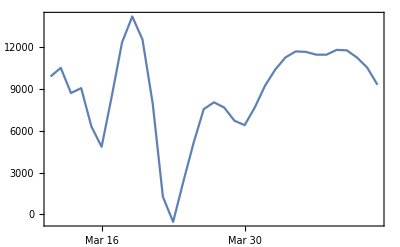

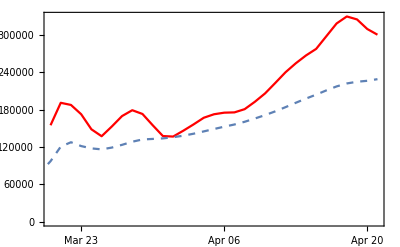

```mathematica
DateListPlot[meanpasterrors]
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red];
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[itstartdate,timeitco[[21]]],PlotStyle->Dashed];
Show[bootplot,bestfitplot]
```

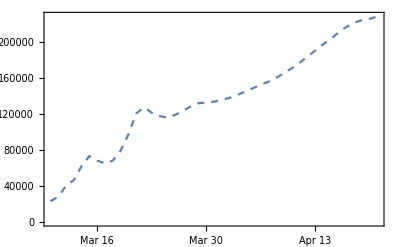

```mathematica
bestfitplot=DateListPlot[Transpose[tabctab][[1]],DatePlus[itstartdate,timeitco[[21]]],PlotStyle->Dashed]
```

```mathematica
sifdate=DatePlus[cpstartdate,expeak[tabctab[[-1]]]+plusd[tabctab[[-1]]]]
sifdate=DatePlus[cpstartdate,expeak[tabctab[[-1]]]]
```

{2020,4,26,15,34,21.2014}

{2020,3,28,14,49,41.705}

```mathematica
{2020,4,15}
```

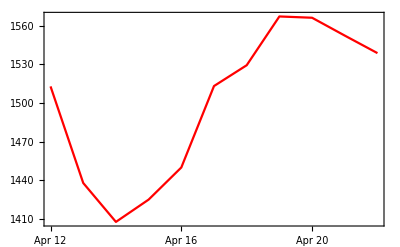

```mathematica
bootplot=DateListPlot[Transpose[{bootdatelists,Transpose[bootabctab][[1]]}],PlotStyle->Red,Ticks->{{{sifdate,"tax day",.05,Red}},Automatic}]
```

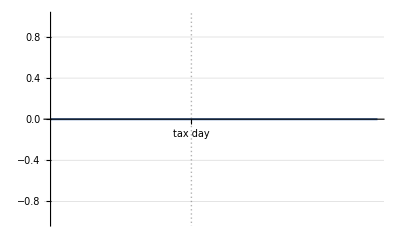

```mathematica
DateListPlot[Table[0,{i,0,20}],{2020,3,20},Ticks->{{{sifdate,"tax day",.05,Red}},Automatic},Axes->True,Frame->False,PlotTheme->"Detailed"]
```

```mathematica
tabctab[[-1]]
```

{1534.9,224.724,0.106094}

```mathematica
Transpose[tabctab][[1]]
```

{23056.4,28339.9,40335.8,46680.3,62349.3,73392.,68240.6,65268.2,68327.4,79443.9,97349.9,120758.,127781.,121637.,117927.,116360.,119239.,123625.,128642.,132261.,133100.,133983.,135852.,138308.,141466.,145190.,149015.,152766.,156259.,160618.,165857.,171304.,177380.,184086.,191066.,197826.,204154.,211006.,217340.,222091.,224842.,226364.,228986.}

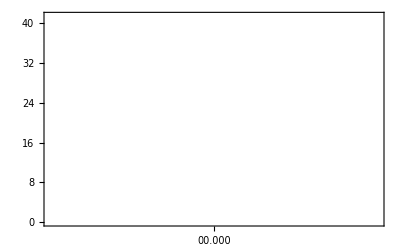

```mathematica
DateListPlot[{20.7},itstartdate,PlotStyle->{PointSize[5],Gray},Filling->Bottom]
```

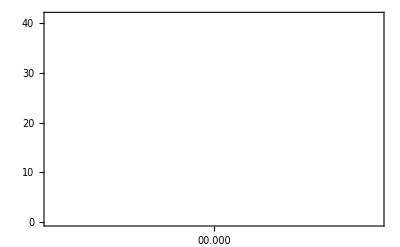

```mathematica
DateListPlot[{20.7},itstartdate,PlotTheme->"Web",PlotStyle->{PointSize[5],GrayLevel[0.5]},Filling->Bottom]
```

```mathematica
Show[%940,Axes->True]
```

-Graphics-

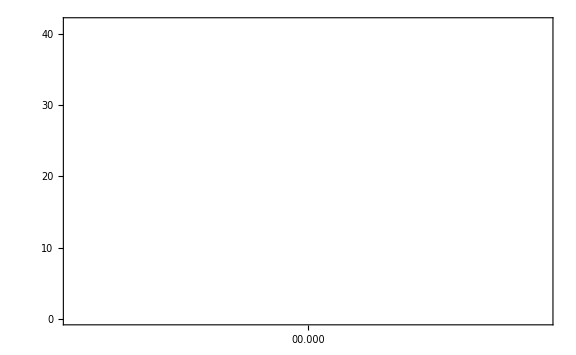

```mathematica
Show[%941,ImageSize->Large]
```

```mathematica
Transpose[tabctab][[1]]//Length
timeitco
```

43

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}

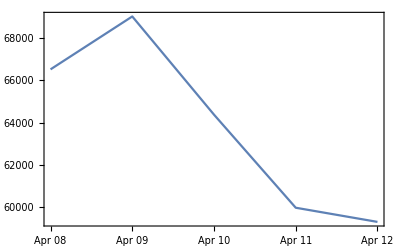

```mathematica
DateListPlot[bootres]
```

```mathematica
bootres=bootstrapestimates[greece,gp0,timegreece,21,bootwinl,greecestartdate]
```

{1104.09,28.185,0.218766}

{2387.08,54.1729,0.147276}

{{{{2020,3,28},304.098},{{2020,3,29},296.802},{{2020,3,30},281.397},{{2020,3,31},244.949},{{2020,4,1},186.997},{{2020,4,2},178.837},{{2020,4,3},132.921},{{2020,4,4},121.197},{{2020,4,5},-0.364796},{{2020,4,6},-157.121},{{2020,4,7},-180.685},{{2020,4,8},-131.357},{{2020,4,9},-52.1958},{{2020,4,10},-9.85694}}}

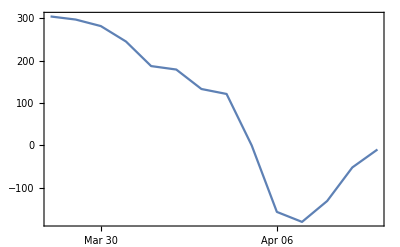

```mathematica
DateListPlot[bootres]
```

```mathematica
%//Mean
```

-6.39945

```mathematica
DateListPlot
```

```mathematica
sabcind=28;
{labcind,cabcind,rabcind}={sabcind-winl+1,sabcind,sabcind+winl};
pastdata=tmpdata[[labcind;;cabcind]]
%//Length
pasttime=ttime[[labcind;;cabcind]]
%//Length
futtime=Table[i,{i,cabcind+1,rabcind}]
%//Length
pftime=Flatten[{pasttime,futtime}];
curabc=tabctab[[cabcind-lag+1]]
pastabc=tabctab[[cabcind-lag-winl+1]]
```

{1646,1843,2649,3024,3631,4486,5282,5888,7029,7697}

10

{19,20,21,22,23,24,25,26,27,28}

10

{29,30,31,32,33,34,35,36,37,38}

10

{14002.,17.0344,0.247373}

{15463.2,502.422,0.126519}

```mathematica
pastests=Map[wmf[#,pastabc]&,pasttime]
pasterrors=pastdata-pastests
%//Length
futests=Map[wmf[#,curabc]&,futtime]
futests=futests+pasterrors;
```

{4189.49,4586.91,5005.3,5442.76,5896.89,6364.84,6843.37,7328.89,7817.61,8305.65}

{-2543.49,-2743.91,-2356.3,-2418.76,-2265.89,-1878.84,-1561.37,-1440.89,-788.613,-608.652}

10

{8594.39,9389.05,10119.7,10774.4,11347.6,11839.5,12254.3,12598.9,12881.8,13111.7}

{1646,1843,2649,3024,3631,4486,5282,5888,7029,7697,6050.91,6645.14,7763.38,8355.62,9081.74,9960.66,10692.9,11158.,12093.2,12503.}

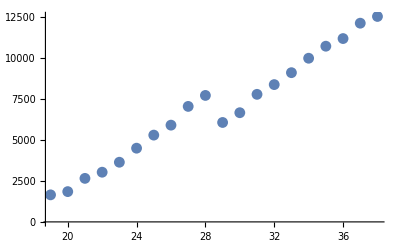

```mathematica
bootdata=Flatten[{pastdata,futests}]
ListPlot[Transpose[{pftime,bootdata}]]
```

```mathematica
curabc
```

{121637.,208.331,0.190701}

```mathematica
futests
futtime
```

{70967.9,77346.9,83108.1,88907.9,95152.2,102299.,109920.,117945.,124824.,130796.}

{35,36,37,38,39,40,41,42,43,44}

```mathematica
bootabc=curabc
bdata=tmpdata[[sabcind-lag+1;;]]
btime=ttime[[sabcind-lag+1;;]]
counter=1;
```

{121637.,208.331,0.190701}

{2502,3089,3858,4636,5883,7375,9172,10149,12462,15113,17660,21157,24747,27980,31506,35713,41035,47021,53578,59138,63928,69176,74386,80539,86498,92472,97689,101739,105792,110574,115242,119827,124632,128948,132547,135586,139422,143626,147577,152271,156363,159516,162488,165155,168941,172434,175927,178972,181228,183957}

{14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}

```mathematica
While[counter≤Length[futtime],
(*bdata=AppendTo[bdata,wmf[futtime[[counter]],curabc]+pasterrors[[counter]]];*)
bdata=AppendTo[bdata,futests[[counter]]];
btime=AppendTo[btime,futtime[[counter]]];
{bootabc,td1,td2,td3}=GNiteration[bdata,bootabc,btime];
counter=counter+1;
Print[{counter,bootabc}];
]
```

{2,{1,1,1}}

$Aborted

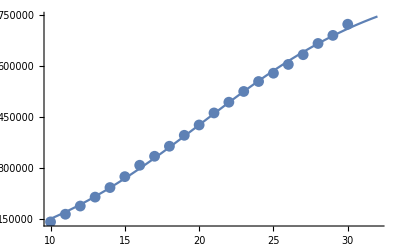

```mathematica
showplots[bdata,bootabc,btime]
```

```mathematica
?estimates
```

Global`estimates

estimates[tmpdata_,tp0_,lag_,time_]:=Module[{tmp20,tgl,backres,forwp0,forres,abctab,winds},{backres,abctab,winds}=stepGNiteration[tmpdata,tp0,lag,time,{0,-1},{1,Length[time]}];Print[backres];{forres,abctab,winds}=stepGNiteration[tmpdata,backres,lag-1,time,{1,1},{1,lag}];Print[forres];{abctab,winds}]

```mathematica
pastdata
```

{105792,110574,115242,119827,124632,128948,132547,135586,139422,143626,147577,152271,156363,159516}

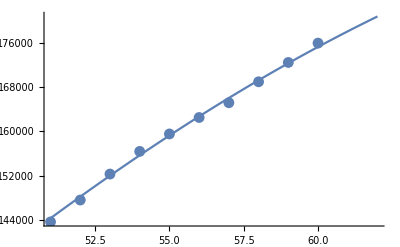

```mathematica
showplots[pastdata,curabc,pasttime]
```

```mathematica
pftime
```

{35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76}

```mathematica
stepGNiteration[bootdata,curabc,lag,pftime,{0,1},{2,lag}]
```

{{222091.,7470.95,0.0779504},{},{}}

```mathematica
?estimates
```

Global`estimates

estimates[tmpdata_,tp0_,lag_,time_]:=Module[{tmp20,tgl,backres,forwp0,forres,abctab,winds},{backres,abctab,winds}=stepGNiteration[tmpdata,tp0,lag,time,{0,-1},{1,Length[time]}];Print[backres];{forres,abctab,winds}=stepGNiteration[tmpdata,backres,lag-1,time,{1,1},{1,lag}];Print[forres];{abctab,winds}]

```mathematica
?stepGNiteration
```

Global`stepGNiteration

stepGNiteration[data_,ip0_,lag_,time_,step_]:=stepGNiteration[data,ip0,lag,time,step,{1,Length[time]}]
 
stepGNiteration[data_,ip0_,lag_,time_,step_,timewindow_]:=Module[{nres,nip0,l,abctab,windows,tempdata,temptime,lb,rb,notconv,firstind,lastind,outofbounds},(nip0=ip0;{lb,rb}=timewindow;l=Length[data];{firstind,lastind}={1,l};abctab={};windows={};nres={nip0,0,0,0};notconv=nres⟦1⟧==={1,1,1};outofbounds=lb+step⟦1⟧<firstind||rb+step⟦2⟧>lastind;);While[l≥lag&&!notconv&&!outofbounds,l=rb-lb;tempdata=data⟦lb;;rb⟧;temptime=time⟦lb;;rb⟧;nres=GNiteration[tempdata,nip0,temptime];nip0=nres⟦1⟧;notconv=nip0==={1,1,1};abctab=AppendTo[abctab,nip0];windows=AppendTo[windows,{lb,rb}];{lb,rb}={lb,rb}+step;outofbounds=lb<firstind||rb>lastind;];{nip0,abctab,windows}]

```mathematica
GNiteration[bootdata,curabc,pftime]
```

{{1,1,1},5,5.11244×10^16,30}

```mathematica
futests=pfests+pasterrors
bootdata=Flatten[{pastests,futests}]
ListPlot[Transpose[{pftime,bootdata}]]
```

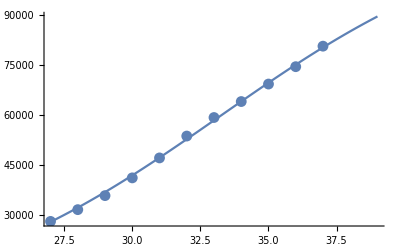

{28096.4,31867.4,35694.5,39482.4,43139.4,46586.4,49762.8,52629.4,55168.1,57379.2,59277.}

{-116.383,-361.402,18.4781,1552.65,3881.65,6991.63,9375.22,11298.6,14007.9,17006.8,21262.}

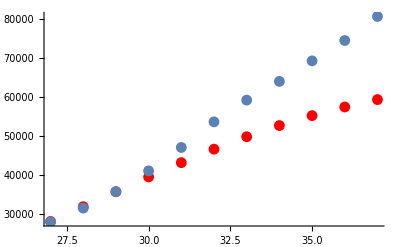

{-63063.9,2211.99}

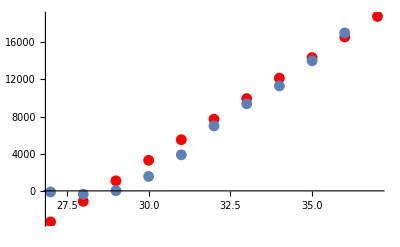

```mathematica
showplots[pastdata,curabc,pasttime]
pastests=Map[wmf[#,pastabc]&,pasttime]
pasterrors=pastdata-pastests
ListPlot[Transpose[{pasttime,pastdata}]];
ListPlot[Transpose[{pasttime,pastests}],PlotStyle->Red];
Show[%,%%,PlotRange->All]
ListPlot[Transpose[{pasttime,pasterrors}]];
lm=LinearModelFit[Transpose[{pasttime,pasterrors}],x,x];
{alm,blm}=lm["BestFitParameters"]
ListPlot[Transpose[{pasttime,pasterrors}]];
ListPlot[Transpose[{pasttime,alm+pasttime blm}],PlotStyle->Red];
Show[%,%%]
```

```mathematica
?LinearModelFit
```

RowBox[{"LinearModelFit", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["x", "TI"]}], "]"}] constructs a linear model of the form RowBox[{SubscriptBox["β", "0"], "+", RowBox[{SubscriptBox["β", "1"], SubscriptBox[StyleBox["f", "TI"], "1"]}], "+", RowBox[{SubscriptBox["β", "2"], SubscriptBox[StyleBox["f", "TI"], "2"]}], "+", StyleBox["…", "TR"]}] that fits the SubscriptBox[StyleBox["y", "TI"], StyleBox["i", "TI"]] for successive StyleBox["x", "TI"] values 1, 2, ….
RowBox[{"LinearModelFit", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["21", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["22", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] constructs a linear model of the form RowBox[{SubscriptBox["β", "0"], "+", RowBox[{SubscriptBox["β", "1"], SubscriptBox[StyleBox["f", "TI"], "1"]}], "+", RowBox[{SubscriptBox["β", "2"], SubscriptBox[StyleBox["f", "TI"], "2"]}], "+", StyleBox["…", "TR"]}] where the SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] depend on the variables SubscriptBox[StyleBox["x", "TI"], StyleBox["k", "TI"]]. 
RowBox[{"LinearModelFit", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["v", "TI"]}], "}"}], "]"}] constructs a linear model from the design matrix StyleBox["m", "TI"] and response vector StyleBox["v", "TI"].

```mathematica
nlm=NonlinearModelFit[Transpose[{pasttime,pasterrors}],a +b x+c x^2,{a,b,c},x];
```

{33010.1,-3729.41,88.2176}

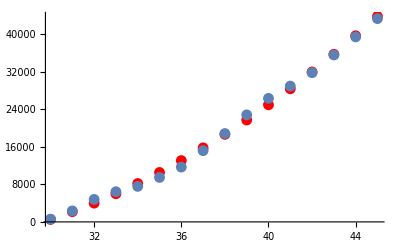

```mathematica
{alm,blm,clm}={a,b,c}/.nlm["BestFitParameters"]
ListPlot[Transpose[{pasttime,pasterrors}]];
ListPlot[Transpose[{pasttime,alm+pasttime blm+pasttime^2 clm}],PlotStyle->Red];
Show[%,%%]
```

```mathematica
MemoryInUse[]/10^6//N
```

416.565

```mathematica
MaxMemoryUsed[]
```

418391040

```mathematica
MemoryInUse[]
```

416737472

```mathematica
DateString[gerstartdate,{"MonthName"," ","YearShort"}]
```

March 20

```mathematica
DateString[DatePlus[gerstartdate,timelgerco[[-1]]],{"MonthName"," ","Day"}]
```

April 22

```mathematica
datestring=DateString[DatePlus[gerstartdate,timelgerco[[-1]]],{"MonthName"," ","Day"}]
Export
```

```mathematica
Directory[]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/plotdump

```mathematica
Export["slodate.txt",datestring]
```

slodate.txt

```mathematica
datestring=DateString[DatePlus[cpstartdate,timecpert[[-1]]],{"MonthName"," ","Day"}]
```

April 19

```mathematica
reldatetostring[startdate_,tplus_]:=DateString[DatePlus[startdate,tplus],{"MonthName"," ","Day"}]
```

```mathematica
reldatetostring[cpstartdate,timecpert[[-1]]]
```

April 19

```mathematica
DatePlus[avstartdate,timeavco[[-1]]]
```

{2020,4,19}

```mathematica
DatePlus[itstartdate,timeitco[[-1]]]
```

{2020,4,19}

```mathematica
DatePlus[ameristartdate,timemeri[[-1]]]
```

{2020,4,19}

```mathematica
cpstartdate
```

{2020,3,12}